# Quantum Optimization

This technical note presents documentation for the functionalities utilized in the implementation of quantum optimization algorithms. The document systematically outlines the core features, methodologies, and application contexts of the framework, offering insights into its integration within the quantum computational paradigm.

By providing a comprehensive overview and usage guidelines for these functions, we aim to introduce new and experienced users into quantum optimization techniques and quantum computing research.

```mathematica
<<Wolfram`QuantumFramework`
<<Wolfram`QuantumFramework`QuantumOptimization`
```

## Variational Quantum Algorithms

### Introduction

Quantum computing has long been envisioned as a transformative technology, with the potential to tackle problems that are intractable for classical computers. Quantum algorithms promise exponential speedups in areas such as number factorization, quantum system simulation, and solving linear systems of equations.

The introduction of cloud-based quantum computers in 2016 provided public access to real quantum hardware. However, due to noise and the limited number of qubits, running large-scale quantum algorithms remained impractical. This led to growing interest in what could be achieved with these early devices, commonly referred to as Noisy Intermediate-Scale Quantum (NISQ) computers. Today’s state-of-the-art NISQ devices contain up to 1000 qubits, with only two quantum processors having over 1,000 qubits, making it possible to surpass classical supercomputers in specific, carefully designed computational tasks—a milestone known as quantum supremacy.

Variational Quantum Algorithms (VQAs) have emerged as the leading approach for using the power of NISQ devices. Given the constraints of current quantum hardware, VQAs employ a hybrid quantum-classical optimization framework. They utilize parameterized quantum circuits executed on a quantum computer, while classical optimizers adjust the parameters to minimize a given cost function. This strategy mirrors machine-learning techniques, such as neural networks, which rely on optimization-based learning methods.

### Applications

VQAs have been explored for a wide range of applications, spanning nearly all areas initially envisioned for quantum computing. As illustrated in the following image, VQAs are applied across various domains, including error correction, machine learning, combinatorial optimization, ground-state estimation, and mathematical problem-solving.

Cerezo, M., Arrasmith, A., Babbush, R. et al. Variational quantum algorithms. Nat Rev Phys 3, 625–644 (2021)

While they hold promise for achieving near-term quantum advantage, significant challenges remain, including issues related to trainability, accuracy, and efficiency. Addressing these challenges is crucial for the continued advancement of VQAs and their practical implementation in solving real-world problems.

In simple terms, Variational Quantum Algorithms (VQAs) are one of the most popular approaches for running quantum algorithms on today’s early-stage quantum computers. You can think of VQAs like “putting the carriage before the horses”, we know what problem we want to solve, but we don’t yet know the exact quantum circuit to do it. Instead of designing the circuit manually, VQAs use classical optimization techniques to “learn” the best circuit for the task.

### Pipeline

The core components of this algorithms include a parameterized quantum circuit, known as the ansatz, which is used to represent possible solutions. This ansatz is evaluated through a cost function that encodes the problem we are trying to solve. Finally, a training procedure, primarily driven by a classical optimizer, adjusts the parameters of the ansatz to improve the solution iteratively.

```mathematica
v1="Circuit Ansatz";v2="Problem-Specific\nCost Function";v3="Training Procedure";
edges=DirectedEdge@@@{v1->v2,v2->v3,v3->v1};

GraphPlot[edges,PlotTheme->"VibrantColor" ,VertexSize->Large,VertexLabels->Placed["Name",{1/2,1/2}],VertexLabelStyle->Directive[White,Italic,15],VertexCoordinates->{v1->{0.125,0.1},v2->{.1,0.05},v3->{.15,.05}},PlotLabel->"VQA Components",ImageSize->Large]
```

-Graphics-

This process is best illustrated in the Hybrid Loop shown in the next image. The quantum computer runs the ansatz, the results are evaluated through the cost function, and the classical optimizer processes this information to update the parameters for the next iteration.

Cerezo, M., Arrasmith, A., Babbush, R. et al. Variational quantum algorithms. Nat Rev Phys 3, 625–644 (2021)

Now, rather than just describing it, let’s dive into parametrized circuits!

## Variational Circuits

The area of Quantum Optimization depends heavily in variational algorithms. This algorithms work by exploring and comparing variational states ϕ (θ)  that depends on a set of { θ }_(,n) parameters.

You can build this variational states using a fixed initial state as 0 and a parametrized or variational quantum circuit V(θ,,):

ϕ (θ)=V(θ,,)0

We aim to train these variational quantum circuits using an optimizer in conjunction with a cost function that reflects the objective of our optimization. Many of the algorithms presented here are Hybrid Algorithms, meaning they combine a quantum circuit with a classical optimizer.

Wolfram Quantum Framework supports "free parameters" in their quantum circuits. In order to implement a variational quantum circuit, you only need to specify this tunable parameters by using the "Parameters" option:

```mathematica
vqc=QuantumCircuitOperator[{"00","RX"[θ1]->{1},"RY"[θ2]->{2}},"Parameters"->{θ1,θ2}];
```

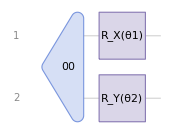

```mathematica
vqc["Diagram"]
```

The parameters defined for a Wolfram Quantum Framework Operator are heritable, so you do not need to redefine it in later steps. For example we can calculate the resultant ϕ (θ) state from our defined variational circuit:

```mathematica
vqs = vqc[]
```

QuantumState[…]

We can verify that the "Parameters" option values:

```mathematica
vqs["Parameters"]
```

{θ1,θ2}

This option simplifies the repeated execution of the circuit by using the symbolic computation capabilities provided by the Wolfram Quantum Framework:

```mathematica
vqc["Formula"]
```

Cos[θ1/2] Cos[θ2/2]00+Cos[θ1/2] Sin[θ2/2]01-ⅈ Cos[θ2/2] Sin[θ1/2]10-ⅈ Sin[θ1/2] Sin[θ2/2]11

Replace θ1 value as follows:

```mathematica
vqc[<|θ1->0|>]["Formula"]
```

Cos[θ2/2]00+Sin[θ2/2]01

As mentioned earlier, you can use the parameters at any stage of your algorithm, as they are carried through each step:

```mathematica
vqs["Formula"]
```

Cos[θ1/2] Cos[θ2/2]00+Cos[θ1/2] Sin[θ2/2]01-ⅈ Cos[θ2/2] Sin[θ1/2]10-ⅈ Sin[θ1/2] Sin[θ2/2]11

```mathematica
vqs[<|θ2->0,θ1->0|>]["Formula"]
```

00

You can directly replace the values for each parameter following the same order you defined them:

```mathematica
vqs[0,0]["Formula"]
```

00

```mathematica
vqs[a,b]["Formula"]
```

Cos[a/2] Cos[b/2]00+Cos[a/2] Sin[b/2]01-ⅈ Cos[b/2] Sin[a/2]10-ⅈ Sin[a/2] Sin[b/2]11

In the following sections, we will explore variational algorithms, which will require an understanding of how to properly design (ansatz circuits) and train (classical optimizers) these variational circuits.

### Initial State Preparation

A reference state serves as the fixed starting point for our problem. To prepare a reference state, we apply a non-parameterized unitary gate U_R​ at the beginning of our quantum circuit, ensuring that our initial state is given by:

ψ_i=U_R 0

If you have an educated guess or an existing optimal solution, using it as the reference state can help the variational algorithm converge faster.

The simplest reference state is the default state, where we initialize an n-qubit quantum circuit in the all-zero state:

ψ_i=0^(⊗n), U_R=𝟙

For this default state, our unitary operator is simply the identity operator. Due to its simplicity, this default state is widely used as a reference state in many applications.

If we want to start with a more complex reference state that involves superposition and entanglement, we can prepare a state such as:

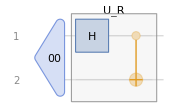

```mathematica
qc=QuantumCircuitOperator[{"H"->1,"CNOT"->{1,2}},"Label"->"U_R"];
qc=QuantumCircuitOperator[{"00",qc}];
qc["Diagram",ImageSize->Small]
```

Which is also called a Bell State:

```mathematica
qc[]["Formula"]
```

1/(√2)00+1/(√2)11

### Ansatz Circuits

In physics and mathematics, the German word “Ansatz” refers to an educated guess for solving a problem. You may have done this before—trying out a potential solution based on intuition or prior knowledge. However, an ansatz is not just any guess; it must be well-informed.

In Variational Quantum Algorithms (VQAs), what we are guessing is the quantum circuit that will solve our problem. This is why we refer to this circuit simply as the ansatz

Generate a collection of parametrized states:

ψ(θ^(->))=U_V(θ^(->))U_R 0

How Do We Choose an Ansatz?

Problem-Inspired Ansatz

If we have prior knowledge about the problem, we can use physical intuition or mathematical insights to design a circuit tailored to the task. This approach typically leads to more efficient circuits with fewer parameters, making optimization easier. These are usually referred to generally as Hardware-Efficient ansatz.

Problem-Agnostic Ansatz

If we lack detailed knowledge about the problem, we can use a more general universal ansatz that does not rely on problem-specific intuition. These ansatze are more expressive, meaning they can represent a wide range of solutions. However, they also tend to be larger, with more gates and parameters, making the optimization process significantly harder.

If we consider this simple ansatz, consisting of a pair of rotations and a CNOT gate, we can evaluate it and examine the states that can be generated:

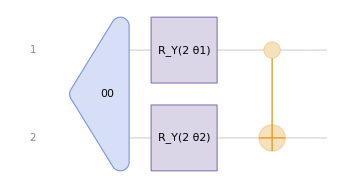

```mathematica
ansatz=QuantumCircuitOperator[{"00","RY"[2θ1],"RY"[2θ2]->{2},"CNOT"}];
ansatz["Diagram"]
```

As we observe, the possible states generated by this ansatz are limited to those determined by the sine and cosine functions. Therefore, even with an excellent optimizer, there will be certain values that this ansatz will never be able to reach:

```mathematica
ansatz["Table"]
```

| 1
00 | Cos[θ1] Cos[θ2]
01 | Cos[θ1] Sin[θ2]
10 | Sin[θ1] Sin[θ2]
11 | Cos[θ2] Sin[θ1]

How good is an ansatz?

Expressibility

This measures the range of functions that the quantum circuit can represent. Higher expressibility is generally linked to more entanglement and a greater number of parameters. The more expressive an ansatz is, the more problems it can potentially solve.

Trainability

This refers to how easy it is to find the right parameters for the circuit. Larger, highly expressive circuits are harder to optimize because the optimizer must explore a vast parameter space. The difficulty of training also depends on the cost function and the classical optimizer used.

There is a natural trade-off between expressibility and trainability. Highly expressive circuits are powerful but harder to train, while simpler circuits may be easier to optimize but might not capture the necessary complexity of the problem.

The goal is to find an ansatz in the “sweet spot”—one that is expressive enough to solve the problem but still trainable within a reasonable amount of time.

Now, let’s explore this concept further with an exercise!

Exercise 1:

Express the collection of parametrized states generated by the following ansatz:

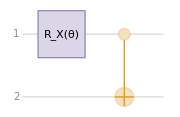

```mathematica
QuantumCircuitOperator[{"RX"[θ],"CNOT"}]["Diagram",ImageSize->Small]
```

Step by step:

```mathematica
QuantumOperator["RX"[θ]]@QuantumState["00"]//TraditionalForm
```

cos(θ/2)00-ⅈ sin(θ/2)10

```mathematica
result1=QuantumOperator["CNOT"]@%
```

QuantumState[…]

```mathematica
result1["Formula"]
```

Cos[θ/2]00-ⅈ Sin[θ/2]11

Exercise 2:

Express the collection of parametrized states generated by the following ansatz:

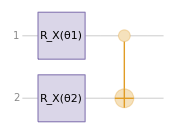

```mathematica
QuantumCircuitOperator[{"RX"[θ1],"RX"[θ2]->{2},"CNOT"}]["Diagram",ImageSize->Small]
```

Following the same steps:

```mathematica
QuantumOperator[{"RX"[θ1]->1,"RX"[θ2]->2},"Parameters"->{θ1,θ2}]@QuantumState["00"]
```

cos(θ1/2) cos(θ2/2)00-ⅈ cos(θ1/2) sin(θ2/2)01-ⅈ sin(θ1/2) cos(θ2/2)10-sin(θ1/2) sin(θ2/2)11

```mathematica
result2=QuantumOperator["CNOT"]@%
```

QuantumState[…]

```mathematica
result2["Formula"]
```

Cos[θ1/2] Cos[θ2/2]00-ⅈ Cos[θ1/2] Sin[θ2/2]01-Sin[θ1/2] Sin[θ2/2]10-ⅈ Cos[θ2/2] Sin[θ1/2]11

We can verify that the second ansatz has more expressibility by the simple fact that:

```mathematica
result2[θ,0]["Formula"]
```

Cos[θ/2]00-ⅈ Sin[θ/2]11

The first ansatz is a specific case of the second ansatz:

```mathematica
result1["Formula"]
```

Cos[θ/2]00-ⅈ Sin[θ/2]11

#### Layered Circuit Architecture

What happens if we have no idea about the problem solution?

Layered gate architectures, where the ansatz is repeated multiple times, have been shown to offer a good balance between expressibility and relatively low circuit depth, making them effective for tackling a broad range of problems.

If the problem we are trying to solve doesn’t require a large number of parameters, a good option might be to use an ansatz called the Basic Entangler. This ansatz is often favored for its simplicity and efficiency in cases where the problem doesn’t demand an overly complex parameterized quantum circuit. This layers consist of one-parameter single-qubit rotations on each qubit, followed by a closed chain or ring of CNOT gates.

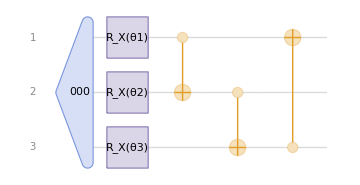

```mathematica
basicentanglement=QuantumCircuitOperator[{"000","RX"[θ1]->1,"RX"[θ2]->2,"RX"[θ3]->3,"CNOT"->{1,2},"CNOT"->{2,3},"CNOT"->{3,1}}];
basicentanglement["Diagram"]
```

```mathematica
basicentanglement["Table"]
```

| 1
000 | Cos[θ1/2] Cos[θ2/2] Cos[θ3/2]
001 | ⅈ Sin[θ1/2] Sin[θ2/2] Sin[θ3/2]
010 | -Cos[θ1/2] Sin[θ2/2] Sin[θ3/2]
011 | -ⅈ Cos[θ2/2] Cos[θ3/2] Sin[θ1/2]
100 | -Cos[θ3/2] Sin[θ1/2] Sin[θ2/2]
101 | -ⅈ Cos[θ1/2] Cos[θ2/2] Sin[θ3/2]
110 | -Cos[θ2/2] Sin[θ1/2] Sin[θ3/2]
111 | -ⅈ Cos[θ1/2] Cos[θ3/2] Sin[θ2/2]

In order to generate multiple layers of parametrized gates or controlled gates you can use the following functionalities:

GenerateParameters[n,m,opts] | generate n x m parameters, indicating the n number of qubits and m number of layers. The parameters are named θ_i for i ∈ {1,…, n x m}
ParametrizedLayer[gate,qubits,index, opts]
ParametrizedLayer[gate,index, opts]
 | generates a layer of parameterized gates on the specified qubits. The parameters are denoted as θ_i  where i ∈ index. If only index is provided (with no qubits), a layer of gates with the same length is generated for all qubits.
EntanglementLayer[cgate,qubits] | generate a layer of controlled cgate connecting each qubits

#### ParametrizedLayer & GenerateParameters

##### ParametrizedLayer

The ParametrizedLayer function reduces redundant code in layered quantum circuit architectures by applying parameterized gates  and automatically generating the necessary parameters.

It is possible to specify both the qubits on which the parameterized gates will be applied and the index for each parameter:

```mathematica
ParametrizedLayer["RY", Range[1, 3],{a,b,c}]
```

Sequence[RY[θa]→{1},RY[θb]→{2},RY[θc]→{3}]

```mathematica
ParametrizedLayer["RY", Range[97,99], Range[3]]
```

Sequence[RY[θ1]→{97},RY[θ2]→{98},RY[θ3]→{99}]

Alternatively, you can specify only the parameter indices, and the gates will be generated sequentially for each qubit, starting from qubit 1:

```mathematica
ParametrizedLayer["RY", Range[4,6]]
```

Sequence[RY[θ4]→{1},RY[θ5]→{2},RY[θ6]→{3}]

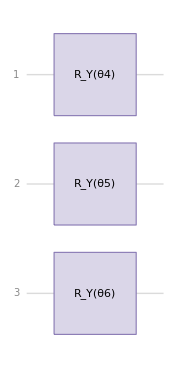

```mathematica
QuantumCircuitOperator[{%}]["Diagram",ImageSize->Small]
```

##### GenerateParameters

The GenerateParameters function generates a list of symbols; you only need to specify the number of qubits and layers in the quantum circuit:

```mathematica
GenerateParameters[3, 3]
```

{θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8,θ9}

##### Example

```mathematica
basicentaglement=QuantumCircuitOperator[{"00000",
ParametrizedLayer["RY",Range[5]],
EntanglementLayer["CNOT",Range[5],"Entanglement"->"Linear"],
"Barrier",
ParametrizedLayer["RY",Range[6,10]],
EntanglementLayer["CNOT",Range[5],"Entanglement"->"Linear"],
"Barrier",
ParametrizedLayer["RY",Range[11,15]]},
"Parameters"->GenerateParameters[5, 3]
];
```

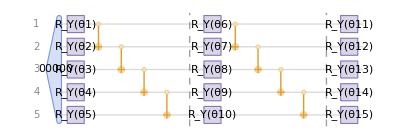

```mathematica
basicentaglement["Diagram",ImageSize->Full]
```

##### Options

"Symbol" | "θ" | define the main symbol used for the parameters

GenerateParameters and ParametrizedLayer functions use "θ" as default symbol:

```mathematica
GenerateParameters[3, 3]
```

{θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8,θ9}

```mathematica
ParametrizedLayer["RY",Range[4,6]]
```

Sequence[RY[θ4]→{1},RY[θ5]→{2},RY[θ6]→{3}]

Use "Symbol" option to change the default symbol:

```mathematica
GenerateParameters[3, 3,"Symbol"->"ϕ"]
```

{ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ϕ7,ϕ8,ϕ9}

```mathematica
ParametrizedLayer["RY", Range[4, 6],"Symbol" -> "ϕ"]
```

Sequence[RY[ϕ4]→{1},RY[ϕ5]→{2},RY[ϕ6]→{3}]

#### EntanglementLayer

The EntanglementLayer function is designed to reduce redundant code in layered quantum circuit architectures by facilitating controlled operations between qubits.

```mathematica
EntanglementLayer["CNOT", {1,2,3}]
```

Sequence[CNOT→{1,2},CNOT→{1,3},CNOT→{2,3}]

The EntanglementLayer function returns a Sequence of multiple Rules, each representing a controlled gate applied to connected qubits according to the chosen entanglement strategy. Currently, the function supports only named controlled gates between two qubits.

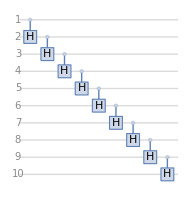

```mathematica
QuantumCircuitOperator[{
EntanglementLayer["CH", Range[10],"Entanglement"->"Linear"]
}]["Diagram"]
```

Entanglement

The "Entanglement" option specifies the strategy used for entanglement. It supports the following values:

Automatic | each qubit is entangled with all the others.
"Linear" | each qubit is entangled with the following qubit in the sequence
"Circular" | each qubit is entangled with all others, with an additional connection between the first and last qubit before the sequence.
"ReverseLinear" | each qubit is entangled with the following one, in reverse order from last to first
"Pairwise" | consists of two layers: one for even-positioned qubits and another for odd-positioned qubits, each entangled with the next.

```mathematica
qubits=Range[5];
strategy={Automatic,"Linear","ReverseLinear","Pairwise","Circular"};
subqc=QuantumCircuitOperator[{EntanglementLayer["CNOT",qubits,"Entanglement"->#]},"Label"->#]&/@strategy;
```

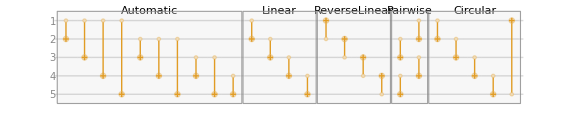

```mathematica
QuantumCircuitOperator[subqc]["Diagram",ImageSize->Large]
```

## Variational Quantum Eigensolver (VQE)

The variational quantum eigensolver (VQE) is a hybrid algorithm that combines classical and quantum computing to determine the ground state energy of a Hamiltonian. It utilizes quantum algorithms to calculate expected energy values and classical optimization techniques for minimizing that energy.

VQE plays a crucial role in quantum optimization, particularly in solving complex problems in quantum chemistry and materials science. By enabling efficient simulations of intricate systems, VQE can address optimization tasks that are challenging for classical methods alone.

Given a Hamiltonian operator H, this method consist of two main components:

A  variational circuit ansatz V(θ,,).

A cost function ℒ=ϕ(θ)Hϕ(θ), where ϕ (θ)=V(θ,,)0 .

The method  involves iteratively adjusting θ to minimize the average energy or cost function 𝒻.

#### Implementation

In order to understand how to proceed with the VQE algorithm, let's drive the a variational stateϕ (θ) to the ground state of the following Hamiltonian:

```mathematica
H=QuantumOperator["X"+"Z"]
```

QuantumOperator[…]

Define the ansatz circuit V(θ):

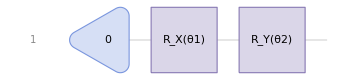

```mathematica
V=QuantumCircuitOperator[{"0","RX"[θ1]->{1},"RY"[θ2]->{1}},"Parameters"->{θ1,θ2}];
"Diagram"//V
```

Calculate ϕ (θ) from the ansatz circuit V:

```mathematica
ϕ=V[];
"Formula"//ϕ
```

(Cos[θ1/2] Cos[θ2/2]+ⅈ Sin[θ1/2] Sin[θ2/2])0+(-ⅈ Cos[θ2/2] Sin[θ1/2]+Cos[θ1/2] Sin[θ2/2])1

Implement the cost function ℒ as stated before:

```mathematica
ℒ[θ1_,θ2_]=ComplexExpand["Scalar"//SuperDagger[ϕ]@H@ϕ];
ℒ[θ1, θ2]//Simplify
```

Cos[θ1] (Cos[θ2]+Sin[θ2])

Calculate the ground state eigenvalue of H by minimizing 𝒻:

```mathematica
MinValue[ℒ[θ1, θ2], {θ1, θ2}]
```

-√2

#### Visualizations

In order to visualize the optimization process, we need to get all the parameter values during the evolution, in this case we will use a simple gradient descent method:

```mathematica
initialPosition={0.1,0.1};
```

```mathematica
params=GradientDescent[ℒ,initialPosition];
```

It would be also useful to calculate all the cost function values during each step of the parameter evolution:

```mathematica
costs=ℒ@@@params;
```

##### Cost curve

We can visualize the evolution of our optimization during time in an Cost Curve, also known as Loss Curve:

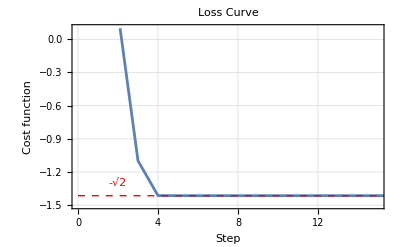

```mathematica
ListLinePlot[costs,]
```

##### Parameter Space

We can visualize the evolution of our optimization in the parameter space in a Contour Plot:

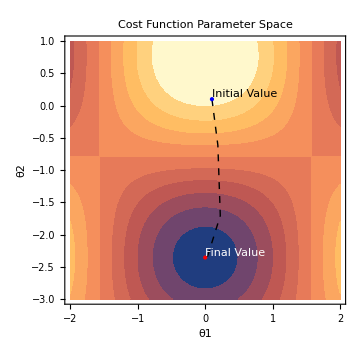

```mathematica
ContourPlot[ℒ[θ1,θ2],]
```

##### Gradient Vector Plot

The stream plot of the gradient of our cost function can provide insight into the behavior of the evolution as observed in its parameter space:

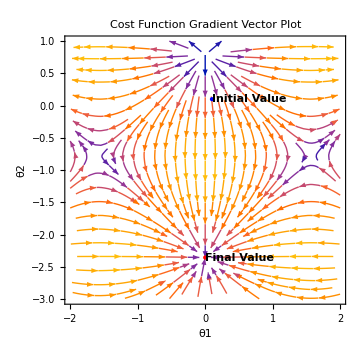

```mathematica
StreamPlot[Evaluate[-Grad[ℒ[θ1, θ2], {θ1, θ2}]],]
```

#### Quantum Chemistry

The Variational Quantum Eigensolver (VQE) is a valuable tool in quantum chemistry for finding the minimal energy of a molecule. The task is essentially an optimization problem, where the goal is to minimize the total energy of the molecule with respect to the positions of the atomic nuclei.

In the case of VQE, we use parameterized quantum circuits to approximate the ground state energy of the system. This results in the determination of the minimal energy of the system, which corresponds to the lowest energy configuration of the molecule in its ground state.

This minimal energy result can be incredibly useful in determining the geometry of the molecule as well, as the lowest energy corresponds to the optimized configuration of the atomic nuclei. Therefore, although the main goal is to minimize the energy, this process can also provide insights into the stable arrangement of atoms in the molecule.

##### Toy H_2 Molecule

The current problem is finding the ground state of the H_2 molecule;,the Hamiltonian can be reduced and modeled using two qubits as:

```mathematica
H2=QuantumOperator[α("ZI"+"IZ")+β*"XX"]
```

QuantumOperator[…]

Implement the algorithm as we learned last class:

First: Parametrized quantum circuits, state and ansatz preparation.

In this case we will use a typical hardware-efficient ansatz: Two layers of Rotations and a CNOT to ensure the entanglement.

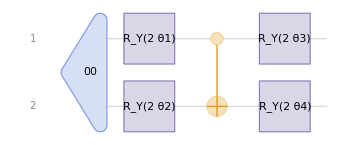

```mathematica
HEAnsatz=QuantumCircuitOperator[{"00","RY"[2 θ1]->1,"RY"[2 θ2]->2,"CNOT"->{1,2},"RY"[2 θ3]->1,"RY"[2 θ4]->2}];
HEAnsatz["Diagram"]
```

Second: Cost function ⟨ H(θ) ⟩

We need a cost function, so let’s obtain the QuantumState from the QuantumCircuit and define the bra and ket.

```mathematica
ϕ=HEAnsatz[];ϕ=SuperDagger[ϕ];
```

Finally lets compute the energy of our system and define a function that will work as the cost function. In this step we should help the optimizer by Simplifying and replacing fixed values.

```mathematica
energy=ϕ@H2@ϕ ;
```

```mathematica
values={α->0.4,β->0.2};
costH2[θ1_,θ2_,θ3_,θ4_]=FullSimplify["Scalar"//energy,{θ1,θ2,θ3,θ4}∈Reals]/.values
```

Sin[2 θ1] (0.2 Cos[2 θ3] Cos[2 θ4]-0.4 Sin[2 θ2] Sin[2 θ3])+Cos[2 θ1] (0.4 Cos[2 θ3]+Cos[2 θ4] (0.4 Cos[2 θ2]+0.2 Sin[2 θ2] Sin[2 θ3]))+(-0.4 Sin[2 θ2]+0.2 Cos[2 θ2] Sin[2 θ3]) Sin[2 θ4]

As I mentioned, the cost function we are working with is not trivial, but the advantage is that we can compute it symbolically, which significantly helps in the optimization process.

Third: Optimization

To find the optimal parameters for our quantum circuit, we can use the NMinimize function in Mathematica.

```mathematica
resultH2=NMinimize[costH2[θ1,θ2,θ3,θ4],{θ1,θ2,θ3,θ4}]
```

{-0.824621,{θ1→0.717444,θ2→-0.909051,θ3→-0.855457,θ4→2.37329}}

This function allows us to minimize the cost function by adjusting the parameters, and after performing this minimization, we obtain the optimized parameters and the minimum value of the cost function, which in this case is approximately -0.824.

```mathematica
paramH2=Last[resultH2]//Association
```

<|θ1→0.717444,θ2→-0.909051,θ3→-0.855457,θ4→2.37329|>

Now that we have the optimal value, it is insightful to inspect the behavior of the cost function around these points. Since we have four variables (the parameters in the ansatz), we need to fix two of the values in order to visualize the function.

We can do this by using a ContourPlot, which will allow us to observe the shape of the cost function in two dimensions.

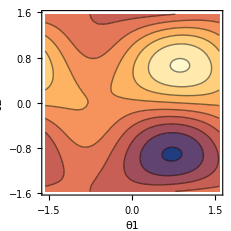

```mathematica
ContourPlot[costH2[θ1,θ2,paramH2[θ3],paramH2[θ4]],{θ1,-π/2,π/2},{θ2,-π/2,π/2},FrameLabel->Automatic]
```

ContourPlot is useful here because it highlights where the cost function attains higher and lower values. In this plot, the lighter sections correspond to higher values, and the blue sections represent the lowest values of the cost function.

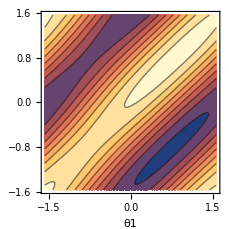

```mathematica
ContourPlot[costH2[θ1,paramH2[θ2],θ3,paramH2[θ4]],{θ1,-π/2,π/2},{θ3,-π/2,π/2},FrameLabel->Automatic]
```

If the optimization algorithm has started with a point near the blue section (where the minimum lies), we can expect it to converge towards this blue region, as this represents the optimal set of parameters. The algorithm searches for regions where the cost is minimized, and this plot helps visualize the “shape” of the function.

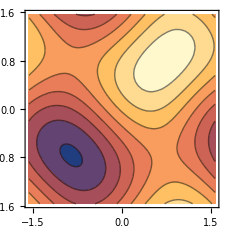

```mathematica
ContourPlot[costH2[paramH2[θ1],paramH2[θ2],θ3,θ4],{θ3,-π/2,π/2},{θ4,-π/2,π/2}]
```

When the cost function is relatively simple and can be expressed symbolically, the ContourPlot can exhibit repetitive patterns. This repetition often results from the periodic nature of trigonometric functions (e.g., sin⁡and cos) that may appear in the cost function due to the rotation gates used in the ansatz.

Example from  https://arxiv.org/pdf/1909.05074v1

##### Trihydrogen cation

In this example we will obtain the minimal energy for the molecule Cation H_3^+.

First we will use some python code from PennyLane to obtain the Hamiltonian corresponding to the H3 cation.

We just need to indicate the molecules “H” and the coordinates:

import pennylane as qml
from pennylane import numpy as np

symbols = ["H", "H", "H"]
coordinates = np.array([0.028, 0.054, 0.0, 0.986, 1.610, 0.0, 1.855, 0.002, 0.0])

# Building the molecular hamiltonian for the trihydrogen cation
hamiltonian, qubits = qml.qchem.molecular_hamiltonian(symbols, coordinates, charge=1)

qml.matrix(hamiltonian)

NumericArray[…]

In case Python is not available, you can import it from this location:

```mathematica
Import["https://wolfr.am/1uXbew3vg"]
```

NumericArray[…]

Finally we obtain a NumericArray which we will turn into a QuantumOperator:

```mathematica
H3=QuantumOperator[%//Normal]
```

QuantumOperator[…]

If we have no prior knowledge of the structure of the circuit, a reasonable starting point could be a layered circuit consisting of rotations around the Y-axis and CNOT gates.

To encode the occupation numbers of the molecular spin-orbitals, we would need six qubits.

```mathematica
param=GenerateParameters[6,2];
basicMixAnsatz=QuantumCircuitOperator[{
ParametrizedLayer["RY",Range[1,6]],
EntanglementLayer["CNOT",Range[6]],
"Barrier",
ParametrizedLayer["RY",Range[7,12]]
},
"Parameters"->param
];
```

If you’d like to learn how to construct layered circuits using ParametrizedLayer and EntanglementLayer please refer to the Quantum Optimization documentation.

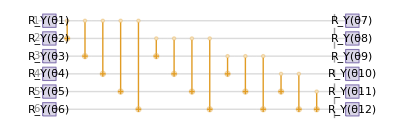

```mathematica
basicMixAnsatz["Diagram",ImageSize->Full]
```

In this case, you can expect a very complex symbolic cost function. To handle this, we could choose to implement a numerical function instead.

```mathematica
stateAnsatz=basicMixAnsatz[];
```

```mathematica
matrixH3=H3["Matrix"];
```

We begin by using Module to define the quantum state with parameters replaced by real numbers.  Next, we define the ket and bra, and then compute the scalar resulting from the expectation value of the Hamiltonian H.

```mathematica
ClearAll[meanEnergy]
meanEnergy[values_,H_]:=Module[{ket,bra,state},
state=stateAnsatz[AssociationThread[param,values]];
ket=state["StateVector"];
bra=SuperDagger[state]["StateVector"];
Re[bra.H.ket]
]
```

After defining the cost function, we can apply a classical optimizer starting from an initial guess to find the minimum energy value.

```mathematica
init=Thread[{param,{π,0,0,0,π/2,π,0,0,0,0,π,0}}];
```

```mathematica
FindMinimum[meanEnergy[param,matrixH3],init]//Quiet
```

{-1.30949,{θ1→3.13598,θ2→-0.196715,θ3→-0.00696906,θ4→-0.00209702,θ5→1.45483,θ6→3.14184,θ7→-3.02125×10^-7,θ8→-2.94889×10^-7,θ9→2.37779×10^-7,θ10→-8.8975×10^-7,θ11→3.14373,θ12→-3.14374}}

If we are interested in obtaining the geometry of the system, we would need to introduce a parameterized Hamiltonian for optimization as well, to optimize both the energy and the geometry.

## Quantum Approximate Optimization Algorithm (QAOA)

The Quantum Approximate Optimization Algorithm (QAOA) is a well-studied approach for solving combinatorial optimization problems.

The QAOA process involves the following steps:

Defining a Cost Hamiltonian H_C:
This Hamiltonian is designed such that its ground state encodes the optimal solution to the combinatorial optimization problem.

Defining a Mixer Hamiltonian H_M:
This Hamiltonian is used to explore the solution space by driving transitions between different states.

Defining the Oracles:

U_C(t)=ⅇ^(-ⅈ*.08t*H_C), U_M(θ)=ⅇ^(-ⅈ*.08θ*H_M)

Applying the Oracles alternately in layers, forming the unitary:

U(t,θ)=∏_(i=1)^N U_c U_M

Preparing an Initial State and Applying U(t,θ):
The initial state is typically a superposition of all possible states. The alternating application of  U_C and U_M evolves this state according to the chosen parameters.

Optimizing Parameters and Measuring:
Classical optimization techniques are used to adjust the parameters t and θ to maximize the expectation value of the cost Hamiltonian H_C. The measurement of the final state provides an approximate solution to the original problem.

##### Quantum Combinational Optimization

The combinatorial optimization problem involves finding an optimal solution from a finite set of possibilities. This problem can be formulated as maximizing an objective function, which is expressed as a sum of Boolean functions.

Each Boolean function C_i:{0,1}^n->{0,1} takes a n-bit string z=z_1 z_2(…z)_n as input and produces a single bit (0 or 1) as output.

For a problem with n bits and m clauses, the goal is to find a n-bit string z that maximizes the function:

C(z)=∑_(i=1)^m C_i(,z,)

Approximate optimization aims to find a near-optimal solution to this problem, which is often NP-hard. The approximate solution is an n-bit string z that closely maximizes the objective function 𝐶(t).

#### Max-Cut Problem

The Max–Cut problem is a well-known optimization problem in graph theory. The Maximum Cut problem involves partitioning the set of vertices V of a graph into two disjoint subsets, such that the number of edges connecting nodes in different subsets is maximized.

##### Formulating Max-Cut with Classical Binary Variables

```mathematica
g=Graph[Range[4],UndirectedEdge@@@{{1,2},{1,4},{2,3},{3,4}},];
highlited=HighlightGraph[g,(Subgraph[g,#]&)/@Last[FindMaximumCut[g]],];
cut=Show[{,highlited},];
GraphicsRow[{g,cut}]
```

-Graphics-

Consider a graph, our goal is to find a partition 𝓅 of the graph's vertices V into two sets, A and B , that maximizes the following cost function that counts the number of edges cut. To represent this problem mathematically, we assign each vertex a binary variable s=±1

C=1/2∑_(𝒾,𝒿 ∈ V) (1-s_𝒾 s_𝒿), s∈{-1,+1}

If s_i and s_j have opposite signs:

The cut contributes to the objective function because the vertices are placed in different sets. Mathematically, this happens because C_ij=1-s_𝒾 s_𝒿=1.

If s_i and s_j have same sign:

Then they remain in the same subset, meaning there is no cut and the edge does not contribute to the objective function because C_ij=1-s_𝒾 s_𝒿=0.

Solve the classical Max-Cut problem:

```mathematica
FindMaximumCut[g]
```

{4,{{1,3},{2,4}}}

This follows the solution given in the first image:

```mathematica
cut
```

-Graphics-

##### Formulating Max-Cut with Quantum Mechanics

To solve the Max-Cut problem on a quantum computer, we need to reformulate it in terms of quantum mechanics. Specifically, we convert the classical optimization problem into one of finding the eigenstate of a quantum Hamiltonian.

In the classical case, we represent a solution using a binary string where each vertex has an associated value s_𝒾=±1. In the quantum case, we represent each vertex using a qubit. Since the eigenvalues of Z are also ±1, we map these classical binary variables onto the eigenvalues of the Pauli-Z operator.

Our goal now shifts from finding a binary string to identifying the highest-energy eigenstate of a quantum Hamiltonian.

Max-Cut Hamiltonian obtained by mapping the binary variables s onto Pauli-Z eigenvalues:

H_C=1/2∑_(𝒾,𝒿 ∈ V) (𝟙-Z_𝒾 Z_𝒿)

where:

Z_i Z_j x_0(…x)_n=(-1)^x_i(-1)^x_j x_0(…x)_n,x_i∈{0,1}

We redefine our variables as x_i=0 or 1.

Considering the initial image, we can implement H_C:

```mathematica
Hc=QuantumOperator[1/2("IIII"-"ZZII")+1/2("IIII"-"IZZI")+1/2("IIII"-"IIZZ")+1/2("IIII"-"ZIIZ")]
```

QuantumOperator[…]

We just need to express the summatory and for each term indicate which qubits are connected with a Z operator.

Represent each node as a qubit, then we have the bitstring:

x_1(…x)_n

where x_i=0 or x_i=1 if the node is in set A or B.

For the previous problem, we obtained as solution 0101->C=4.

##### Understanding QAOA Ansatz

To implement the Max-Cut problem on a quantum computer, we start by putting the nodes in superposition. This ensures that each node (qubit) has an equal probability of being in either partition.

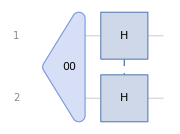

```mathematica
superposition=QuantumCircuitOperator[{"00","HH"},"Label"->"+^(⊗4)"];
superposition["Diagram",ImageSize->Small]
```

We apply a Hadamard gate (H) to each qubit, This transforms the initial state 0 of all qubits into a superposition of all possible cuts:

```mathematica
superposition["Formula"]
```

1/2 00+1/2 01+1/2 10+1/2 11

```mathematica
superposition["Probabilities"]
```

<|00→1/4,01→1/4,10→1/4,11→1/4|>

Some initial intuition comes from our first example, which involves identifying a periodic pattern, such as 0101 or 1010, within a bitstring.

To achieve this, we need to establish connections between nodes or qubits that reflect the structure of the cost Hamiltonian. For this initial idea, we can evaluate the gate sequence CNOT + RZ + CNOT.

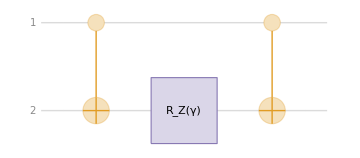

```mathematica
qcrzz=QuantumCircuitOperator[{"CNOT","RZ"[γ]->{2},"CNOT"},"Label"->"Cost"];
qcrzz["Diagram"]
```

We can verify that it distinguish the possible correct solutions from the non-periodic bitstrings in order to solve the problem:

```mathematica
qcrzz[QuantumState["++"]]["Formula"]
```

1/2 ⅇ^(-(ⅈ γ)/2)00+1/2 ⅇ^((ⅈ γ)/2)01+1/2 ⅇ^((ⅈ γ)/2)10+1/2 ⅇ^(-(ⅈ γ)/2)11

We can gain some initial insights and visualize the differences in the solution amplitudes in the following plot:

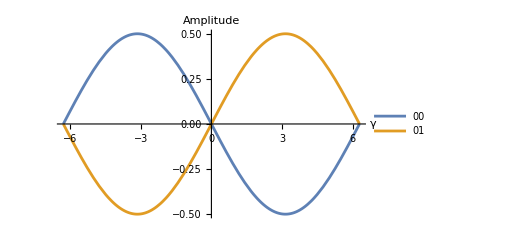

```mathematica
Plot[Evaluate[Im[Values[#]]],{γ,-2π,2π},]&@Normal[qcrzz[QuantumState["++"]]["Amplitudes"]][[;;2]]
```

The concept becomes clearer when we observe that the probabilities of regular bitstrings are minimal when the probabilities of periodic bitstrings are maximal, and vice versa:

```mathematica
qcrzz[QuantumState["++"]]["Probability"]
```

<|00→ⅇ^Im[γ]/(4 (1/2 ⅇ^(-Im[γ])+ⅇ^Im[γ]/2)),01→ⅇ^(-Im[γ])/(4 (1/2 ⅇ^(-Im[γ])+ⅇ^Im[γ]/2)),10→ⅇ^(-Im[γ])/(4 (1/2 ⅇ^(-Im[γ])+ⅇ^Im[γ]/2)),11→ⅇ^Im[γ]/(4 (1/2 ⅇ^(-Im[γ])+ⅇ^Im[γ]/2))|>

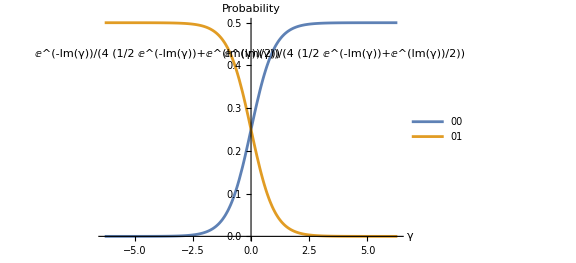

```mathematica
Plot[Evaluate[Values[#]/.Im[γ]:>γ],{γ,-2π,2π},]&@Normal[qcrzz[QuantumState["++"]]["Probability"][[;;2]]]
```

The set of gates outlined earlier is commonly referred to as an RZZ gate, which combines rotations and controlled operations:

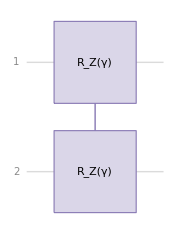

```mathematica
QuantumCircuitOperator[{{"R",γ,"ZZ"}}]["Diagram",ImageSize->Small]
```

```mathematica
QuantumCircuitOperator[{{"R", γ, "ZZ"}}]["Table"]
```

| 00 | 01 | 10 | 11
00 | ⅇ^(-(ⅈ γ)/2) | 0 | 0 | 0
01 | 0 | ⅇ^((ⅈ γ)/2) | 0 | 0
10 | 0 | 0 | ⅇ^((ⅈ γ)/2) | 0
11 | 0 | 0 | 0 | ⅇ^(-(ⅈ γ)/2)

Now that we understand this, we can apply it to every pair of qubits connected in the graph. In other words, we apply the RZZ gate to every edge in the graph. This ensures that the quantum state evolves according to the problem constraints.

The previous step does not explore all possible cuts because some amplitudes remain unchanged, so we need to mix things a little bit!

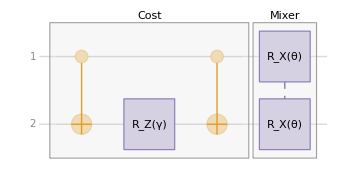

```mathematica
miniMixer=QuantumCircuitOperator[{"RX"[θ]->{1,2}},"Label"->"Mixer"];
miniqaoa=QuantumCircuitOperator[{qcrzz,miniMixer}];
miniqaoa["Diagram"]
```

Visualize the symbolic function corresponding to each possible state:

```mathematica
miniqaoa["Simplify"]["Table"]
```

| 00 | 01 | 10 | 11
00 | ⅇ^(-(ⅈ γ)/2) Cos[θ/2]^2 | -1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ] | -1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ] | -ⅇ^(-(ⅈ γ)/2) Sin[θ/2]^2
01 | -1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ] | ⅇ^((ⅈ γ)/2) Cos[θ/2]^2 | -ⅇ^((ⅈ γ)/2) Sin[θ/2]^2 | -1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ]
10 | -1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ] | -ⅇ^((ⅈ γ)/2) Sin[θ/2]^2 | ⅇ^((ⅈ γ)/2) Cos[θ/2]^2 | -1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ]
11 | -ⅇ^(-(ⅈ γ)/2) Sin[θ/2]^2 | -1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ] | -1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ] | ⅇ^(-(ⅈ γ)/2) Cos[θ/2]^2

Considering the initial state preparation, we recover a mini-QAOA:

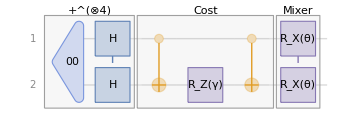

```mathematica
miniqaoa[superposition]["Diagram"]
```

The increased expressibility of the resulting state from this ansatz, as compared to previous circuits, comes from the final mixing performed by the mixing layer of gates:

```mathematica
miniqaoa[superposition]["Simplify"]["Table"]
```

| 1
00 | ⅇ^(-(ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ]
01 | ⅇ^((ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ]
10 | ⅇ^((ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^(-(ⅈ γ)/2) Sin[θ]
11 | ⅇ^(-(ⅈ γ)/2) (1/2 Cos[θ/2]^2-1/2 Sin[θ/2]^2)-1/2 ⅈ ⅇ^((ⅈ γ)/2) Sin[θ]

From the following plot, we can observe how the probabilities for regular and periodic bitstrings oscillate, similar to the previous plots. The new parameter θ does not interfere with this behavior; instead, it expands the parameter space, providing additional expressibility to our ansatz:

```mathematica
Plot3D[Evaluate[ComplexExpand@Values[#]],{γ,-2π,2π},{θ,-π,π},PlotLegends->Keys[#],AxesLabel->{"γ","θ","Probability"}]&@Normal[miniqaoa[superposition]["Probabilities"][[;;2]]]
```

-Graphics3D-

##### Step–by–Step: 4-Edge Graph Example

Find the Max-Cut for the following graph:

```mathematica
g=Graph[Range[4],UndirectedEdge@@@{{1,2},{1,4},{2,3},{3,4}},]
```

-Graphics-

Implement the Cost Hamiltonian:

```mathematica
Hc=QuantumOperator[1/2("IIII"-"ZZII")+1/2("IIII"-"IZZI")+1/2("IIII"-"IIZZ")+1/2("IIII"-"ZIIZ")]
```

QuantumOperator[…]

Initial state preparation for superposition:

```mathematica
stateprep=QuantumCircuitOperator[{"0000","H"->{1,2,3,4}},"Label"->"+^(⊗4)"];
```

We can use Wolfram Mathematica's Graph functionalities to establish connections between qubits within the Cost-Circuit:

```mathematica
qpairs=List@@@EdgeList[g]
```

{{1,2},{1,4},{2,3},{3,4}}

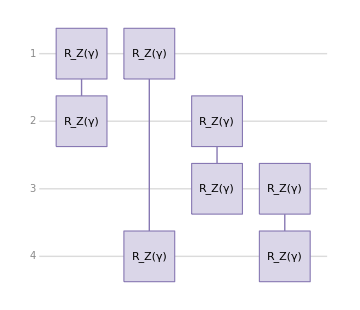

```mathematica
qcost=QuantumCircuitOperator[Map[{"R",γ,"ZZ"}->#&,qpairs],"Parameters"->{γ},"Label"->"U_Cost"];
qcost["Diagram"]
```

This layer of gates actually corresponds to the operator generated by the Cost Hamiltonian we defined earlier:

H_c=1/2∑_(𝒾,𝒿 ∈ V) (𝟙-Z_𝒾 Z_𝒿)->U_Cost=∏_(𝒾,𝒿) ⅇ^(-(ⅈ t)/2*(𝟙-Z_𝒾 Z_𝒿))

```mathematica
qcost==(ⅇ^(-2 ⅈ t)*ⅇ^(ⅈ*t*Hc))
```

True

To ensure full exploration, we need a mixer Hamiltonian that allows transitions between different states:

H_M=∑_(𝒿 ∈ V) X_j->U_Mixer=∏_(𝒿=1)^n ⅇ^(-ⅈθ*X_𝒿)

```mathematica
mixer=QuantumCircuitOperator[{"RX"[θ] -> VertexList[g]}, "Label" -> "U_Mixer","Parameters"->{θ}];
```

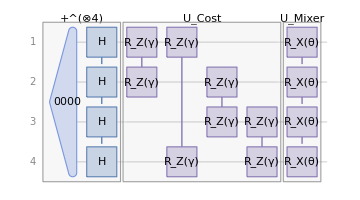

```mathematica
qaoa=QuantumCircuitOperator[{stateprep,qcost,mixer},"Parameters"->{θ,γ}];
qaoa["Diagram"]
```

Define the variational states to calculate the Cost function:

```mathematica
ϕ=qaoa[];ϕ=SuperDagger[ϕ];
```

```mathematica
costfunction=FullSimplify[ϕ@Hc@ϕ,{θ,γ}∈Reals]["Scalar"]
```

2-4 Cos[γ] Cos[θ] Sin[γ] Sin[θ]

Let's try out the NMaximize optimizer:

```mathematica
qaoaOpt=NMaximize[costfunction,{θ,γ}]
```

{3.,{θ→-0.785398,γ→0.785398}}

Visualize the most probable solutions:

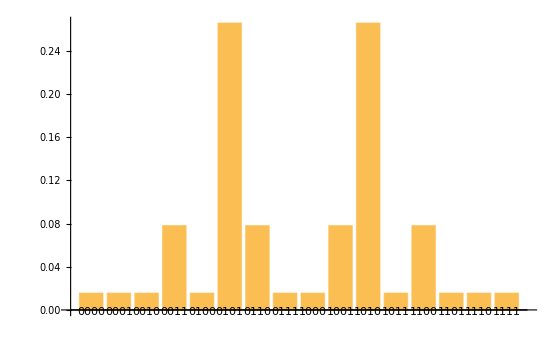

```mathematica
qaoa[<|Last@qaoaOpt|>][]["ProbabilityPlot"]
```

We obtain an initial approximate result. We detect that the solutions with higher probability are the correct answers. However, the exact solution for this problem is C=4, so we haven't reached the desired outcome yet.

We can enhance the precision of our solution by increasing the number of QAOA layers. This is easy to do since we can use QuantumCircuitOperator with the previous circuit but replacing the parameters:

```mathematica
twolayers=QuantumCircuitOperator[{stateprep,qcost[γ1],mixer[θ1]->{1,2,3,4},qcost[γ2],mixer[θ2]->{1,2,3,4}},"Parameters"->{γ1,γ2,θ1,θ2}];
```

We can utilize the Parameters option from the Wolfram Quantum Framework to re-name the gate parameters, allowing us to distinguish one layer from another.

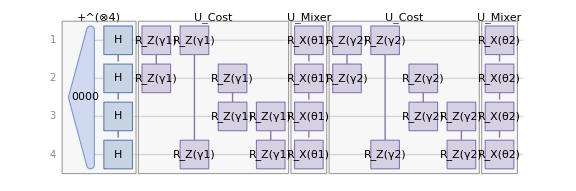

```mathematica
twolayers["Diagram",ImageSize->Large]
```

Implement the cost function:

```mathematica
Φ=twolayers[];Φ=SuperDagger[Φ];
```

```mathematica
costFunction=FullSimplify[Φ@Hc@Φ,{γ1,γ2,θ1,θ2}∈ Reals]["Scalar"]
```

1/4 (8-Cos[2γ1-2 θ1]+Cos[2 (γ1+θ1)]+4 (Cos[γ1+2 γ2]-2 Cos[γ2] Cos[γ1+γ2] Cos[2 θ2]) Sin[γ1] Sin[2 θ1]-2 ((Cos[γ1-2 γ2]+3 Cos[γ1+2 γ2]) Cos[2 θ1] Sin[γ1]+2 Cos[γ1]^2 Sin[2 γ2]) Sin[2 θ2])

Optimimize:

```mathematica
result=NMaximize[costFunction,{θ1,θ2,γ1,γ2}]
```

{4.,{θ1→1.11852,θ2→0.904557,γ1→-0.904557,γ2→-1.11852}}

Now, we obtain the exact result.

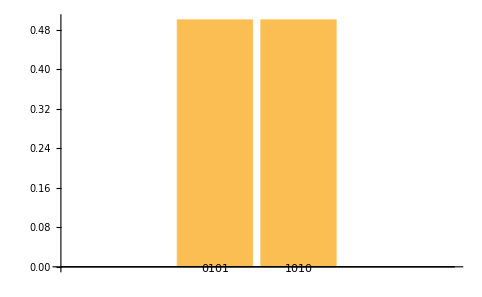

```mathematica
twolayers[<|Last@result|>][]["ProbabilityPlot"]
```

This solution represents the cut shown in the first image of this section:

```mathematica
Replace[cut,-1->0,{9}]
```

-Graphics-

We can see that 0101 is represented in this image by reading the nodes according to their indexing order. A symmetric solution can be obtained by renaming the nodes to 1010. Ultimately, what matters most is that the qubits are divided into two distinct sets, labeled as 0 or 1.

##### Example: 5-Edge Graph

With a clear understanding of each step involved in solving the Max-Cut problem using QAOA, we are now ready to proceed with the direct implementation of the solution.

Find the Max-Cut for the following graph:

```mathematica
g2=Graph[Range[4],UndirectedEdge@@@{{1,2},{1,3},{2,3},{2,4},{3,5},{4,5}},]
```

-Graphics-

In this more challenging example, we will generate the Hamiltonian programmatically instead of writing it explicitly:

```mathematica
index2=MapApply[List,EdgeRules[g2]]/.x_Integer:>{x,x};
op𝟙2=StringRepeat["I",VertexCount[g2]];
sum2=Total[1/2(op𝟙2-StringReplacePart[op𝟙2,"Z",#])&/@index2]
```

(IIIII-IIIZZ)/2+(IIIII-IIZIZ)/2+(IIIII-IZIZI)/2+(IIIII-IZZII)/2+(IIIII-ZIZII)/2+(IIIII-ZZIII)/2

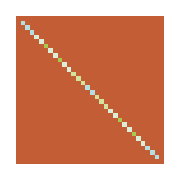

```mathematica
Hc2=QuantumOperator[sum2];
ArrayPlot[Hc2["Matrix"],ColorFunction->"IslandColors",ImageSize->Small]
```

Implement directly the QAOA circuit using the Graph functionalities:

```mathematica
qaoa2=QuantumCircuitOperator[{
"0"->VertexList[g2],
"H"->VertexList[g2],
Sequence@@Map[{"R",γ,"ZZ"}->#&,List@@@EdgeList[g2]],
"RX"[θ]->VertexList[g2]
},
"Label"->None,"Parameters"->{θ,γ}];
```

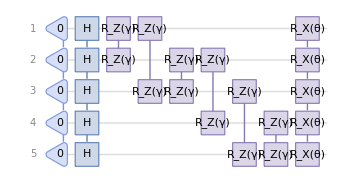

```mathematica
qaoa2["Diagram"]
```

Implement the symbolic cost function using the Cost Hamiltonian and the resulting parametrized state from the previous circuit:

```mathematica
ϕ2=qaoa2[];ϕ2=SuperDagger[ϕ2];
```

```mathematica
costfunction2=FullSimplify[ϕ2@Hc2@ϕ2,{γ,θ}∈Reals]["Scalar"]
```

1/32 (95+4 Cos[3 γ]+Cos[4 γ]+4 Cos[γ] (-1+4 Cos[2 θ] Sin[γ]^2)+2 Cos[2 θ] Sin[2 γ]^2-24 Cos[θ] (Sin[γ]+2 Sin[2 γ]+Sin[3 γ]) Sin[θ])

Use NMaximize for the optimization:

```mathematica
result2=NMaximize[costfunction2,{θ,γ}]
```

{4.30338,{θ→-35.2538,γ→-2.23284×10^27}}

We obtain multiple possible solutions; however, with just a single QAOA layer, we observe four solutions with higher probability:

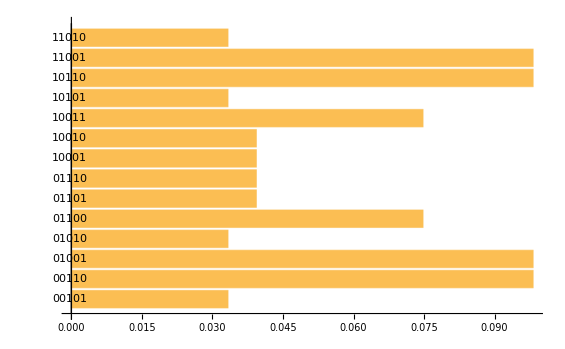

```mathematica
(qaoa2 @@ Values[Last[result2]])["ProbabilityPlot", BarOrigin -> Left,"Range"->{.02,1}]
```

Solve it clasically:

```mathematica
FindMaximumCut[g2]
```

{5,{{2,5},{1,3,4}}}

The quantum algorithm does not achieve the maximum value compared to the classical solution, but we can analyze the four most probable solutions indicated by the ProbabilityPlot:

```mathematica
ReverseSortBy[Normal[(qaoa2 @@ Values[Last[result2]])["Probabilities"]],#[[2]]&][[;;4]]
```

{10110→0.0982091,00110→0.0982091,11001→0.0982091,01001→0.0982091}

Following the labels in the vertex, the solution 10110 is the one found by the classical method. The following diagram corresponds to this solution:

```mathematica
maxcut2=HighlightGraph[g2,(Subgraph[g2,#1]&)/@Last[FindMaximumCut[g2]],];cut2=Show[{maxcut2,},];
GraphicsRow[{g2,cut2},ImageSize->Large]
```

-Graphics-

##### Example: 6-Edge Graph

Find the Max-Cut for the following graph:

```mathematica
g3=Graph[Range[5],UndirectedEdge@@@{{1,2},{1,3},{2,3},{2,4},{3,5},{4,5},{4,6}},GraphStyle->"NameLabeled",EdgeStyle->Directive[Black,Thick],ImageSize->Medium]
```

-Graphics-

In this more challenging example, we have a graph with six nodes, which results in a much larger cost Hamiltonian:

```mathematica
index3=MapApply[List,EdgeRules[g3]]/.x_Integer:>{x,x};
op𝟙3=StringRepeat["I",VertexCount[g3]];
sum3=Total[1/2(op𝟙3-StringReplacePart[op𝟙3,"Z",#])&/@index3]
```

(IIIIII-IIIZIZ)/2+(IIIIII-IIIZZI)/2+(IIIIII-IIZIZI)/2+(IIIIII-IZIZII)/2+(IIIIII-IZZIII)/2+(IIIIII-ZIZIII)/2+(IIIIII-ZZIIII)/2

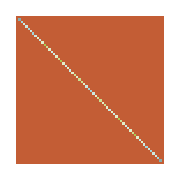

```mathematica
Hc3=QuantumOperator[sum3];
ArrayPlot[Hc3["Matrix"],ColorFunction->"IslandColors",ImageSize->Small]
```

Implement directly the QAOA circuit using the Graph functionalities:

```mathematica
qaoa3=QuantumCircuitOperator[{
"0"->VertexList[g3],
"H"->VertexList[g3],
Sequence@@Map[{"R",γ,"ZZ"}->#&,List@@@EdgeList[g3]],
"RX"[θ]->VertexList[g3]
},
"Label"->None,"Parameters"->{θ,γ}];
```

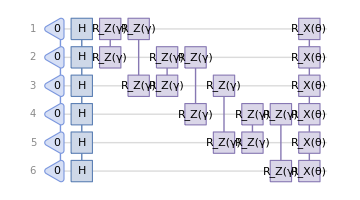

```mathematica
qaoa3["Diagram"]
```

Implement the symbolic cost function using the Cost Hamiltonian and the resulting parametrized state from the previous circuit:

```mathematica
ϕ3=qaoa3[];ϕ3=SuperDagger[ϕ3];
```

```mathematica
costfunction3="Scalar"//ϕ3@Hc3@ϕ3//ComplexExpand//Simplify
```

1/64 (222-8 Cos[γ]+8 Cos[3 γ]+2 Cos[4 γ]-22 Cos[γ-2 θ]-22 Cos[3 γ-2 θ]-Cos[4 γ-2 θ]-16 Cos[2 (γ-θ)]+2 Cos[2 θ]+16 Cos[2 (γ+θ)]-Cos[2 (2 γ+θ)]+30 Cos[γ+2 θ]+14 Cos[3 γ+2 θ])

Use NMaximize for the optimization:

```mathematica
result3=NMaximize[costfunction3,{θ,γ}]
```

{4.80604,{θ→-27.5566,γ→-32.0652}}

We obtain multiple possible solutions; however, with just a single QAOA layer, we observe four solutions with higher probability:

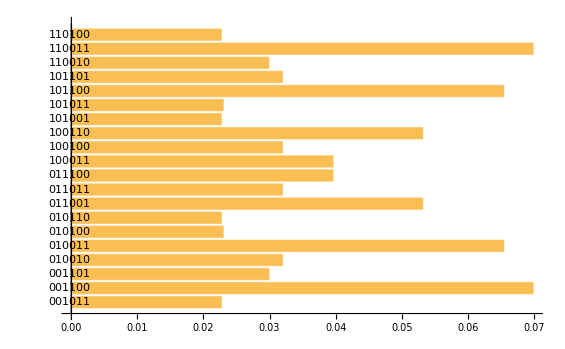

```mathematica
(qaoa3@@ Values[Last[result3]])["ProbabilityPlot", BarOrigin -> Left,"Range"->{.02,1}]
```

Solve it clasically:

```mathematica
FindMaximumCut[g3]
```

{6,{{2,5,6},{1,3,4}}}

The quantum algorithm does not achieve the maximum value compared to the classical solution, but we can analyze the four most probable solutions indicated by the ProbabilityPlot:

```mathematica
ReverseSortBy[Normal[(qaoa3 @@ Values[Last[result3]])["Probabilities"]],#[[2]]&][[;;4]]
```

{110011→0.0699094,001100→0.0699094,101100→0.0654777,010011→0.0654777}

Following the labels in the vertex, the solution 010011 is the one found by the classical method. The following diagram corresponds to this solution:

```mathematica
maxcut3=HighlightGraph[g3,(Subgraph[g3,#1]&)/@Last[FindMaximumCut[g3]],VertexLabels->];cut3=Show[{maxcut3,},];
GraphicsColumn[{g3,cut3},ImageSize->Medium]
```

-Graphics-

#### QAOA-in-QAOA

To tackle large graphs, we use a method called QAOA-in-QAOA, inspired by the Divide and Conquer algorithm.

Here’s the idea:

First, we partition the graph into smaller subgraphs.

Next, we solve a mini-QAOA on each subgraph and combine the solutions.

Then, to correct any possible issue with the solutions between the subgraphs, we treat each subgraph as a node in a new coarse-grained graph.

Finally, we apply QAOA again to this higher-level graph and correct the final solution.

This process is recursive and scalable, making it suitable for large problem instances.

Now let’s see how the Wolfram Quantum Framework enables us to symbolically model and analyze this algorithm. Given the following graph:

```mathematica
𝓍1=UndirectedEdge@@@{{1,2},{2,3},{3,4},{2,4},{1,3}};
𝓍2=UndirectedEdge@@@(4+{{1,2},{2,3},{3,4},{1,4},{2,4},{1,3}});
𝓍3=UndirectedEdge@@@(8+{{1,2},{2,3},{3,1}});
𝓍4=UndirectedEdge@@@(11+{{1,2}});
connection=UndirectedEdge@@@{{4,11},{10,7},{9,12},{13,5},{3,7},{1,8}};
edges={𝓍1,𝓍2,𝓍3,𝓍4};
fullEdges=Flatten[{{𝓍4,𝓍2,𝓍1,𝓍3},connection}];
g=Graph[fullEdges,PlotTheme->"NameLabeled",EdgeWeight->Thread[fullEdges->1]]
```

-Graphics-

Given the following partition:

```mathematica
subgraphs=Graph[#,EdgeWeight->Thread[Rule[#,1]],]&/@edges;
gsub=HighlightGraph[fullEdges,subgraphs,]
```

-Graphics-

### Divide (Subgraphs)

We load the Hamiltonian for each minigraph:

```mathematica
subweights=<|Thread[List@@@EdgeList[#]->PropertyValue[#,EdgeWeight]]|>&/@subgraphs;
subHc=Total[Table[1/2#[i]*(QuantumOperator["I",i]-QuantumOperator["Z",i]),{i,Keys@#}]]&/@subweights
```

{QuantumOperator[…],QuantumOperator[…],QuantumOperator[…],QuantumOperator[…]}

We then construct symbolic QAOA circuits, with qubit indices mapping directly to graph nodes:

```mathematica
subQAOA=QuantumCircuitOperator[{
"+"->VertexList[#1],
Sequence@@({"R",t,"ZZ"}->#1&)/@List@@@EdgeList[#1],
"RX"[θ]->VertexList[#1]
},
"Label"->None,"Parameters"->{θ,t}]&/@subgraphs;
```

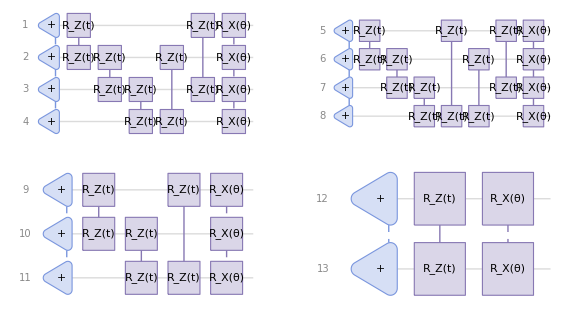

```mathematica
GraphicsGrid[Partition[#["Diagram","ShowEmptyWires"->False]&/@subQAOA,2],ImageSize->Large]
```

After simulating the states, we can observe how the symbolic computation can give insights about cost functions for each subgraph. We can visualize the parameter space using contour plots, giving us deep insight into the optimization behavior.

```mathematica
QAOAstates=QuantumOperator[#]["State"]&/@subQAOA;
```

```mathematica
subcost=Module[{ket,bra,hc},ket=#1⟦2⟧["StateVector"];bra=SuperDagger[#1⟦2⟧]["StateVector"];hc=#1⟦1⟧["Matrix"];(bra.hc.ket)//ComplexExpand//FullSimplify]&/@Thread[{subHc,QAOAstates}];
```

```mathematica
contours=ContourPlot[#,{θ,-π,π},{t,-π,π},Contours->10,ImageSize->Small]&/@subcost;
```

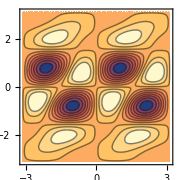
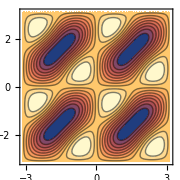
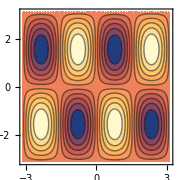
-Graphics- | -Graphics-
1/16 (-2 sin(2 θ) (3 sin(t)+4 sin(2 t)+3 sin(3 t))+4 cos(t) (2 cos(2 θ) sin^2(t) (cos(t)+2)-1)+4 cos(3 t)+cos(4 t)+39) | 
-Graphics- | -Graphics-
3/8 (-8 sin(2 θ) sin(t) cos^2(t)+2 cos(2 θ) sin^2(2 t)+cos(4 t)+7) | 
-Graphics- | -Graphics-
3/8 (-2 sin(2 θ) sin(2 t)+2 cos(2 θ) sin^2(t)+cos(2 t)+3) | 
-Graphics- | -Graphics-
1/2-sin(θ) cos(θ) sin(t) |

```mathematica
sg=Subgraph[gsub,#,ImageSize->Small]&/@{Range[4],Range[5,8],{9,10,11},{12,13}};
minigrids=Grid[{{#[[1]],#[[2]]},{Text[#[[3]],FormatType->TraditionalForm],SpanFromLeft}},Frame->All,Background->{White,{None,Lighter[Yellow,.9]}},ItemStyle->#[[4]]]&/@Thread[{sg,contours,subcost,{8,12,12,12}}];
Grid[List/@minigrids,Frame->All,BaselinePosition->Baseline,Alignment->Top,Background->Lighter[Blend[{Blue,Green}],.8]]
```

After just a single QAOA layer, we already discover useful solutions:

```mathematica
subres=NMaximize[#,{θ,t}]&/@subcost;
```

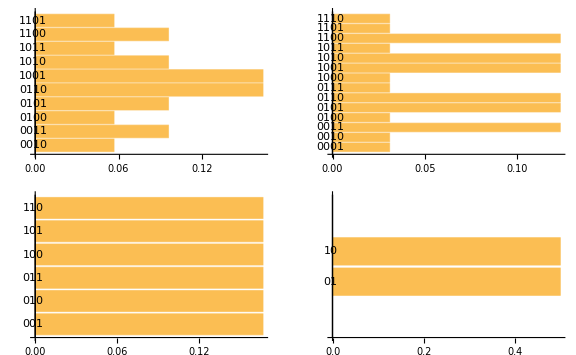

```mathematica
result=(#1⟦1⟧@@Values[Last[#1⟦2⟧]]&)/@Thread[{subQAOA,subres}];
GraphicsGrid[Partition[#["ProbabilityPlot", ]&/@result,2],ImageSize->Large]
```

Each minigraph contributes to a partial solution, illustrated by colored nodes yellow and red:

```mathematica
states=Keys@ReverseSortBy[#["Probabilities"],#[[2]]]&/@result;
groups=Map[states⟦Sequence@@##1⟧⟦1⟧&,{{1,2},{2,6},{3,1},{4,1}}];
solution=Flatten[Thread/@Thread[(First[#1["Order"]]&)/@subQAOA->groups]];
minig=Graph[g,];incompleteHigh=HighlightGraph[minig,];
GraphicsRow[{gsub,incompleteHigh},ImageSize->Full]
```

-Graphics-

### Conquer (Big graph)

In the Conquer phase, we construct a new graph where each node represents a subgraph, and the edges are based on their prior connections:

```mathematica
as=<|solution|>;
bigEdges=Complement[EdgeList[g],Flatten[EdgeList/@Map[Subgraph[g,#]&,edges]]];
smallToBig=Flatten[Thread/@Thread[VertexList/@{𝓍1,𝓍2,𝓍3,𝓍4}->Range[4]]];
bigedges=EdgeList[bigEdges]/.z:UndirectedEdge[x_,y_]:>Rule[z/.smallToBig,(-1)^as[x]*(-1)^as[y]]//Merge[#,Total]&//Normal;
g2=Graph[Reverse@#[[All,1]],EdgeWeight->#,EdgeLabels->"EdgeWeight",EdgeLabelStyle->20,PlotTheme->"NameLabeled",VertexStyle->{1 -> Hue[0,0.57,0.78,0.4], 2 ->Hue[0.15,0.82,0.87,0.4],3->Hue[0.75,0.5,0.66,0.4],4->Hue[0.05,0.62,0.87,0.6]},ImageSize->Medium]&@bigedges;
ggg=Show[{Graphics[{
Hue[0.15,0.82,0.87,0.4],Disk[{1.7,0.5},0.8],
Hue[0,0.57,0.78,0.4],Disk[{0.45,1.8},{0.8,1}],
Hue[0.75,0.5,0.66,0.4],Disk[{2.43,2.5},0.75],
Hue[0.05,0.62,0.87,0.6],Disk[{3.65,1.4},{0.3,1}]
}],incompleteHigh
}];
GraphicsRow[{ggg,g2},ImageSize->10^2.9]
```

-Graphics-

We then assign weights based on inter-subgraph interactions and repeat the QAOA process at this higher level:

```mathematica
subweights2=<|Thread[List@@@EdgeList[#]->(1-PropertyValue[#,EdgeWeight])/2]|>&@g2;
```

```mathematica
subHc2=Total[Table[1/2#[i]*(QuantumOperator["I",i]-QuantumOperator["Z",i]),{i,Keys@#}]]&@subweights2;
```

```mathematica
subQAOA2=QuantumCircuitOperator[{
"+"->VertexList[#1],
Sequence@@({"R",t,"ZZ"}->#1&)/@List@@@EdgeList[#1],
"RX"[θ]->VertexList[#1]
},
"Label"->None,"Parameters"->{θ,t}]&@g2
```

QuantumCircuitOperator[…]

```mathematica
QAOAstates2=QuantumOperator[#]["State"]&@subQAOA2;
subcost2=("Scalar"//SuperDagger[QAOAstates2]@subHc2["State"]@QAOAstates2)//ComplexExpand//Simplify
```

1/32 (22-Cos[t]+Cos[3 t]+2 Cos[4 t]-2 Cos[t-2 θ]-3 Cos[3 t-2 θ]-Cos[4 t-2 θ]-Cos[2 (t-θ)]+2 Cos[2 θ]+Cos[2 (t+θ)]-Cos[2 (2 t+θ)]+3 Cos[t+2 θ]+2 Cos[3 t+2 θ])

```mathematica
subres2=NMaximize[subcost2,{θ,t}];
```

Finally, we observe the resulting probability distribution and solve the MaxCut problem for the higher-level graph:

```mathematica
result2=subQAOA2["State"][<| Last[subres2]|>];
```

```mathematica
probplot=result2["ProbabilityPlot", ];
groups2=Part[Keys@ReverseSortBy[#["Probabilities"],#[[2]]],2][[1]]&@result2;
solution2=Flatten[Thread/@Thread[First[#["Order"]]&@subQAOA2->groups2]];
grouped2=HighlightGraph[g2,Map[Subgraph[g,#]&,GatherBy[solution2,Last][[All,All,1]]],];
GraphicsRow[{probplot,grouped2},ImageSize->Large]
```

-Graphics-

n the final step, we take the subgraphs that are yellow nodes in the higher level graph and flip their node values. For instance, in some subgraphs, yellow nodes may become red, as the global optimization balances local and global constraints.

```mathematica
flip=Keys[Select[solution2,MatchQ[#,Rule[_,1]]&]];
newsolution=#->1-as[#]&/@Keys[Select[smallToBig,MatchQ[#,Rule[_,Alternatives@@flip]]&]];
finalsolution=Normal[Association[Join@@{solution,newsolution}]];
finalsol=HighlightGraph[g,Map[Subgraph[g,#]&,GatherBy[finalsolution,Last][[All,All,1]]],]
```

-Graphics-

## Quantum Natural Gradient Descent

Gradient-based optimization methods represent a cornerstone in the field of numerical optimization, offering powerful techniques to minimize or maximize objective functions in various domains, ranging from machine learning and deep learning to physics and engineering. These methods utilize the gradient, or derivative, of the objective function with respect to its parameters to iteratively update them in a direction that reduces the function's value.

This section will  include a brief introduction to the Gradient Descent methods, the Fubini-Study metric tensor and Quantum Natural Gradient Descent. We will provide illustrative examples and compare these methods to regular gradient descent algorithms.

### Quantum Circuit Derivative?

Now, you might be wondering: how do we compute the derivative of a quantum circuit?

Great  question!  While  it  may  seem  complex  at  first, the  process  is  actually  quite  manageable,and, thanks  to  the  Parameter  Shift  Rule  (PSR), it  can  even  be  done  analytically!

PSR is a mathematical technique that enables the computation of a quantum circuit’s gradient by evaluating the expectation value twice, each time with one parameter shifted by a fixed amount.

The expected value of a circuit in relation to a measurement operator A varies smoothly with the circuit’s gate parameters θ:

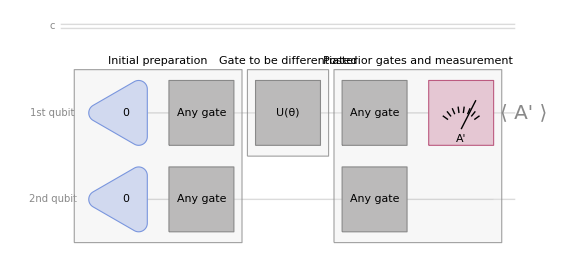

```mathematica
QuantumCircuitOperator[{
QuantumCircuitOperator[{"0",
"0"->{2},
QuantumOperator["RandomUnitary",{1},"Label"->"Any gate"],
QuantumOperator["RandomUnitary",{2},"Label"->"Any gate"]},"Label"->"Initial preparation"],
QuantumCircuitOperator[{QuantumOperator["PauliZ","Label"->"U(θ)"]},"Label"->"Gate to be differentiated"],
QuantumCircuitOperator[{
QuantumOperator["RandomUnitary",{1},"Label"->"Any gate"],
QuantumOperator["RandomUnitary",{2},"Label"->"Any gate"],
QuantumMeasurementOperator["PauliZ","Label"->"A'"]
},"Label"->"Posterior gates and measurement"]
}]["Diagram",ImageSize->Large,"WireLabels"->{{Placed["1st qubit",Left],Placed[Style["⟨ A' ⟩",FontSize->20],Right]},Placed["2nd qubit",Left]}]
```

Typically, the quantum circuit whose gradient we seek consists of multiple gates. Here, we’ll focus on computing the gradient for a specific type of unitary gate U(θ).

Any unitary gate can be cast in the form U=e^(iθ,G), where G is the Hermitian generator of the gate U.  Then let’s assume that every gate before it is the initial state and then every gate after is part of the measurement. Let’s call this expected value of A:

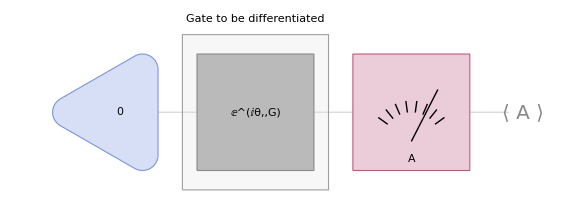

```mathematica
QuantumCircuitOperator[{
"0",
QuantumCircuitOperator[{QuantumOperator["RandomUnitary","Label"->"ⅇ^(ⅈθ,,G)"]},"Label"->"Gate to be differentiated"],
QuantumMeasurementOperator["Computational","Label"->"A"]
}]["Diagram",ImageSize->Large,"ShowMeasurementWire"->False,"WireLabels"->{Placed[Style["⟨ A ⟩",FontSize->20],Right]}]
```

In order to apply the parameter shift rule we need to “shift” our parameter for a given value, you can use pi/2. Then we calculate the difference between the shifted expected values of A:

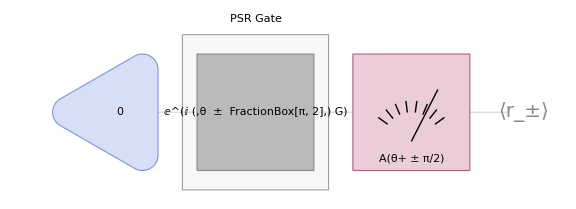

```mathematica
QuantumCircuitOperator[{
"0",
QuantumCircuitOperator[QuantumOperator["RandomUnitary","Label"->"ⅇ^(ⅈ (,θ  ±  FractionBox[π, 2],) G)"],"Label"->"PSR Gate"],
QuantumMeasurementOperator["Computational","Label"->"A(θ+ ± π/2)"]
}]["Diagram","ShowMeasurementWire"->False,ImageSize->Large,"WireLabels"->{Placed[Style["⟨r_±⟩",FontSize->20],Right]}]
```

The parameter–shift rule states that in order to obtain the derivative ∇_θ ⟨A⟩ from gate U, we need to compute:

∇_θ ⟨A⟩=1/2( ⟨A(θ+π/2)⟩-⟨A(θ-π/2)⟩ )

Let’s say that we have this simple circuit with a rotation in x with a measurement in Z:

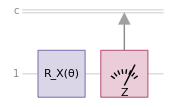

```mathematica
RXCircuit=QuantumCircuitOperator[{"RX"[θ],QuantumMeasurementOperator["Z"->{1,-1}]},"Parameters"->{θ}];
RXCircuit[θ]["Diagram",ImageSize->Small]
```

If we check the mean value it is:

```mathematica
RXCircuit[θ][]["Mean"]//ComplexExpand//Simplify
```

Cos[θ]

Applying the parameter shift rule shows that indeed we obtain the derivative:

```mathematica
1/2(RXCircuit[θ+π/2][]["Mean"]-RXCircuit[θ-π/2][]["Mean"])//ComplexExpand//Simplify
```

-Sin[θ]

The main benefit of Parameter Shift Rule is that it enables the use of the Gradient Descent optimizer for variational circuits.

#### Stochastic Parameter Shift–Rule

The Stochastic Parameter Shift Rule (SPSR) represents a powerful optimization technique specifically tailored for parameterized quantum circuits. Unlike conventional gradient-based methods, SPSR offers a stochastic approach to computing gradients, making it particularly well-suited for scenarios involving noisy quantum devices or large-scale quantum circuits. At its core, SPSR leverages the principles of quantum calculus to estimate gradients by probabilistically sampling from parameter space and evaluating the quantum circuit's expectation values. By incorporating random perturbations in parameter values and exploiting symmetry properties, SPSR effectively mitigates the detrimental effects of noise and provides robust optimization solutions.

SPSRGradientValues[GeneratorMatrix[θ], PauliOperator] | calculates the numeric derivative of a QuantumOperator corresponding to the Hermitian GeneratorMatrix. The PauliOperator correspond to the parameter θ being differentiated.

By the other hand, the Approximate Stochastic Parameter Shift Rule (ASPSR) emerges as a pragmatic solution to address the computational complexity associated with exact Stochastic Parameter Shift Rule (SPSR) calculations, particularly in scenarios involving high-dimensional parameter spaces or resource-constrained environments. ASPSR strategically balances computational efficiency with optimization accuracy by employing approximation techniques to streamline gradient estimation procedures. By leveraging simplified or truncated calculations while preserving the essential characteristics of SPSR, ASPSR facilitates faster gradient computations without significantly compromising optimization quality.

ASPSRGradientValues[GeneratorMatrix[θ], PauliOperator,H] | calculates the approximate derivative of a QuantumOperator corresponding to the Hermitian GeneratorMatrix. The PauliOperator correspond to the parameter θ being differentiated and H correspond to the operator associated with different parameters.

#### Example using SPSRGradientValues

For this example we will use the following generator:

G_CR(θ_1,θ_2,θ_3)=θ_1 X⊗𝟙 - θ_2 Z⊗X + θ_3 𝟙⊗X

```mathematica
generator=QuantumOperator[(θ1*QuantumOperator[{"X"->{1},"I"->{2}}]-θ2*QuantumOperator[{"Z"->{1},"X"->{2}}]+θ3*QuantumOperator[{"I"->{1},"X"->{2}}]),"Parameters"->{θ1,θ2,θ3}];
```

We will differentiate θ1. Implement the correspondant matrix fixing other parameters:

```mathematica
generatorMatrix[θ1_]=generator[<|θ2->0.15,θ3->1.6|>]["Matrix"]//Normal
```

{{0,1.45,θ1,0},{1.45,0,0,θ1},{θ1,0,0,1.75},{0,θ1,1.75,0}}

Calculate the gradient using SPSRGradientValues indicating the Pauli matrix associated with θ1:

```mathematica
generatorGradient=SPSRGradientValues[generatorMatrix,"PauliX"];
```

Check the result and find a suitable fit:

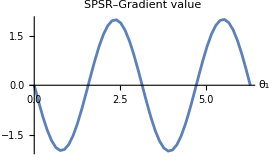

```mathematica
ListLinePlot[generatorGradient,AxesLabel->{"θ_1"},
PlotLabel->"SPSR–Gradient value",PlotRange->All]
```

```mathematica
Fit[generatorGradient,Table[Exp[ⅈ n θ],{n,-5,5}],θ]//Re//ComplexExpand//Chop[#,10^-2]&
```

-1.99009 Sin[2 θ]

#### Example using ASPSRGradientValues

For this example we will use the following generator:

G_CR(θ_1,θ_2,θ_3)=θ_1 X⊗𝟙 - θ_2 Z⊗X + θ_3 𝟙⊗X

```mathematica
generator=QuantumOperator[(θ1*QuantumOperator[{"X"->{1},"I"->{2}}]-θ2*QuantumOperator[{"Z"->{1},"X"->{2}}]+θ3*QuantumOperator[{"I"->{1},"X"->{2}}]),"Parameters"->{θ1,θ2,θ3}];
```

We will differentiate θ1. Implement the correspondant matrix fixing other parameters:

```mathematica
generatorMatrix[θ1_]=generator[<|θ2->0.15,θ3->1.6|>]["Matrix"]//Normal
```

{{0,1.45,θ1,0},{1.45,0,0,θ1},{θ1,0,0,1.75},{0,θ1,1.75,0}}

For this algorithm we need the operator not associated with θ1:

```mathematica
H=-0.15*QuantumOperator[{"Z"->{1},"X"->{2}}]+1.6*QuantumOperator[{"I"->{1},"X"->{2}}];
```

Calculate the gradient using SPSRGradientValues indicating the Pauli matrix associated with θ1 and the H opeator defined before:

```mathematica
generatorGradient=ASPSRGradientValues[generatorMatrix,"PauliX",H];
```

Check the result and find a suitable fit:

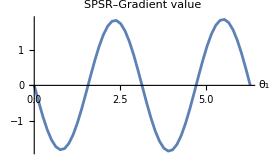

```mathematica
ListLinePlot[generatorGradient,AxesLabel->{"θ_1"},
PlotLabel->"SPSR–Gradient value",PlotRange->All]
```

```mathematica
Fit[generatorGradient,Table[Exp[ⅈ n θ],{n,-5,5}],θ]//Re//ComplexExpand//Chop[#,10^-1]&
```

-1.8499 Sin[2 θ]

### Gradient Descent

GradientDescent[f,{value_1,value_2,… }, opts]] | calculates the gradient descent of f using value_i as initial parameters.

From an analytical perspective, setting the gradient equal to zero and solving for the parameters would give us the solution. However, this is not something a computer can easily compute. Instead, computers rely on calculating the gradient to “move toward the minimum.”

One optimizer that stands out in this context is the well-known Gradient Descent!

Gradient Descent is a fundamental optimization technique used to minimize a function. It is widely used across various fields, such as machine learning, numerical optimization, and quantum computing.

The goal of Gradient Descent is to find the minimum of a cost function by adjusting the parameters iteratively in the direction of the steepest descent of the function being minimized as you can see in this image equation:

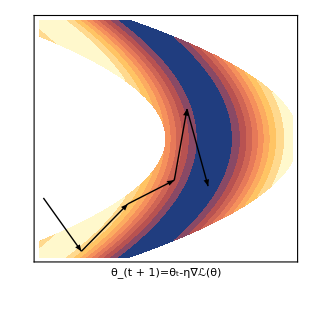

where ℒ(θ)  is the cost function with parameters θ, and η  is the step rate.

#### Workflow

Initialization

Begin with an initial set of parameters. This initial guess can either be random or from a heuristic approach.

Calculate the gradient ∇ℒ

Represented as the vector in the previous image, which are the partial derivatives of the objective function ℒ with respect to each parameter θ. The gradient indicates the direction of the steepest ascent.

Update parameters

Adjust the parameters in the opposite direction of the gradient to minimize the function. The update rule is the one in the image.

The learning rate, is a small positive scalar that controls the step size towards the minimum.

Iterate Until Convergence

Repeat steps 2 and 3 until a stopping criterion is satisfied.

The convergence criterion could be based on a threshold for changes in the function value or when the gradient’s magnitude falls below a specific limit, indicating that further updates won’t substantially improve the result. In some cases, steps 2 and 3 may simply be performed for a fixed number of iterations.

Also, selecting an appropriate learning rate is critical: if it’s too small, convergence will be slow; if it’s too large, it can lead to oscillations or even divergence.

#### Example

Implement a simple function

```mathematica
f[x_,y_]:=x^2+y^2
```

Set initial parameters and use GradientDescent to minimize the function:

```mathematica
initial={3,4};
```

```mathematica
parameters=GradientDescent[f,initial];
```

GradientDescent returns all the parameters obtained until convergence. We can check how the minimization evolved:

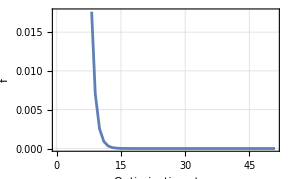

```mathematica
ListLinePlot[f@@@parameters,FrameLabel->{"Optimization steps","f"},
Frame->True,GridLines->Automatic]
```

The last parameters obtained correspond to the minimized function:

```mathematica
{f@@#,x->#[[1]],y->#[[2]]}&@Last[parameters]
```

{1.6333×10^-21,x→2.42484×10^-11,y→3.23313×10^-11}

We can contrast the result using NMinimize:

```mathematica
NMinimize[f[x,y],{x,y}]
```

{0.,{x→0.,y→0.}}

#### Options

"Gradient" | None | indicate correspondant gradient function ∇f to be used
"MaxIterations" | 50 | maximum number of iterations to use
"LearningRate" | 0.8 | step size taken during each iteration

##### Gradient

You can specify the correspondant gradient function ∇f:

```mathematica
df[x_,y_]=∇_{x,y} f[x,y]
```

{2 x,2 y}

```mathematica
parameters=GradientDescent[f,initial,"Gradient"->df];
```

```mathematica
{f@@#,x->#[[1]],y->#[[2]]}&@Last[parameters]
```

{1.6333×10^-21,x→2.42484×10^-11,y→3.23313×10^-11}

If the gradient is not specified,  it is calculated numerically using a center finite differnece algorithm.

##### MaxIterations

Specify the maximum number of iterations to use:

```mathematica
parameters1=GradientDescent[f,initial,"MaxIterations"->5];
parameters2=GradientDescent[f,initial,"MaxIterations"->15];
```

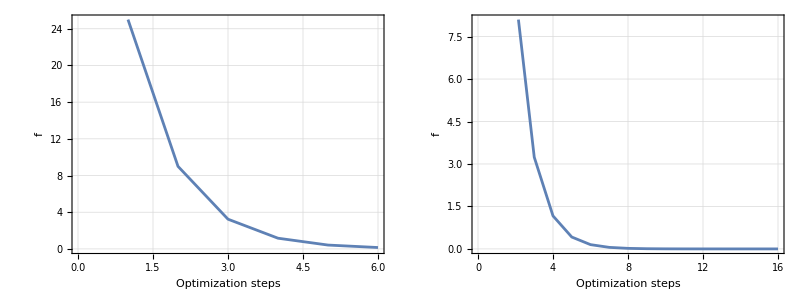

```mathematica
Grid[{
ListLinePlot[{f@@@#},
FrameLabel->{"Optimization steps","f"},
Frame->True,GridLines->Automatic,ImageSize->Small]&/@{parameters1,parameters2}}
]
```

##### LearningRate

Specify step size (η) taken during each iteration, compare the following gradient descent setups:

```mathematica
parameters1=GradientDescent[f,initial,"LearningRate"->0.9,"MaxIterations"->5];
parameters2=GradientDescent[f,initial,"LearningRate"->0.5,"MaxIterations"->5];
```

In this case, the optimization is done almost instantly by  "LearningRate" → 0.5:

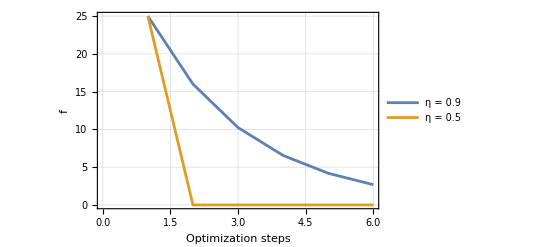

```mathematica
ListLinePlot[{f@@@parameters1,f@@@parameters2},FrameLabel->{"Optimization steps","f"},
PlotLegends->{"η = 0.9","η = 0.5"},
Frame->True,GridLines->Automatic]
```

We can visually verify that η = 0.9 was not efficent to find the solution:

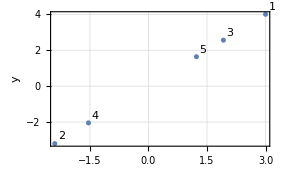

```mathematica
ListPlot[{
Table[Labeled[parameters1[[n]],n],{n,5}]
},
FrameLabel->{"x","y"},
Frame->True,GridLines->Automatic,PlotRange->All]
```

### Natural Gradient Descent

When using a regular gradient descent, we assume a flat or Euclidean parameter space. The algorithm does not consider the intrinsic geometry of the cost function, which can result in not–unique parametrizations which would lead to inefficient search for the minimum value, specially near to singular points.

To account for the geometry of our cost function, we can generalize the Gradient Descent to the Natural Gradient Descent by incorporating a metric tensor ℱ. Specifically, we utilize the inverse of the corresponding metric tensor to adjust the gradient direction. This approach can lead to improved optimization results.

The step of the Natural Gradient Descent is given by:

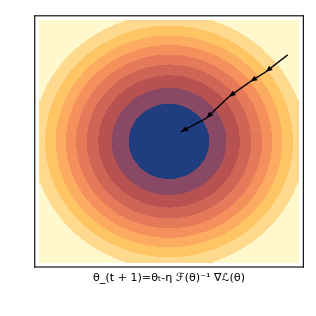

where η is the learning rate, ∇ℒ(θ) the gradient cost function and  ℱ(θ) the metric tensor that inform us about the geometry of parameter space.

### The Fubini–Study Metric Tensor

FubiniStudyMetricTensor[QuantumState[...] ,opts] | calculates the Fubini–Study metric tensor as defined by the VQE approach from a QuantumState with defined parameters

So what happens when we have a quantum optimization problem? When using a Quantum Variational Algorithm, we will face a similar problem. In this case the parameter space is defined in the space of quantum states.

In the search for a metric tensor for the quantum state space, we found the Fubini–Study metric tensor g_ij:

g_ij=Re(∂_i ψ∂_j ψ)-∂_i ψψψ∂_j ψ,∂_i ψ(θ)=∂_i ψ(θ)/∂θ_i

The Fubini-Study metric is a way to measure the “distance” between two quantum states, helping us understand how different or similar they are. For qubits, you can picture it as part of the way we understand their movement on the Bloch sphere.

In order to understand this, we should think about “distance” in the quantum state:

Definition for distance:

D,(x,y)>=0 and D,(x,y)=0 ⇔x=y

The distance between any two points is always greater than or equal to zero. Furthermore, the distance between two points is zero if and only if those two points are the same.

Symmetry: D,(x,y)=D,(y,x)

The distance between two points is the same regardless of the order in which we measure them. That is, the distance from x to y is equal to the distance from y to x.

Triangle inequality: D,(x,z)<=D,(x,y)+D,(y,z)

The distance between two points x and z must be less than or equal to the sum of the distances from x to y and from y to z

The first property is key for defining a correct distance function for quantum states.

How to define a distance between quantum states? Since two vectors of Hilbert space that differ by a constant actually correspond to the same quantum state, one would like to have a definition of distance that should be zero between states that differ by a constant, like ψ and ψ multiplied by a constant lambda.

Extra physical condition:

ψ≡λψ

This means that the distance will be defined in a projective Hilbert space. A projective space is obtained from a vector space by identifying vectors that differ by a nonzero factor. We need a differential form that does not distinguish parallel vectors ( this means that we are looking for a metric in projective space, which includes non-normalized states).

Now let’s consider dψ an infinitesimal variation of state ψ such that:

dψ_⊥=dψ-ψψ/ψψ dψ

which defines the component of the differential of psi orthogonal to the state psi. This equation becomes easier to understand when you refer to the vectors in the image:

Aiming to get rid of the “information” from the state projections:.

From normalizing this expression, the norm of this “measurement of changes in the projective space” gives the differential form of the distance which is the Fubini-Study metric:

ds_FS^2=(dψ_⊥dψ_⊥)/ψψ=dψdψ/ψψ-(|ψdψ|,^2)/ψψ^2

With this concept in mind, we can now understand how the formula for the Fubini-Study metric is derived. For further exploration of the theory, you can refer to literature on the Quantum Geometric Tensor.

Implement a simple single qubit state:

```mathematica
state=QuantumState[{Cos[θ1],Exp[2*I*θ2]*Sin[θ1]},"Parameters"->{θ1,θ2}]
```

QuantumState[…]

```mathematica
state["Formula"]
```

Cos[θ1]0+ⅇ^(2 ⅈ θ2) Sin[θ1]1

Let’s calculate the ket, bra and cost function by applying the VQE over a single Pauli X hamiltonian:

```mathematica
ClearAll[cost];
ψ=state["StateVector"];ψ=SuperDagger[state]["StateVector"];
cost=ψ.PauliMatrix[1].ψ//ComplexExpand//Simplify
```

Cos[2 θ2] Sin[2 θ1]

Now, we can calculate by ourselves the Fubini-Study metric tensor by calculating all the derivatives of ψ, in this case 2 for θ1 and θ2:

```mathematica
dψ=Table[D[ψ,i],{i,{θ1,θ2}}];
fubini=Table[
Re[ConjugateTranspose[dψ[[i]]] . dψ[[j]]]-(ConjugateTranspose[dψ[[i]]] . ψ)(ConjugateTranspose[ψ] . dψ[[j]]),			
{i,Length@dψ},{j,Length@dψ}
]//ComplexExpand//FullSimplify
```

{{1,0},{0,Sin[2 θ1]^2}}

Apply the FubiniStudyMetricTensor function to obtain the calculated QuantumOperator:

```mathematica
metric=FubiniStudyMetricTensor[state]
```

QuantumOperator[…]

```mathematica
FubiniStudyMetricTensor[state,"MatrixForm"]
```

(1 | 0
0 | Sin[2 θ1]^2)

The Fubini-Study metric tensor plays a crucial role in Quantum Natural Gradient Descent. Originating from the field of differential geometry, the Fubini-Study metric tensor enables the quantification of distances between quantum states on the complex projective Hilbert space.

#### Properties

"Matrix" | obtain the correspondant Fubini-Study metric tensor matrix in as a list.
"MatrixForm" | obtain the correspondant Fubini-Study metric tensor matrix in MatrixForm.
"Parameters" | obtain parameters used for the differentiation process.
"SparseArray" | obtain the correspondant Fubini-Study metric tensor matrix as a SparseArray.

Use "Matrix" and "MatrixForm" to obtain a simplified matrix expression which assumes Real-valued parameters:

```mathematica
FubiniStudyMetricTensor[state,"Matrix"]
```

{{1,0},{0,Sin[2 θ1]^2}}

```mathematica
FubiniStudyMetricTensor[state,"MatrixForm"]
```

(1 | 0
0 | Sin[2 θ1]^2)

Use "Parameters" to obtain the parameters pre-defined in the QuantumState used as input:

```mathematica
FubiniStudyMetricTensor[state,"Parameters"]
```

{θ1,θ2}

Use "SparseArray" for a non-simplified result:

```mathematica
FubiniStudyMetricTensor[state,"SparseArray"]
```

SparseArray[…]

Request them all using All as third argument:

```mathematica
FubiniStudyMetricTensor[state,All]
```

<|Result→QuantumOperator[…],Matrix→{{1,0},{0,Sin[2 θ1]^2}},MatrixForm→(1 | 0
0 | Sin[2 θ1]^2),Parameters→{θ1,θ2},SparseArray→SparseArray[…]|>

### Quantum Natural Gradient Descent

Quantum Natural Gradient Optimization Method represent a cutting-edge approach to optimizing parameterized quantum circuits in the field of quantum computing.  Unlike classical gradient-based methods, Quantum Natural Gradient techniques account for the unique geometry of the quantum state manifold, mitigating issues such as barren plateaus and enabling faster convergence rates.

The quantum state space features an invariant metric tensor referred to as the Fubini–Study metric tensor g_ij , which can be used to develop a quantum version of a natural gradient descent. Then each optimization step is given by:

θ_(t+1)= θ_t-η g^+(θ)∇ℒ(θ)

where g^+ the Fubini-Study metric tensor pseudo-inverse.

QuantumNaturalGradientDescent[f,metric ,opts] | calculates the gradient descent of f using the defined metric tensor for the parameters space.

We will briefly demonstrate how to apply all these functions in Wolfram quantum framework.

QuantumNaturalGradientDescent function follows the fundamental process of the Variational Quantum Eigensolver (VQE) which involves using a brief quantum circuit U(θ), characterized by parameters θ={θ_1,…θ_m} to iteratively adjust θ to minimize the average energy or cost function: f(θ)=ϕ(θ)Hϕ(θ) for the ansatz ϕ(θ,,,),,,,=U(θ,,)0.

#### Example

Implement a simple single qubit state:

```mathematica
state=QuantumState[{Cos[θ1],Exp[2*I*θ2]*Sin[θ1]},"Parameters"->{θ1,θ2}];
```

```mathematica
state["Formula"]
```

Cos[θ1]0+ⅇ^(2 ⅈ θ2) Sin[θ1]1

Calculate the Fubiny-Study metric tensor:

```mathematica
metric=FubiniStudyMetricTensor[state]
```

QuantumOperator[…]

```mathematica
FubiniStudyMetricTensor[state,"Matrix"]
```

{{1,0},{0,Sin[2 θ1]^2}}

Calculate a ϕ(θ)  state vector:

```mathematica
ϕ=state["StateVector"];ϕ=SuperDagger[state]["StateVector"];
```

Implement a cost function ⟨ϕ(θ)|H |ϕ(θ)⟩ :

```mathematica
cost[θ1_,θ2_]=ϕ.PauliMatrix[1].ϕ;
```

```mathematica
FullSimplify[cost[θ1,θ2],{θ1,θ2}∈Reals]
```

Cos[2 θ2] Sin[2 θ1]

Use QuantumNaturalGradientDescent to minimize the function:

```mathematica
qp=QuantumNaturalGradientDescent[cost,metric,"InitialPoint"->{π/12,π/12},"LearningRate"->0.05];
```

QuantumNaturalGradientDescent returns all the parameters obtained until convergence. We can check how the minimization evolved:

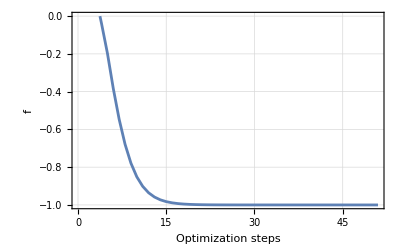

```mathematica
ListLinePlot[cost@@@qp,FrameLabel->{"Optimization steps","f"},
Frame->True,GridLines->Automatic]
```

Check optimization results:

```mathematica
Chop[{#,cost@@#}]&@Last[qp]
```

{{0.785368,1.5708},-1.}

#### Options

"Gradient" | None | indicate correspondant gradient function ∇f to be used
"InitialPoint" | Automatic | initial starting point for the optimization process
"LearningRate" | 0.8 | step size taken during each iteration
"MaxIterations" | 50 | maximum number of iterations to use

##### Gradient

You can specify the correspondant gradient function ∇f:

```mathematica
costgrad[θ1_,θ2_]=Grad[FullSimplify[cost[θ1,θ2],{θ1,θ2}∈Reals],{θ1,θ2}]
```

{2 Cos[2 θ1] Cos[2 θ2],-2 Sin[2 θ1] Sin[2 θ2]}

```mathematica
parameters=QuantumNaturalGradientDescent[
cost,metric,
"InitialPoint"->{π/12,π/12},
"LearningRate"->0.05,
"Gradient"->costgrad];
```

```mathematica
Chop[{#,cost@@#}]&@Last[parameters]
```

{{0.785368,1.5708},-1.}

If the gradient is not specified,  it is calculated numerically using a center finite differnece algorithm.

##### InitialPoint

Specify the initial point to start the iteration, compare the following gradient descent setups:

```mathematica
qp=QuantumNaturalGradientDescent[
cost,
metric,
"InitialPoint"->#,
"LearningRate"->0.1]&/@{{5π/12,π/12},{π/12,π/12}};
```

Analyze the parameters evolution with different starting point:

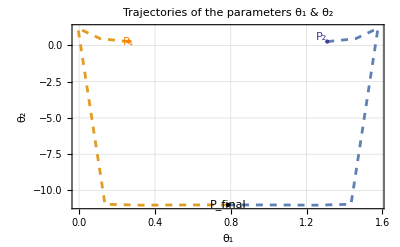

```mathematica
ListLinePlot[Chop[qp],PlotRange->All,PlotStyle->{{Dashed},{Dashed}},FrameLabel->{"θ_1","θ_2"},Frame->True,GridLines->Automatic,
PlotLabel->"Trajectories of the parameters θ_1 & θ_2",
Epilog->{
PointSize[Large],
Black,Point[{Re@Last@Last@qp}],
Text["P_final",Re@Last@Last@qp,{0,-2.5}],
Orange,Point[{{π/12,π/12}}],
Text["P_1",{π/12,π/12},{-2,-1}],
Hue[0.67, 0.6, 0.6],Point[{{(5π)/12,π/12}}],
Text["P_2",{(5π)/12,π/12},{2.5,-1}]

}
]
```

##### LearningRate

Specify step size (η) taken during each iteration, compare the following gradient descent setups:

```mathematica
qp=QuantumNaturalGradientDescent[cost,metric,"InitialPoint"->{π/12,π/12},"LearningRate"->#]&/@{0.1,0.5};
```

In this case, the optimization is done almost instantly by  "LearningRate" → 0.1:

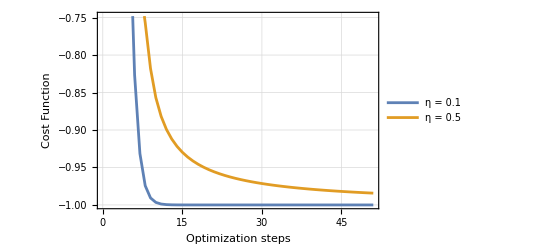

```mathematica
ListLinePlot[{cost@@@First[qp],cost@@@Last[qp]},FrameLabel->{"Optimization steps","Cost Function"},
PlotLegends->{"η = 0.1","η = 0.5"},
Frame->True,GridLines->Automatic]
```

Verify the trajectory generated by "LearningRate" → 0.5 and "LearningRate" → 0.1:

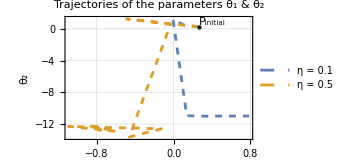

```mathematica
ListLinePlot[Re@qp,PlotRange->All,PlotStyle->{{Dashed},{Dashed}},FrameLabel->{"θ_1","θ_2"},Frame->True,GridLines->Automatic,
PlotLabel->"Trajectories of the parameters θ_1 & θ_2",PlotLegends->{"η = 0.1","η = 0.5"},Epilog->{Black,Point[{{π/12,π/12}}],
Text["P_initial",{π/12,π/12},{-1,-1}]}]
```

##### MaxIterations

Specify the maximum number of iterations to use:

```mathematica
qp=QuantumNaturalGradientDescent[cost,metric,
"LearningRate"->0.05,"InitialPoint"->{π/12,π/12},"MaxIterations"->#]&/@{5,15};
```

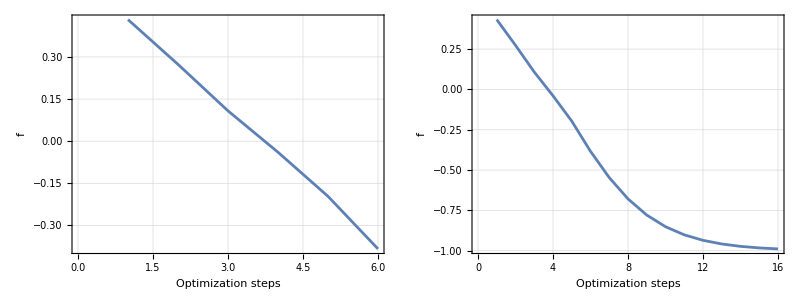

```mathematica
Grid[{
ListLinePlot[{cost@@@#},
FrameLabel->{"Optimization steps","f"},
Frame->True,GridLines->Automatic,ImageSize->Small]&/@qp}
]
```

#### Results Overview

Use the cost function from previous section and compare results using GradientDescent and QuantumNaturalGradient functions with η=0.05:

```mathematica
quantump=QuantumNaturalGradientDescent[cost,metric,"InitialPoint"->{π/12,π/12},"LearningRate"->0.05];
```

```mathematica
vanillap=GradientDescent[cost,{π/12,π/12},"LearningRate"->0.05];
```

In the following plot, regular gradient descent passes directly through the singularity, eventually finding a minimum, while Quantum Natural Gradient Descent appears to avoid the singularity and finds a different minimum value:

```mathematica
ContourPlot[cost[θ1,θ2],{θ1,-0.8,1},{θ2,-0.5,1.6},ContourStyle->None,ImageSize->Large,]
```

-Graphics-

This phenomenon is more clearly illustrated by looking at the StreamPlots generated for the gradient and the preconditioned gradient. On the left, the standard gradient allows us to pass through θ_1=0, while on the right, the corrected gradient prevents this from happening.:

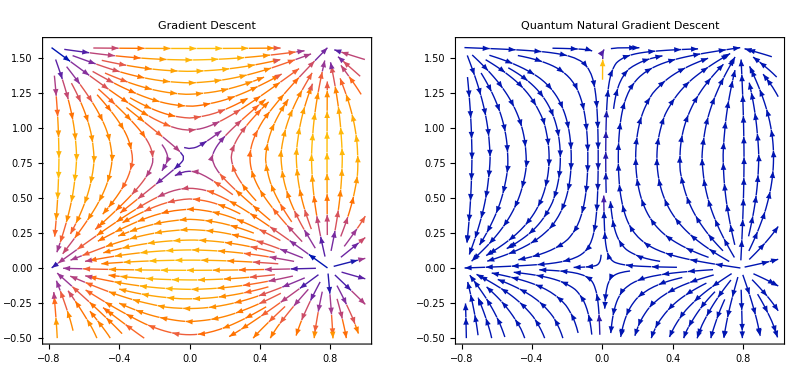

```mathematica
GraphicsRow[{StreamPlot[Evaluate[-Grad[cost,{θ1,θ2}]],],StreamPlot[Evaluate[Inverse[fubini].-Grad[cost,{θ1,θ2}]],]}]
```

#### Block-diagional approximation

We can calculate g using an approximation of the Fubini-Study metric tensor for a variational quantum circuit, named the block-diagonal approach:

g_ij^(l)=ψ_(l-1)K_i K_j ψ_(l-1)-ψ_(l-1)K_i ψ_(l-1)ψ_(l-1)K_j ψ_(l-1)

The circuit is given by:

U(θ)ψ_0=V_L(θ_L)W_L...V_l(θ_l)W_l...V_0(θ_0)W_0 ψ_0

where W are layers of non-parametrized gates and K_i^(l) are the generators of the parametrized gates V of the form ⅇ^((ⅈθ^(l))_i(K^(l))_i).

The quantum state before the application of layer l is:

ψ_(l-1)=V_(l-1)(θ_(l-1))W_(l-1)...V_0(θ_0)W_0 ψ_0

Let’s build a  circuit for the following example:

```mathematica
ℛ={"RY"[π/4]->1,"RY"[π/3]->2,"RY"[π/7]->3};
V1={"RZ"[θ1]->1,"RZ"[θ2]->2};
V2={"RY"[θ3]->2,"RX"[θ4]->3};
W={QuantumOperator["CNOT",{1,2}],QuantumOperator["CNOT",{2,3}]};
```

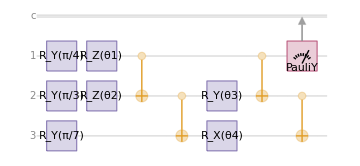

```mathematica
VQC=QuantumCircuitOperator[Join[ℛ,V1,W,V2,W],"Parameters"->{θ1,θ2,θ3,θ4},"Label"->None];
VQCState=VQC[];
VQC2=QuantumMeasurementOperator["PauliY"->{1,-1}][VQC];
VQC2["Diagram"]
```

##### Exact Fubini-Study metric tensor

First, we will implement the exact metric tensor based on our current formulation:

```mathematica
metric=FubiniStudyMetricTensor[VQCState]
```

QuantumOperator[QuantumState[SparseArray[<16>, {16}], QuantumBasis[<|Input -> QuditBasis[<|{QuditName[0, Dual -> True], 1} -> SparseArray[<1>, {2}], {QuditName[1, Dual -> True], 1} -> SparseArray[<1>, {2}], {QuditName[0, Dual -> True], 2} -> SparseArray[<1>, {2}], {QuditName[1, Dual -> True], 2} -> SparseArray[<1>, {2}]|>], <<3>>, ParameterSpec -> {<<4>>}|>]], {{<<2>>}, {<<2>>}}]

Test with the following initial parameters:

```mathematica
metric["Parameters"]
```

{θ1,θ2,θ3,θ4}

```mathematica
initParameters={0.432,-0.123,0.543,0.233};
```

```mathematica
Chop["Matrix"//metric@@initParameters,10^-10]//Re//MatrixForm
```

(0.125 | 0 | -0.00576267 | 0
0 | 0.1875 | 0.00407482 | 0
-0.00576267 | 0.00407482 | 0.249734 | -0.015247
0 | 0 | -0.015247 | 0.202936)

##### Block-diagional metric tensor approximation

sing the block-diagonal approximation, we will try to match the earlier result.

In this case we got 2 parametrized layers with two parameters each, then following the block-diagonal approach:

g=(g^(1) | 0
0 | g^(2))

Let’s define some helping functions:

```mathematica
variance[state_,qmo_]:=(#[[2]]*(1-#[[2]]))&@Values[qmo[state]["Probabilities"]]//N
```

```mathematica
covariance[state_,qmo1_,qmo2_]:=(#[[4]]-(#[[3]]+#[[4]])*(#[[2]]+#[[4]]))&@Values[qmo2[qmo1[state]]["Probabilities"]]//N
```

Calculate the first layer using the following formula:

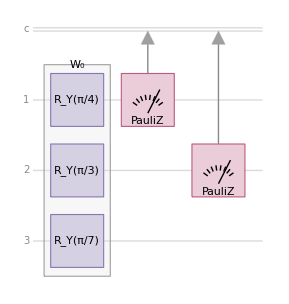

g^(1)=(⟨Z_1^2⟩-⟨Z_1⟩^2 | ⟨Z_1 Z_2⟩-⟨Z_1⟩⟨Z_2⟩
⟨Z_2 Z_1⟩-⟨Z_2⟩⟨Z_1⟩ | ⟨Z_2^2⟩-⟨Z_2⟩^2)

```mathematica
st1=QuantumCircuitOperator[ℛ][];
```

```mathematica
g1={
{variance[st1,QuantumMeasurementOperator["Z",{1}]],covariance[st1,QuantumMeasurementOperator["PauliZ",{2}],QuantumMeasurementOperator["PauliZ",{1}]]},
{covariance[st1,QuantumMeasurementOperator["PauliZ",{1}],QuantumMeasurementOperator["PauliZ",{2}]],variance[st1,QuantumMeasurementOperator["Z",{2}]]}
}
```

{{0.125,6.93889×10^-18},{6.93889×10^-18,0.1875}}

The second layer:

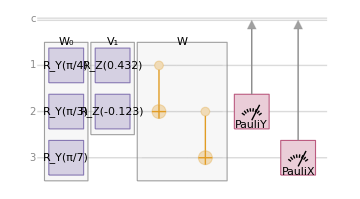

g^(2)=(⟨Y_2^2⟩-⟨Y_2⟩^2 | ⟨Y_2 X_3⟩-⟨Y_2⟩⟨X_3⟩
⟨X_3 Y_2⟩-⟨X_3⟩⟨Y_2⟩ | ⟨X_3^2⟩-⟨X_3⟩^2)

```mathematica
st2=QuantumCircuitOperator[{ℛ,V1/.Thread[Rule[{θ1,θ2},{0.432,-0.123}]],W}][];
```

```mathematica
g2={
{variance[st2,QuantumMeasurementOperator["Y",{2}]],covariance[st2,QuantumMeasurementOperator["Y",{2}],QuantumMeasurementOperator["X",{3}]]},
{covariance[st2,QuantumMeasurementOperator["X",{3}],QuantumMeasurementOperator["Y",{2}]],variance[st2,QuantumMeasurementOperator["X",{3}]]}
}
```

{{0.249734,-0.015247},{-0.015247,0.202936}}

Then the block diagonal matrix is the following:

```mathematica
BlockDiagonalMatrix[Chop[{g1,g2},10^-8]]//MatrixForm
```

(0.125 | 0. | 0. | 0.
0. | 0.1875 | 0. | 0.
0. | 0. | 0.249734 | -0.015247
0. | 0. | -0.015247 | 0.202936)

Cost function

Continuing with the usual workflow, consider the system Hamiltonian to be H=σ_Y⊗ 1 ⊗ 1

```mathematica
VQCCost[θ1_,θ2_,θ3_,θ4_]="Scalar"//SuperDagger[VQCState]@QuantumOperator["YII"]@VQCState;
```

```mathematica
VQCCost[θ1,θ2,θ3,θ4]//ComplexExpand//FullSimplify
```

1/4 (2 √2 Cos[θ3] Sin[π/7] Sin[θ1]+√6 Cos[θ1] Sin[θ2] Sin[θ3])

Proceed to calculate the correspondent gradient for each θ_i:

```mathematica
VQCCostGrad[θ1_,θ2_,θ3_,θ4_]=Grad[VQCCost[θ1,θ2,θ3,θ4]//ComplexExpand//Simplify,{θ1,θ2,θ3,θ4}]
```

{1/(2 √2)(2 Cos[θ1] Cos[θ3/2]^2 Sin[π/7]-2 Cos[θ1] Sin[π/7] Sin[θ3/2]^2-√3 Sin[θ1] Sin[θ2] Sin[θ3]),1/2 √(3/2) Cos[θ1] Cos[θ2] Sin[θ3],(√3 Cos[θ1] Cos[θ3] Sin[θ2]-4 Cos[θ3/2] Sin[π/7] Sin[θ1] Sin[θ3/2])/(2 √2),0}

Optimization

For this example we will test using η = 0.01 for 200 steps using θ_initial={0.432,-0.123,0.543,0.233}

```mathematica
VQCQuantumParameters=QuantumNaturalGradientDescent[VQCCost,metric,
"Gradient"->VQCCostGrad,
"LearningRate"->0.01,
"InitialPoint"->{0.432,-0.123,0.543,0.233},
"MaxIterations"->200
];
```

```mathematica
VQCStateVainillaParameters=GradientDescent[VQCCost,{0.432,-0.123,0.543,0.233},
"LearningRate"->0.01,
"MaxIterations"->200
];
```

The ground state is reached in less steps by the quantum gradient descent.

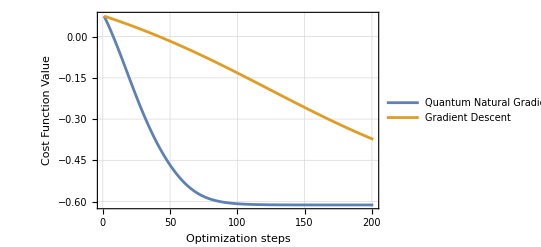

```mathematica
ListLinePlot[
{VQCCost@@@VQCQuantumParameters,VQCCost@@@VQCStateVainillaParameters},
PlotRange->All,
PlotLegends->{"Quantum Natural Gradient Descent","Gradient Descent"},
FrameLabel->{"Optimization steps","Cost Function Value"},Frame->True,GridLines->Automatic]
```

## Quantum Linear Solvers

### Harrow–Hassidim–Lloyd algorithm (HHL)

The main goal of HHL algorithm is too solve a linear system A.x=b by preparing a quantum state of the solution: HHL outputs x∝A^-1.b, enabling estimation of properties of x with (under sparsity, good conditioning, and oracle access) runtime polylogarithmic in the dimension.

#### Theory

The Harrow–Hassidim–Lloyd (HHL) algorithm is a quantum procedure designed to solve systems of linear equations of the form:

A x⃗=b⃗

where A is a Hermitian matrix and b is a known vector. The importance of HHL lies in its potential to provide exponential speedup over classical algorithms under certain conditions, and in the fact that it serves as a foundation for several advanced algorithms in areas such as machine learning, optimization, and quantum simulation.

The quantum circuit implementing HHL (as shown in the schematic) is organized into five main sections:

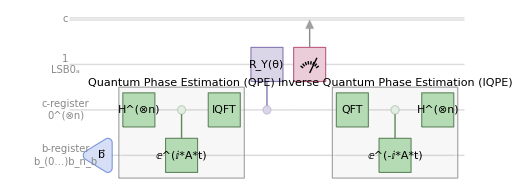

```mathematica
pe=QuantumCircuitOperator[{
QuantumOperator["RandomUnitary","Label"->"H^(⊗n)"]->{2},
"C"[QuantumOperator["RandomUnitary","Label"->"ⅇ^(ⅈ*A*t)"]]->{2,3},
QuantumOperator["RandomUnitary","Label"->"IQFT"]->{2}
}, "Label"->"Quantum Phase Estimation (QPE)"];
ipe=QuantumCircuitOperator[{
QuantumOperator["RandomUnitary","Label"->"QFT"]->{2},
"C"[QuantumOperator["RandomUnitary","Label"->"ⅇ^(-ⅈ*A*t)"]]->{2,3},
QuantumOperator["RandomUnitary","Label"->"H^(⊗n)"]->{2}
}, "Label"->"Inverse Quantum Phase Estimation (IQPE)"];
im=QuantumCircuitOperator[{
"I"->Range[2],
QuantumState["RandomPure","Label"->"b⃗"]->{3},
pe,
"C"[QuantumOperator["RY"[θ]]]->{2,1},
{1},
"I"->{2,3},
ipe
}];
im["Diagram",ImageSize->Full,
"WireLabels"->{"1\nLSB0_a","c-register\n0^(⊗n)","b-register\nb_(0…)b_n_b"},
"GateBackgroundStyle"->{
	"State\n Preparation"->LightOrange,
	"H^(⊗n)"|"ⅇ^(ⅈ*A*t)"|"ⅇ^(-ⅈ*A*t)"|"IQFT"|"QFT"->Lighter@Hue[0.33,0.3,0.79]
	},
"GateBoundaryStyle"->{
	"State\n Preparation"->Orange,
	"H^(⊗n)"|"ⅇ^(ⅈ*A*t)"|"ⅇ^(-ⅈ*A*t)"|"IQFT"|"QFT"->Darker@Hue[0.33,0.3,0.79]
	}
]
```

State b⃗ preparation

The vector b⃗ is encoded into the amplitudes of a register of qubits (the b-register). This step translates the classical problem into a quantum state b.

Quantum Phase Estimation (QPE)

QPE is applied to decompose b in the eigenbasis of A. The eigenvalues λ_i of A are encoded into an auxiliary register of clock qubits (the c-register).

Controlled Rotation & Measurement of the ancilla qubit

An auxiliary qubit (the ancilla, Least Significant Bit - LSB) is rotated in a way that depends on the eigenvalues stored in the c-register. This step effectively implements the action of A^-1, since the amplitudes are scaled by 1/λ_i . Measure the ancilla and keep only outcomes 1_a.

Inverse Quantum Phase Estimation (IQPE)

The inverse QPE is applied to disentangle the c-register from the b-register, ensuring that the solution is properly isolated in the latter.

Measurement

After post-selecting the ancilla in the desired state, the quantum system in the b-register encodes the solution x=A^-1 b. While the algorithm does not yield the classical solution vector directly, it enables the estimation of global properties of the solution, such as norms, probability distributions, or expectation values of observables.

This way, HHL combines three central tools of quantum computing:

superposition

phase estimation

controlled operations

And turn it into a coherent algorithm that addresses a fundamental problem in science and engineering.

#### Encoding Scheme

We implement the HHL algorithm for the following system of linear equations:

Piecewise[{{x_1-1/3 x_2=0
-1/3 x_1+x_2=1, or equivalently (1 | -1/3
-1/3 | 1)(x_1
x_2)=(0
1)}}]

with

A=(1 | -1/3
-1/3 | 1) , b⃗=(0
1)

```mathematica
A={{1,-1/3},{-1/3,1}};
b={0,1};
```

The eigenvalues and eigenvectors of 𝐴 are:

```mathematica
Eigensystem[A]
```

{{4/3,2/3},{{-1,1},{1,1}}}

```mathematica
{λ1,λ0}=Eigenvalues[A]
```

{4/3,2/3}

To encode the eigenvalues in the clock register, we use basis encoding. Two qubits are sufficient to represent the eigenvalues while maintaining their ratio:

(λ̃)_0=1 encoded as 01, (λ̃)_1=2 encoded as 10

This preserves the ratio λ_0/λ_1=0:

```mathematica
n=Divide@@Eigenvalues[A]
```

2

This gives a perfect encoding with 𝑛=2 (i.e., 𝑁=2^n=4). The evolution time 𝑡 is chosen to satisfy:

(λ̃)_j=Nλ_j t/2π

```mathematica
Solve[1==(2^n*λ0*t)/(2π),{t}]
```

{{t→(3 π)/4}}

```mathematica
Solve[2==(2^n*λ1*t)/(2π),{t}]
```

{{t→(3 π)/4}}

Since b⃗ is a 2-dimensional vector, it can be encoded using one qubit, so n_b=1

The exact solution to the linear system is:

```mathematica
LinearSolve[A,b]
```

{3/8,9/8}

We can verify the ratio of the squared amplitudes |x_1|^2∶|x_2|^2=1∶9:

```mathematica
Divide@@(Reverse[%]^2)
```

9

#### Implementation of the controlled-rotation of ancilla qubit

The next step is to rotate the ancilla qubit 0_a using a controlled RY(θ) rotation, where the control comes from the encoded eigenvalues in the clock (c-) register.

The rotation maps:

0_a -> √(1-C/OverTilde[λ_j]^2)0_a+C/((λ̃)_j)1_a

with θ=2ArcSin[C/((λ̃)_j)] and C is a constant chosen to maximize the probability of measuring 1_a.

The sum of the squares of the coefficients of 0 and 1 is 1, as required for a normalized quantum state. This also implies that C<=(λ̃)_j for all eigenvalues. Since the minimal (λ̃)_j=1 in our example, we set C=1 to maximize the probability of measuring 1_a during the ancilla measurement.

To implement this rotation in the algorithm,we solve for θ in terms of the encoded eigenvalues:

```mathematica
rotation=QuantumOperator["RY"[θ]]@QuantumState["0"];
rotation["Formula"]
```

Cos[θ/2]0+Sin[θ/2]1

```mathematica
θsolutions=Solve[rotation["AmplitudeList"]=={√(1-1/(λ̃)^2),1/(λ̃)},{θ}]/.ArcCos[x_]:>ArcSin[√(1-x^2)]//FullSimplify//Quiet
```

{{θ→-2 ArcSin[√(1/(λ̃)^2)]},{θ→2 ArcSin[√(1/(λ̃)^2)]}}

Assigning the actual eigenvalues:

```mathematica
θvalues=θ/.Last[θsolutions]/.λ̃->{1,2}
```

{π,π/3}

When the ancilla qubit is measured, it collapses to either 0_a or 1_a:

If it collapses to 0_a, the computation is discarded and repeated.

If it collapses to 1_a, the resulting state is proportional to the solution x, but the b-register is still entangled with the clock register.

To obtain the correct amplitudes in the computational basis, we need to uncompute the clock register. This disentangles the b-register from the clock qubits.

#### Quantum Phase Estimation

Quantum Phase Estimation (QPE) is a core eigenvalue estimation algorithm used in HHL. It consists of three main steps:

Creating a superposition of the clock qubits using Hadamard gates.

Applying controlled-unitary operations CU, where U=ⅇ^(ⅈ*A*t).

Performing the inverse quantum Fourier transform (IQFT) on the clock register.

The goal of QPE is to estimate the phase of the eigenvalues of the unitary operator U. In HHL, the controlled-𝑈 operation is applied to the b-register, conditioned on the clock qubits:

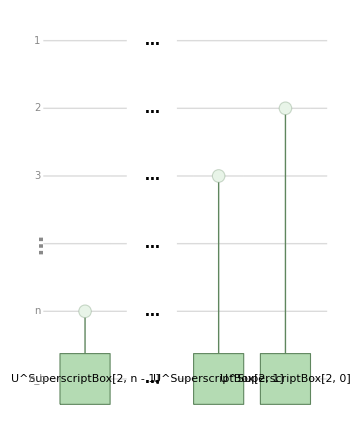

```mathematica
img=QuantumCircuitOperator[{
"I"->Range[4],
"C"[QuantumOperator["RandomUnitary","Label"->"U^SuperscriptBox[2, n - 1]"]]->{5,6},
Sequence@@Map[QuantumOperator["X","Label"->Style["…",15,Bold]]->{#}&,Range[6]],
"C"[QuantumOperator["RandomUnitary","Label"->"U^SuperscriptBox[2, 1]"]]->{3,6},
"C"[QuantumOperator["RandomUnitary","Label"->"U^SuperscriptBox[2, 0]"]]->{2,6}

}];
img["Diagram","WireLabels"->{1,2,3,Style[Rotate["…",π/2],20,Bold],"n","n_b"},"GateBackgroundStyle"->{
	Style["…",15,Bold]->None,
	"U^SuperscriptBox[2, n - 1]"|"U^SuperscriptBox[2, 1]"|"U^SuperscriptBox[2, 0]"->Lighter@Hue[0.33,0.3,0.79]
	},
"GateBoundaryStyle"->{
	Style["…",15,Bold]->None,
"U^SuperscriptBox[2, n - 1]"|"U^SuperscriptBox[2, 1]"|"U^SuperscriptBox[2, 0]"->Darker@Hue[0.33,0.3,0.79]
	}
]
```

For our 2×2 example (𝑛=2), the required operations are:

U^(2^1)=U^2 and U^(2^0)=U

To construct these gates, we first derive the unitary  U=ⅇ^(ⅈ*A*t) by performing a similarity transformation on A, exponentiating, and transforming back to the original basis:

```mathematica
U=QuantumOperator[MatrixExp[((3Pi)/4) I A]]
```

QuantumOperator[…]

Inspecting the resulting matrix:

```mathematica
U["Matrix"]//MatrixForm
```

(-1/2+ⅈ/2 | 1/2+ⅈ/2
1/2+ⅈ/2 | -1/2+ⅈ/2)

and for U^2:

```mathematica
(U^2)["Matrix"]//MatrixForm
```

(0 | -1
-1 | 0)

This gate encodes the Hamiltonian defined by the matrix A. Since U is unitary, its eigenvalues are roots of unity meaning that the phase of each eigenvalue of U is proportional to the corresponding eigenvalue of A. Consequently, when QPE is applied in HHL, the eigenvalues of A are encoded in the clock (c-) register through basis encoding, rather than storing their exact numerical values.

We can also implement QPE directly using the built-in “PhaseEstimation” gate in Wolfram Language:

```mathematica
QPE=QuantumCircuitOperator["PhaseEstimation"[U,n]][[2;;-3]]
```

QuantumCircuitOperator[…]

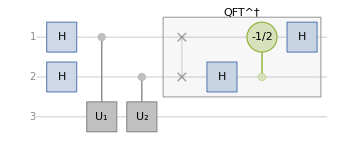

```mathematica
QPE["Diagram"]
```

Note that in our framework, the controlled-unitary gates are constructed in the opposite direction compared to this paper conventions. (remove this, focus only on our convention, we do not want to say we reproduce exactly a specific result etc)

#### Circuit Implementation

We can now implement the full HHL algorithm as a quantum circuit in Wolfram Language. The circuit includes the following steps:

Initialize the b-register with the state b.

Apply Quantum Phase Estimation (QPE) on the clock qubits.

Perform controlled RY(θ) rotations on the ancilla qubit, using the angles computed from the encoded eigenvalues.

Uncompute the QPE to disentangle the b-register from the clock qubits.

Measure the b-register to extract the solution.

```mathematica
HHL=QuantumCircuitOperator[{
QuantumState[b]->{4},"Barrier",
QPE->{2,3,4},"Barrier",
"C"["RY"[θvalues[[1]]]]->{2,1},
"C"["RY"[θvalues[[2]]]]->{3,1},
"Barrier",{1},"Barrier",
SuperDagger[QPE]->{2,3,4},
{4}
}]
```

QuantumCircuitOperator[…]

We can visualize the circuit:

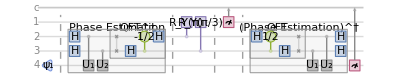

```mathematica
HHL["Diagram",Expand->2,ImageSize->Full]
```

Perform the measurement:

```mathematica
measurement=HHL[]
```

QuantumMeasurement[…]

After executing the circuit and measuring the qubits, the probabilities of each computational basis state are:

```mathematica
result=Normal[measurement["Probabilities"]]//FullSimplify
```

{00→3/16,01→3/16,10→1/16,11→9/16}

The solution correspond to the measured probabilities of the b-register. Selecting the relevant outcomes:

```mathematica
x=Values[result][[{3,4}]]
```

{1/16,9/16}

Finally, we verify that the ratio of the measured amplitudes matches the ratio of squared solutions obtained classically:

```mathematica
Divide@@x==Divide@@(LinearSolve[A,b]^2)
```

True

This confirms that the HHL implementation successfully encodes the solution to the linear system in the amplitudes of the b-register, consistent with the classical solution.

### Variational Quantum Linear Solver (VQLS)

The Variational Quantum Linear Solver (VQLS) is a a hybrid quantum-classical technique designed to address Quantum Linear Systems Problem (QLSP). It aims to find linear system solutions using quantum computing techniques. The corresponding quantum algorithm can be summarized as follows:

Given:

A quantum state b such that b=U0

2^n x 2^n dimensional matrix A such that A=(∑_0)^(L-1)c_l A_l where c_l ϵ  ℂ and A_lare unitary gates

One wants to prepare:

A quantum state x  such that ψ=Ax  and ψ/(√ψψ)->b

##### VQLS Approach

We will get an approximate x  state using a variational quantum circuit V(ω), in other words:

x,=V(ω)0

Then, we look to optimize the parameters ω={ω_0,ω_1,... } in order to minimize the cost function. We can propose the following cost function:

C_G=1/ψψ x H_G x
=1/ψψ A^†(𝟙-bb)A=1/ψψ Tr[ψψ(𝟙-bb)]
=1- |bψ|,^2

where ψ=ψ/(√ψψ).

You can write C_G explicitly as:

C_G=1- (∑_(l,l') c_l c_l'^*0 V^†A_l'^†U00 U^†A_l V0)/(∑_(l,l') c_l c_l'^*0 V^†A_l'^†A_l V0)

As  Bravo-Prieto explains, a barren plateau might arise from using this global cost function. In other words, it indicates that the gradients of the cost function with respect to the parameters of the quantum circuit vanish exponentially as the number of qubits n increases. When gradients become extremely small, it becomes hard for optimization algorithms to make meaningful progress in adjusting the parameters of the quantum circuit to minimize the cost function.

Instead, we can work with a “local” version of it and apply the Hadamard test to estimate the expectation values. According to Bravo-Prieto, the local version is calculaton by changing H_G->H_L=[A^†U(𝟙-1/n∑ 0_j 0_j⊗𝟙_(j^-))U^†A],, where j is the qubit index and 𝟙_(j^-) the indentity on all qubits except j.

Finally we can express the local cost function explicitly as:

C_L=1/2-1/(2n)∑_(j=0)^(n-1) (∑_(l,l') c_l c_l'^*0 V^†A_l'^†U,,, Z_j U^†A_l V0)/(∑_(l,l') c_l c_l'^*0 V^†A_l'^†A_l V0)
=1/2-1/(2n)∑_(j=0)^(n-1) (∑_(l, l') c_l c_l'^*μ_(l , l', j))/(∑_(l,l') c_l c_l'^*μ_(l , l', -1))

where μ_(l , l',j)= 0 V^†A_l'^†U Z_J U^†A_l V0 , Z_-1->𝟙 and  C_G->0 <->C_L->0.

References used for this section:

Bravo-Prieto, C., LaRose, R., Cerezo, M., Subasi, Y., Cincio, L., & Coles, P. J. (2019). Variational Quantum Linear Solver. arXiv. https://doi.org/10.48550/ARXIV.1909.05820

Mari, A. Variational Quantum Linear Solver. PennyLane Demos. https://pennylane.ai/qml/demos/tutorial_vqls/

#### QLSP introductory example

In this implementation we will consider the first qubit as our auxiliary qubit, since in the Wolfram QuantumFramework negative qubits and qubit 0 are used only for classical bits.

For this example we will consider a 2 qubits system plus an auxiliary qubit.

A=X_2 H_3

b=U0=H_2 H_3 0

where the operator’s index indicate the qubit it is applied on.

Given the ansatz:

x=V(ω)0=[R_y(ω_2)⊗R_y(ω_3)]H_2 H_3 0

We will proceed to build the circuit to minimize C_L.

##### Circuit Implementation

First we define the gates associated with the example:

The unitary matrix such that b=U_b 0 :

```mathematica
Ub=QuantumCircuitOperator[{"H"->{2},"H"->{3}},"Label"->"U_b"];
```

Because our goal is to conduct a Hadamard test, it’s necessary for the unitary operation A to be controlled  by the state of an auxiliary qubit:

```mathematica
ControlledAGate=QuantumCircuitOperator[{"CNOT"->{1,2},"CH"->{1,3}},"Label"->"A_2"];
```

Next, we implement the variational quantum circuit that generates a guess for x:

x=V(ω)0=[R_x(ω_1)⊗R_x(ω_2)]H_2 H_3 0

The first layer prepare an equal superposition of states and the second layer is the ansatz proposed before:

```mathematica
VariationalBlock=QuantumCircuitOperator[
{"H"->{1,2},
"RY"[ω1]->{1},"RY"[ω2]->{2}},
"Label"->"V(ω)","Parameters"->{ω1,ω2}];
```

In order to obtain μ_(l , l', j) we will implement a circuit that will deploy a Hadamard test:

1. We first apply a Hadamard in the auxiliar qubit to prepare a state in superposition.
2. We apply a Phase Shift to estimate the imaginary or real part of the μ: Re[μ] when θ → 0 and Im[μ] when θ → -π/2.

3. Apply the Variational Circuit to generare a guess on x.
4. Apply the Controlled Gate corresponding to the A_lcomponent.
5. Apply the adjoint U_b, but in this case is the same as U_b.
6. Implement a controlled Z operator from the auxiliar qubit to the system qubit j. For the normalization calculation, we will use j = -1 to apply the identity.
7. From this step, we will “undo” our operations, first by applying U_b.
8. Apply the A_l Controlled gate‘s adjoint, which is the same as A_l.
9. Last Hadamard gate for the Hadamard test
At the end we apply a QuantumMeasureOperator to measure the expectation values.

```mathematica
Clear[LocalHadamardCircuit];
LocalHadamardCircuit[j_]:=QuantumCircuitOperator[{
"Hadamard"->{1},
"P"[θ],
VariationalBlock->{2,3},
ControlledAGate,
Ub,
If[!MatchQ[j,-1],"CZ"->{1,j},Nothing],
Ub,
ControlledAGate,
"Hadamard"->{1},
QuantumMeasurementOperator["Z"->{-1,1},{1}]
},
"Parameters"->{ω1,ω2,θ}
]
```

You can test the multiple variations of the circuit for each controlled gate:

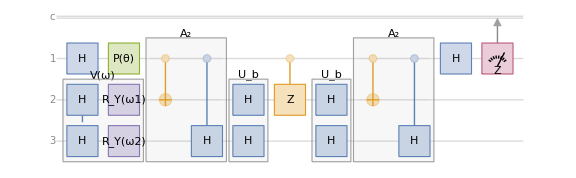

```mathematica
LocalHadamardCircuit[2]["Diagram",ImageSize->Large]
```

##### Optimized Circuit Implementation

As you might notice, the past implementation might be slow if we want to obtain the expected value for each combination. Moreover, the local cost function that we will implement later to optimize will need to calculate the mean value multiple times.

Instead we could try to use the useful KroneckerProduct to build the same circuit with all the variations.

We can re-implement CZ gate, since it depends in which qubit it will be applied on:

```mathematica
ControlledGateZ=QuantumOperator[
QuantumOperator["CZ"->{1,2}]*KroneckerDelta[j,2]+QuantumOperator["CZ"->{1,3}]*KroneckerDelta[j,3]+QuantumOperator["I"]*KroneckerDelta[j,-1],
"Label"->"Controlled Z_j Gate"
];
```

As you might notice, we just apply a KroneckerDelta to get rid of the qubits we won’t be using for each case, this is possible since we already know how many qubits we are working on.

As the previous subsection, we implement the Hadamard test:

```mathematica
ClearAll[LocalHadamardCircuit];
LocalHadamardCircuit=QuantumCircuitOperator[{
"Hadamard"->{1},
"P"[θ],
VariationalBlock->{2,3},
ControlledAGate,
Ub,
ControlledGateZ,
Ub,
ControlledAGate,
"Hadamard"->{1}
},"Parameters"->{ω1,ω2,j,θ}];
```

Check out the newly implemented circuit diagram:

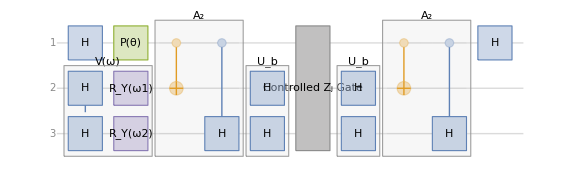

```mathematica
LocalHadamardCircuit["Diagram",ImageSize->Large]
```

##### Local Cost Function

You might noticed that we didn’t include the QuantumMeasurementOperator. In order to calculate even faster the mean values, we will calculate ϕHϕ where H=σ_z ⊗𝟙 ⊗𝟙:

```mathematica
ket=Normal[LocalHadamardCircuit[]["StateVector"]];
```

```mathematica
bra=ConjugateTranspose[ket];
```

Finally we use the ket and bra obtained to calculate the expected value:

```mathematica
H=Normal[QuantumOperator[{"Z"->{1},"I"->{2,3}}]["Matrix"]];
```

```mathematica
LocalMean=bra.H.ket;
```

We just obtained the Symbolic Mean value of our circuit, in order to replace the variables quickly we define the following function:

```mathematica
ClearAll[LocalMeanValues];
LocalMeanValues[ω1_,ω2_,j_,θ_]=LocalMean;
```

Now we will implement all the functions needed for the cost function defined in the Theory section:

Define  μ_(l,v,j) , note that you get Re[μ] when θ → 0 and Im[μ] when θ → -π/2:

```mathematica
ClearAll[μ]
μ[ω1_,ω2_,j_]:=Module[{μRe,μIm},

μRe=LocalMeanValues[ω1,ω2,j,0];
μIm=LocalMeanValues[ω1,ω2,j,-π/2.];


N[μRe + j  μIm]
]
```

Next, implement the normalization term:

```mathematica
ClearAll[PsiNorm];
PsiNorm[ω1_,ω2_]:=Abs[μ[ω1,ω2,-1]];
```

Following the C_L equation, we define the cost function:

```mathematica
ClearAll[LocalCost];
LocalCost[ω1_,ω2_]:=0.5-(0.5/(3PsiNorm[ω1,ω2]))Abs[μ[ω1,ω2,2]+μ[ω1,ω2,3]]
```

##### Symbolic Cost Function Optimization

Let’s calculate the symbolic equation for the cost function. It is not that huge of an expression, but surely not visually pleasant to show here:

```mathematica
ClearAll[LocalCostFunction];
LocalCostFunction[ω1_,ω2_]=Simplify[LocalCost[ω1,ω2],{ω1,ω2}∈ Reals];//AbsoluteTiming
```

{8.71263,Null}

Since we have the symbolic function, we can use NMinize:

```mathematica
GradientParameters=NMinimize[LocalCostFunction[ω1,ω2],{ω1,ω2}]
```

{0.166667,{ω1→-9.87416×10^-11,ω2→-1.5708}}

##### Numerical Cost Function Optimization

We can use our previously defined LocalCost for numerical calculations using a numerical gradient descent:

```mathematica
ω= 0.001 *RandomVariate[NormalDistribution[],2];
```

```mathematica
NGradientParameters=GradientDescent[LocalCost,ω,"LearningRate"->0.8,"MaxIterations"->15];//AbsoluteTiming
```

{20.2959,Null}

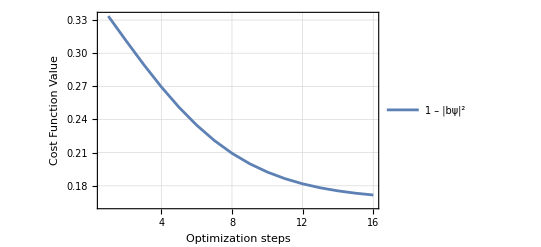

```mathematica
ListPlot[LocalCostFunction@@@NGradientParameters,Joined->True,GridLines->Automatic,PlotRange->All,Frame->True,FrameLabel->{"Optimization steps","Cost Function Value"},PlotLegends->{"1 – |bψ|^2"}]
```

##### Classical Linear System Solving

We can build the A matrix and statebof the present problem:

A=X_2 H_3

b=U0=H_2 H_3 0

Solve the system by operating over the correspondant matrices:

```mathematica
A=KroneckerProduct[PauliMatrix[1],HadamardMatrix[2]];
b=ConstantArray[1/Sqrt[8],4];
{"A"->MatrixForm[A],"b"->MatrixForm[b]}
```

{A→(0 | 0 | 1/(√2) | 1/(√2)
0 | 0 | 1/(√2) | -1/(√2)
1/(√2) | 1/(√2) | 0 | 0
1/(√2) | -1/(√2) | 0 | 0),b→(1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2))}

Finally, compute the probabilities:

```mathematica
LinearSystemResult=Normalize[LinearSolve[A,b]]^2;
Thread[Delete[0]@#&/@Tuples[{"0","1"},2]->LinearSystemResult]
```

{0,0→1/2,0,1→0,1,0→1/2,1,1→0}

##### Symbolic & Numeric Quantum Circuit Result

Test the Variational circuit with the optimized parameters results:

```mathematica
VariationalMeasurement=QuantumCircuitOperator[{VariationalBlock,{1},{2}}][];
```

The symbolic optimization resultant probabilities:

```mathematica
SymbolicResult=VariationalMeasurement[Association[GradientParameters[[2]]]]["Probabilities"]
```

<|00→0.5,01→1.61337×10^-17,10→0.5,11→1.61337×10^-17|>

The numerical optimization resultant probabilities:

```mathematica
NumericalResult=VariationalMeasurement[AssociationThread[{ω1,ω2},Last@NGradientParameters]]["Probabilities"]
```

<|00→0.492425,01→0.007484,10→0.492604,11→0.00748671|>

We can calculate how different one distribution is from another using a Kolmogorov Smirnov Test:

```mathematica
KolmogorovSmirnovTest[Values@SymbolicResult,LinearSystemResult]
```

0.657143

```mathematica
KolmogorovSmirnovTest[Values@NumericalResult,LinearSystemResult]
```

0.771429

In this case, the number is considered big enough to indicate that the results are from the reference distribution.

Let’s plot the probabilities for a visual comparison:

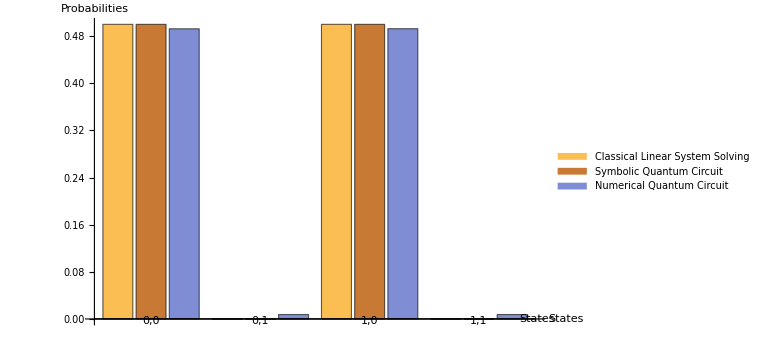

```mathematica
BarChart[Transpose[{LinearSystemResult,Values@SymbolicResult,Values@NumericalResult}],ChartLayout->"Grouped",ChartLabels->{Delete[0]@#&/@Tuples[{"0","1"},2],None},ChartLegends->{"Classical Linear System Solving","Symbolic Quantum Circuit","Numerical Quantum Circuit"},ImageSize->Large,AxesLabel->{"States","Probabilities"}]
```

#### QLSP implemented in Rigetti Quantum Computer

This QLSP was already tested by Bravo-Prieto using Rigetti’s quantum chip 16Q Aspen-4.

For this example we will consider a 3 qubits system plus an auxiliar qubit.

A=c_2 A_2+c_3 A_3+c_4 A_4=𝟙+0.2 X_2 Z_3+0.2 X_2

b=U0=H_2 H_3 H_4 0

where the operator’s index indicate the qubit it is applied on.

Given the ansatz:

x=V(ω)0=[R_y(ω_2)⊗R_y(ω_3)⊗R_y(ω_4)]H_2 H_3 H_4 0

We will proceed to build the circuit to minimize C_L.

##### Circuit Implementation

As the previous QLSP,  we define the gates associated with the example:

The unitary matrix such that b=U_b 0 :

```mathematica
Ub=QuantumCircuitOperator[{"H"->{2,3,4}},"Label"->"U_b"];
```

In this case we have multiple controlled A_l  gates to perform the Hardamard–test and controlled Z_j gates as the previous example, so we will directly implement an optimized version of the circuit using KroneckerProduct:

```mathematica
ControlledGateA=QuantumOperator[QuantumOperator["I"]*KroneckerDelta[l,2]+QuantumOperator[{"CNOT"->{1,2},"CZ"->{1,3}}]*KroneckerDelta[l,3]+QuantumOperator[{"CNOT"->{1,2}}]*KroneckerDelta[l,4],
"Parameters"->{l},
"Label"->"Controlled A_l Gate"];
```

```mathematica
ControlledGateZ=QuantumOperator[
QuantumOperator["CZ"->{1,2}]*KroneckerDelta[j,2]+QuantumOperator["CZ"->{1,3}]*KroneckerDelta[j,3]+QuantumOperator["CZ"->{1,4}]*KroneckerDelta[j,4]+QuantumOperator["I"]*KroneckerDelta[j,-1],
"Parameters"->{j},
"Label"->"Controlled Z_j Gate"
];
```

Next, we implement the variational quantum circuit that generates a guess for x:

x=V(ω)0=[R_y(ω_1)⊗R_y(ω_2)⊗R_y(ω_3)]H_2 H_3 H_4 0

```mathematica
VariationalBlock=QuantumCircuitOperator[{
"Hadamard"->{1,2,3},
"RY"[ω1]->{1},"RY"[ω2]->{2},"RY"[ω3]->{3}
},
"Label"->"V(ω)",
"Parameters"->{ω1,ω2,ω3}];
```

In order to obtain μ_(l , l', j) we will implement a circuit that will deploy a Hadamard test:

```mathematica
ClearAll[LocalHadamardCircuit];
LocalHadamardCircuit=QuantumCircuitOperator[{
"Hadamard"->{1},
"P"[θ],
VariationalBlock->{2,3,4},
ControlledGateA,
Ub,
ControlledGateZ,
Ub,
ControlledGateA[<|l->lp|>],
"Hadamard"->{1}
},"Parameters"->{ω1,ω2,ω3,l,lp,j,θ}];
```

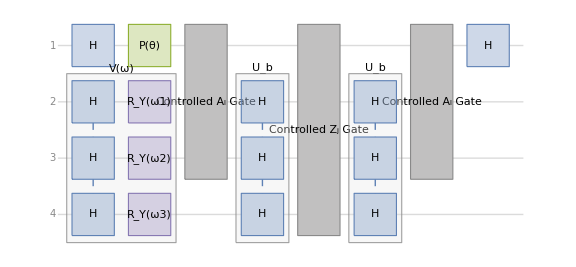

```mathematica
LocalHadamardCircuit["Diagram",ImageSize->Large]
```

##### Local Cost Function

Now let’s calculate the symbolic mean value:

```mathematica
ket=Normal[LocalHadamardCircuit[]["StateVector"]];
```

```mathematica
bra=ConjugateTranspose[ket];
```

Finally we use the ket and bra obtained to calculate the expected value:

```mathematica
H=Normal[QuantumOperator[{"Z"->{1},"I"->{2,3,4}}]["Matrix"]];
```

```mathematica
LocalMean=bra.H.ket;
```

Now we redefine the functions, since we are dealing with more ω_i variables from our Variational Circuit:

```mathematica
ClearAll[LocalMeanValues];
LocalMeanValues[ω1_,ω2_,ω3_,l_,lp_,j_,θ_]=LocalMean;
```

Now we will implement all the functions needed for the cost function defined in the Theory section:

Define  μ_(l,v,j) :

```mathematica
ClearAll[μ]
μ[ω1_,ω2_,ω3_,l_,lp_,j_]:=Module[{μRe,μIm},

μRe=LocalMeanValues[ω1,ω2,ω3,l,lp,j,0];
μIm=LocalMeanValues[ω1,ω2,ω3,l,lp,j,-π/2.];


N[μRe + j  μIm]
]
```

We prepend a 0 value in the constants from the A problem matrixso it later matches with the system qubits index:

```mathematica
c={0.,1.0,0.2,0.2};
```

Now we will implement the normalization term. In this case l and lp values correspond to our system qubits:

```mathematica
ClearAll[PsiNorm];
PsiNorm[ω1_,ω2_,ω3_]:=Abs[Sum[c[[l]]*Conjugate[c[[lp]]]*μ[ω1,ω2,ω3,l,lp,-1],{l,{2,3,4}},{lp,{2,3,4}}]];
```

Following the C_L equation, we define the cost function:

```mathematica
ClearAll[LocalCost];
LocalCost[ω1_,ω2_,ω3_]:=0.5-(0.5/(3PsiNorm[ω1,ω2,ω3]))Abs[Sum[c[[l]]*Conjugate[c[[lp]]]*μ[ω1,ω2,ω3,l,lp,j],
{l,{2,3,4}},{lp,{2,3,4}},{j,{2,3,4}}]]
```

##### Symbolic Cost Function Optimization

Let’s calculate the symbolic equation for the cost function. It is not that huge of an expression, but surely not visually pleasant to show here:

```mathematica
ClearAll[LocalCostFunction];
LocalCostFunction[ω1_,ω2_,ω3_]=Simplify[LocalCost[ω1,ω2,ω3],{ω1,ω2,ω3}∈ Reals];//AbsoluteTiming
```

{22.0404,Null}

Since we have the symbolic function, we can use NMinimize:

```mathematica
GradientParameters=NMinimize[LocalCostFunction[ω1,ω2,ω3],{ω1,ω2,ω3}]
```

{2.22045×10^-16,{ω1→-6.85484×10^-9,ω2→0.330297,ω3→1.04434×10^-8}}

##### Numerical Cost Function Optimization

We can use our previously defined LocalCost for numerical calculations using a numerical gradient descent:

```mathematica
ω= 0.001 *RandomVariate[NormalDistribution[],3];
```

```mathematica
NGradientParameters=GradientDescent[LocalCost,ω,"LearningRate"->0.8,"MaxIterations"->15];//AbsoluteTiming
```

{446.201,Null}

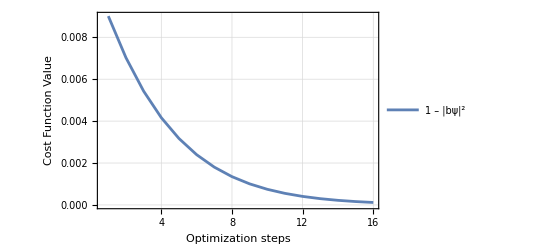

```mathematica
ListPlot[LocalCostFunction@@@NGradientParameters,Joined->True,GridLines->Automatic,PlotRange->All,Frame->True,FrameLabel->{"Optimization steps","Cost Function Value"},PlotLegends->{"1 – |bψ|^2"}]
```

##### Classical Linear System Solving

We can build the A matrix and stateb of the present problem:

A=c_2 A_2+c_3 A_3+c_4 A_4=𝟙+0.2 X_2 Z_3+0.2 X_2

b=U0=H_2 H_3 H_4 0

Solve the system by operating over the corresponding matrices:

```mathematica
A=c[[2]]*IdentityMatrix[8]+
c[[3]]*KroneckerProduct[PauliMatrix[1],PauliMatrix[3],IdentityMatrix[2]]+c[[4]]*KroneckerProduct[PauliMatrix[1],IdentityMatrix[2],IdentityMatrix[2]];
b=ConstantArray[1/Sqrt[8],8];
{"A"->MatrixForm[A],"b"->MatrixForm[b]}
```

{A→(1. | 0. | 0. | 0. | 0.4 | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.4 | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0.4 | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0.4 | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.),b→(1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2)
1/(2 √2))}

Finally, compute the probabilities:

```mathematica
LinearSystemResult=Normalize[LinearSolve[A,b]]^2;
Thread[Delete[0]@#&/@Tuples[{"0","1"},3]->LinearSystemResult]
```

{0,0,0→0.0844595,0,0,1→0.0844595,0,1,0→0.165541,0,1,1→0.165541,1,0,0→0.0844595,1,0,1→0.0844595,1,1,0→0.165541,1,1,1→0.165541}

##### Symbolic & Numeric Quantum Circuit Result

Test the Variational circuit with the optimized parameters results:

```mathematica
VariationalMeasurement=QuantumCircuitOperator[{VariationalBlock,{1,2,3}}][];
```

The symbolic optimization resultant probabilities:

```mathematica
SymbolicResult=VariationalMeasurement[Association[GradientParameters[[2]]]]["Probabilities"]
```

<|000→0.0844595,001→0.0844595,010→0.165541,011→0.165541,100→0.0844595,101→0.0844595,110→0.165541,111→0.165541|>

The numerical optimization resultant probabilities:

```mathematica
NumericalResult=VariationalMeasurement[AssociationThread[{ω1,ω2,ω3},Last@NGradientParameters]]["Probabilities"]
```

<|000→0.0887084,001→0.088708,010→0.161279,011→0.161278,100→0.0887178,101→0.0887174,110→0.161296,111→0.161295|>

We can calculate how different one distribution is from another using the Kullback–Leibler divergence:

```mathematica
Total[#[[1]]*Log[#[[1]]/#[[2]]]&/@Thread[{LinearSystemResult,Values@SymbolicResult}]]
```

-1.72912×10^-16

```mathematica
Total[#[[1]]*Log[#[[1]]/#[[2]]]&/@Thread[{LinearSystemResult,Values@NumericalResult}]]
```

0.000636937

Since the results are small, it is an indicator that the distributions are similar.

We can also employ a Kolmogorov Smirnov Test:

```mathematica
KolmogorovSmirnovTest[Values@SymbolicResult,LinearSystemResult]
```

0.58042

```mathematica
KolmogorovSmirnovTest[Values@NumericalResult,LinearSystemResult]
```

0.282673

In this case, the number is considered big enough to indicate that the results are from the reference distribution.

Let’s plot the probabilities for a visual comparison:

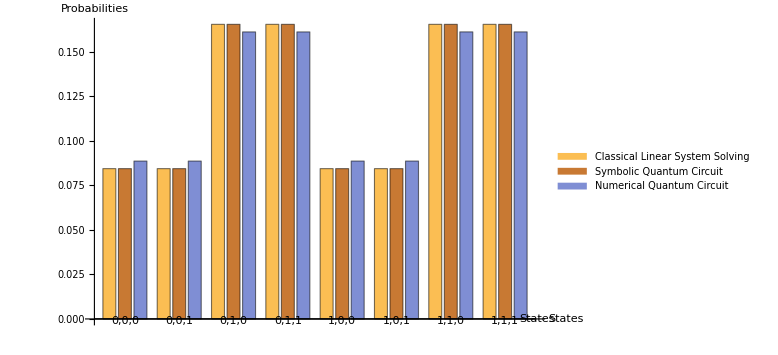

```mathematica
BarChart[Transpose[{LinearSystemResult,Values@SymbolicResult,Values@NumericalResult}],ChartLayout->"Grouped",ChartLabels->{Delete[0]@#&/@Tuples[{"0","1"},3],None},ChartLegends->{"Classical Linear System Solving","Symbolic Quantum Circuit","Numerical Quantum Circuit"},ImageSize->Large,AxesLabel->{"States","Probabilities"}]
```

#### QLSP randomly generated

Bravo-Prieto showcase a Randomly generate A matrix:

A=ξ_1(𝟙+ξ_2∑_j ∑_(k ≠j) p a_(j,k)(σ^α)_j(σ^β)_k)

where p follows a binominal distribution, a ϵ (-1,1) and σ are Pauli matrices.

Following the equation, we will consider the following A matrix:

A=1/(8κ)(4(κ+1)𝟙+(κ-1)Z_4+Z_3+2 Z_2)=_(κ->2) (0.75𝟙+0.0625 Z_4+0.0625 Z_3+0.125 Z_2)

and we are given the state:

b=H_2 H_3 H_4 0

Given the ansatz

x=V(ω)0=[R_y(ω_1)⊗R_y(ω_2)⊗R_y(ω_3)]CZ_(2,3)CZ_(2,4)[R_y(ω_4)⊗R_y(ω_5)⊗R_y(ω_6)]CZ_(3,4)CZ_(2,4)[R_y(ω_7)⊗R_y(ω_8)⊗R_y(ω_9)]H_2 H_3 H_4 0

##### Circuit Implementation

Following the same steps, we define the gates associated with the example:

The unitary matrix such that b=U_b 0 :

```mathematica
Ub=QuantumCircuitOperator[{"Hadamard"->{2,3,4}},"Label"->"U_b"];
```

Controlled gates A_l and controlled Z_j :

```mathematica
ControlledGateA=QuantumOperator[QuantumOperator["I"]*KroneckerDelta[l,2]+QuantumOperator[{"CZ"->{1,4}}]*KroneckerDelta[l,3]+QuantumOperator[{"CZ"->{1,3}}]*KroneckerDelta[l,4]+
QuantumOperator[{"CZ"->{1,2}}]*KroneckerDelta[l,5]
,
"Parameters"->{l},
"Label"->"Controlled A_l Gate"];
```

```mathematica
ControlledGateZ=QuantumOperator[
QuantumOperator["CZ"->{1,2}]*KroneckerDelta[j,2]+QuantumOperator["CZ"->{1,3}]*KroneckerDelta[j,3]+QuantumOperator["CZ"->{1,4}]*KroneckerDelta[j,4]+QuantumOperator["I"]*KroneckerDelta[j,-1],
"Parameters"->{j},
"Label"->"Controlled Z_j Gate"
];
```

Ansatz variational circuit:

```mathematica
VariationalBlock=QuantumCircuitOperator[
{"Hadamard"->{1,2,3},
"RY"[ω1]->{1},"RY"[ω2]->{2},"RY"[ω3]->{3},
"CZ"->{1,2},"CZ"->{1,3},
"RY"[ω4]->{1},"RY"[ω5]->{2},"RY"[ω6]->{3},
"CZ"->{2,3},"CZ"->{1,3},
"RY"[ω7]->{1},"RY"[ω8]->{2},"RY"[ω9]->{3}
},
"Label"->"V(ω)","Parameters"->{ω1,ω2,ω3,ω4,ω5,ω6,ω7,ω8,ω9}];
```

In order to obtain μ_(l , l', j) we will implement a circuit that will deploy a Hadamard test:

As the previous example, we implement the Hadamard test:

```mathematica
ClearAll[LocalHadamardCircuit];
LocalHadamardCircuit=QuantumCircuitOperator[{
"Hadamard"->{1},
"P"[θ],
VariationalBlock->{2,3,4},
ControlledGateA,
Ub,
ControlledGateZ,
Ub,
ControlledGateA[<|l->lp|>],
"Hadamard"->{1}
},"Parameters"->{ω1,ω2,ω3,ω4,ω5,ω6,ω7,ω8,ω9,l,lp,j,θ}];
```

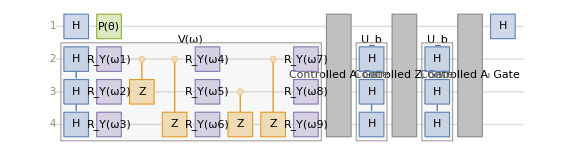

```mathematica
LocalHadamardCircuit["Diagram",ImageSize->Large]
```

##### Local Cost Function

Calculate the symbolic mean value of our function:

```mathematica
LocalHadamardState=LocalHadamardCircuit[];
```

```mathematica
LocalHadamardStateVector=Normal[LocalHadamardState["StateVector"]];
```

Since it can be a heavy computation, we will compute  the state vector variations on the variables that are not part of the Variational Circuit V(ω). Remember that l and l,p correspond to the controlled A_l gates index (from 2 to 5) and j to the qubits (from 2 to 4 and -1 for the normalization term):

```mathematica
LocalHadamardStateVectors=Association@Table[
Rule[{𝕝,𝕝𝕡,𝕛},N@Replace[LocalHadamardStateVector,{l->𝕝,lp->𝕝𝕡,j->𝕛},{7,12}]],
{𝕝,{2,3,4,5}},{𝕝𝕡,{2,3,4,5}},{𝕛,{-1,2,3,4}}];//AbsoluteTiming
```

{14.2163,Null}

Now we will implement the functions to calculate the local cost for this circuit:

```mathematica
H=Normal[QuantumOperator[{"Z"->{1},"I"->{2,3,4}}]["Matrix"]];
```

In this LocalHadamardMeanValues version, we call LocalHadamardStateVectors[{l, lp, j}] for the state vector already computed to save time per each execution of LocalCost:

```mathematica
ClearAll[LocalHadamardMeanValues];
LocalHadamardMeanValues[v1_,v2_,v3_,v4_,v5_,v6_,v7_,v8_,v9_,l_,lp_,j_]:=Module[{ket,bra},
ket=Replace[LocalHadamardStateVectors[{l,lp,j}],Thread[Rule[{ω1,ω2,ω3,ω4,ω5,ω6,ω7,ω8,ω9},{v1,v2,v3,v4,v5,v6,v7,v8,v9}]],{6,23}];
bra=ConjugateTranspose[ket];
bra.H.ket
]
```

Define  μ_(l,v,j) :

```mathematica
ClearAll[μ]
μ[v1_,v2_,v3_,v4_,v5_,v6_,v7_,v8_,v9_,l_,lp_,j_]:=Module[{mu,μRe,μIm},
mu=LocalHadamardMeanValues[v1,v2,v3,v4,v5,v6,v7,v8,v9,l,lp,j];
μRe=Replace[mu,θ->0,{6,7}];
μIm=Replace[mu,θ->-π/2,{6,7}];
N[μRe + j μIm]
]
```

Implement the normalization term:

```mathematica
c={0,0.75,0.0625,0.0625,0.125};
```

```mathematica
ClearAll[PsiNorm];
PsiNorm[w1_?NumericQ,w2_?NumericQ,w3_?NumericQ,w4_?NumericQ,w5_?NumericQ,w6_?NumericQ,w7_?NumericQ,w8_?NumericQ,w9_?NumericQ]:=Abs[
Sum[
c[[l]]*Conjugate[c[[lp]]]*μ[w1,w2,w3,w4,w5,w6,w7,w8,w9,l,lp,-1],
{l,{2,3,4,5}},{lp,{2,3,4,5}}
]
];
```

Following the C_L equation, we define the cost function:

```mathematica
ClearAll[LocalCost];
LocalCost[w1_?NumericQ,w2_?NumericQ,w3_?NumericQ,w4_?NumericQ,w5_?NumericQ,w6_?NumericQ,w7_?NumericQ,w8_?NumericQ,w9_?NumericQ]:=0.5-((0.5/(3*PsiNorm[w1,w2,w3,w4,w5,w6,w7,w8,w9]))*Abs[
Sum[
c[[l]]*Conjugate[c[[lp]]]*μ[w1,w2,w3,w4,w5,w6,w7,w8,w9,l,lp,j],
{l,{2,3,4,5}},{lp,{2,3,4,5}},{j,{2,3,4}}
]
]
);
```

##### Cost Function Optimization

We will calculate the gradient descent for our cost function:

```mathematica
w= 0.001 *RandomVariate[NormalDistribution[],9];
```

```mathematica
GradientParameters=GradientDescent[LocalCost,w,"MaxIterations"->40,"LearningRate"->0.8];//AbsoluteTiming
```

{2286.16,Null}

```mathematica
lc=LocalCost@@@GradientParameters;//AbsoluteTiming
```

{157.964,Null}

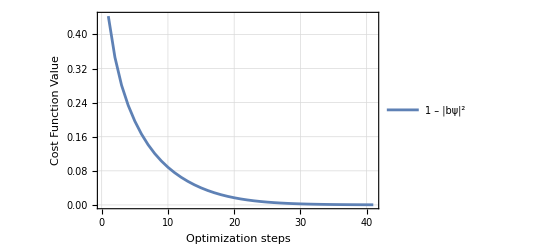

```mathematica
ListPlot[lc,Joined->True,GridLines->Automatic,PlotRange->All,Frame->True,FrameLabel->{"Optimization steps","Cost Function Value"},PlotLegends->{"1 – |bψ|^2"}]
```

##### Classical Linear System Solving

We can build the A matrix and stateb of the present problem:

A= (0.75𝟙+0.0625 Z_4+0.0625 Z_3+0.125 Z_2)

b =H_2 H_3 H_4 0

Solve the system by operating over the correspondent matrices:

```mathematica
A2=IdentityMatrix[8];
A3=KroneckerProduct[IdentityMatrix[2],IdentityMatrix[2],PauliMatrix[3]];
A4=KroneckerProduct[IdentityMatrix[2],PauliMatrix[3],IdentityMatrix[2]];
A5=KroneckerProduct[PauliMatrix[3],IdentityMatrix[2],IdentityMatrix[2]];
```

```mathematica
A=c[[2]]*A2+c[[3]]*A3+c[[4]]*A4+c[[5]]*A5;
b=ConstantArray[1/Sqrt[8],8];
{"A"->MatrixForm[A],"b"->MatrixForm[b]}//N
```

{A→(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.875 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.875 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.75 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.75 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.625 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.625 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5),b→(0.353553
0.353553
0.353553
0.353553
0.353553
0.353553
0.353553
0.353553)}

Finally, compute the probabilities:

```mathematica
LinearSystemResult=Normalize[LinearSolve[A,b]]^2;
Thread[Delete[0]@#&/@Tuples[{SubPlus[z],SubMinus[z]},3]->LinearSystemResult]
```

{z_+,z_+,z_+→0.0613956,z_+,z_+,z_-→0.0801902,z_+,z_-,z_+→0.0801902,z_+,z_-,z_-→0.109148,z_-,z_+,z_+→0.109148,z_-,z_+,z_-→0.157173,z_-,z_-,z_+→0.157173,z_-,z_-,z_-→0.245583}

##### Symbolic & Numeric Quantum Circuit Result

We can build the Variational circuit from the example and test it with the optimized parameters result:

Test the Variational circuit with the optimized parameters results:

```mathematica
VariationalMeasurement=QuantumCircuitOperator[{VariationalBlock,QuantumMeasurementOperator["Z"->{1,-1},{1,2,3}]}][];
```

The optimization resultant probabilities:

```mathematica
NumericalResult=VariationalMeasurement[AssociationThread[{ω1,ω2,ω3,ω4,ω5,ω6,ω7,ω8,ω9},Last@GradientParameters]]["Probabilities"]
```

<|𝓏_+𝓏_+𝓏_+→0.0621861,𝓏_+𝓏_+𝓏_−→0.0832131,𝓏_+𝓏_−𝓏_+→0.0816941,𝓏_+𝓏_−𝓏_−→0.10831,𝓏_−𝓏_+𝓏_+→0.119605,𝓏_−𝓏_+𝓏_−→0.168693,𝓏_−𝓏_−𝓏_+→0.144291,𝓏_−𝓏_−𝓏_−→0.232007|>

We can calculate how different one distribution is from another using the Kullback–Leibler divergence:

```mathematica
Total[#[[1]]*Log[#[[1]]/#[[2]]]&/@Thread[{LinearSystemResult,Values@NumericalResult}]]
```

0.00189974

Since the results are small, it is an indicator that the distributions are similar.

We can also employ a Kolmogorov Smirnov Test:

```mathematica
KolmogorovSmirnovTest[Values@NumericalResult,LinearSystemResult]
```

0.955245

In this case, the number is considered big enough to indicate that the results are from the reference distribution.

Let’s plot the probabilities for a visual comparison:

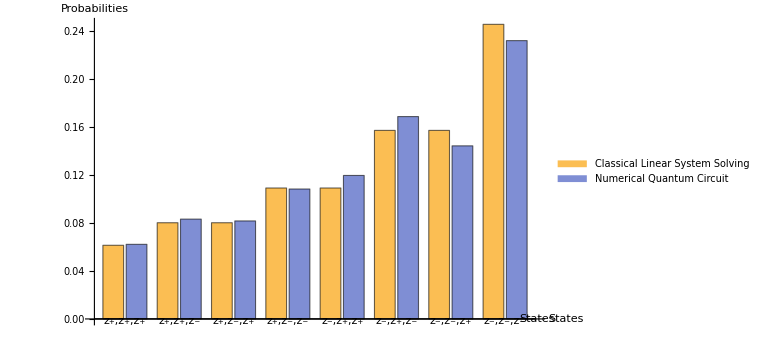

```mathematica
BarChart[Transpose[{LinearSystemResult,Values@NumericalResult}],ChartLayout->"Grouped",ChartLabels->{Delete[0]@#&/@Tuples[{SubPlus[z],SubMinus[z]},3],None},ChartLegends->{"Classical Linear System Solving","Numerical Quantum Circuit"},ImageSize->Large,AxesLabel->{"States","Probabilities"}]
```

### Multiplexer-based Variational Quantum Linear Solver (MB-VQLS)

The Variational Quantum Linear Solver (VQLS) is a hybrid quantum-classical technique designed to address Quantum Linear Systems Problems (QLSP). The main goal is to find linear solutions for systems as m.x=b.

In this Tech Note we will explain the applications and options of QuantumLinearSolve function implemented in the Wolfram Quantum Computation Framework to solve QLSP problems.

QuantumLinearSolve[m,b,opts] | uses a hybrid optimization algorithm to find a quantum state described by the state vector x  that satisfies m.x=b.
QuantumLinearSolve[m,b,prop,opts] | solves m.x=b by including the specified properties prop.

We will briefly demonstrate how to apply all these functions in Wolfram quantum framework.

#### Details and Options

QuantumLinearSolve works on numerical matrices. The argument b must be a vector, while the argument m must be a square matrix. QuantumLinearSolve is able to compute solutions for 2^n–dimension problems.

QuantumLinearSolve utilizes a multiplexer-based variational quantum linear solver algorithm. The primary distinctions from a conventional variational quantum linear solver algorithm are as follows:

The multiplication of the matrix m is implemented by a multiplexer, enabling the accurate representation of the operation A.x within the quantum circuit.

The solution to the linear system is encoded directly in the amplitudes of the resultant quantum state.

This approach simplifies the standard variational quantum linear solver by reducing the need for multiple circuits used in the real-imaginary decomposition of the solution and the term-by-term computation within quantum circuits. A detailed step-by-step implementation is outlined in this documentation.

The basic steps to implement the algorithm are the following:

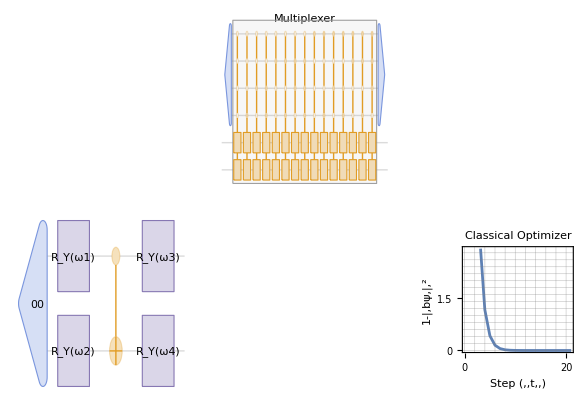

Start with a variational circuit ansatz V(ω_i) or directly an state ansatz x(ω_i)=V(ω_i)0

Apply the multiplexer to perform m.x(ω_i) and obtain resultant ψ(ω_i) state

Use ψ(ω_i) state as the input for the optimizer with the cost function f(ω)=1- |bψ(ω),,|,^2 to obtain new ω_j parameters

Use new ω_j parameters with the variational circuit V(ω_i) or state ansatz x(ω_j)

Repeat the process until you obtain  f(ω_opt)=1- |bψ(ω_opt),,|,^2=0

#### Example

##### Simple example

Generate a random 4×4 real matrix:

```mathematica
m=RandomReal[{0,1},{4,4}];
m//MatrixForm
```

(0.596166 | 0.62566 | 0.816575 | 0.857365
0.287865 | 0.236078 | 0.491353 | 0.593494
0.786389 | 0.0297055 | 0.638947 | 0.00472644
0.736549 | 0.108758 | 0.314166 | 0.0812839)

Generate a random complex vector of the length 4:

```mathematica
b=RandomComplex[{-0.1-0.1I,0.1+0.1I},4]
```

{0.0170825+0.049994 ⅈ,0.027093+0.091541 ⅈ,0.0806183-0.0000258573 ⅈ,-0.0829871-0.0489408 ⅈ}

Use them as input in the QuantumLinearSolve:

```mathematica
QuantumLinearSolve[m,b]
```

{-0.287755-0.110093 ⅈ,-0.0772302-0.274276 ⅈ,0.485296+0.146765 ⅈ,-0.185835+0.195234 ⅈ}

When running above code, you may see a progress box describing steps and estimated time.

Find the solution using LinearSolve:

```mathematica
LinearSolve[m,b]
```

{-0.287755-0.110093 ⅈ,-0.0772302-0.274276 ⅈ,0.485296+0.146764 ⅈ,-0.185835+0.195234 ⅈ}

Compare the results:

```mathematica
%%-%//Abs
```

{4.17675×10^-8,2.38047×10^-7,5.30811×10^-8,1.74998×10^-7}

##### Properties

You can request the components used during the calculation using a third property argument:

"Ansatz" | Returns only the QuantumState ansatz used to solve the QLSP.
"CircuitOperator" | Returns only the QuantumCircuitOperator variational circuit ψ  used to solve the QLSP.
"GlobalPhase" | Includes in solution the calculated global phase ⟨ⅇ^ⅈϕ⟩ between the optimized ψ and vector b problem.
"OptimizedParameters" | Return optimized values of defined parameters.
"Parameters" | Return systems defined parameters.

Show the ansatz quantum state used for parameter optimization"

```mathematica
QuantumLinearSolve[m, b, "Ansatz"]
```

QuantumState[…]

Show the quantum circuit used for parameter optimization:

```mathematica
QuantumLinearSolve[m,b,"CircuitOperator"]
```

QuantumCircuitOperator[…]

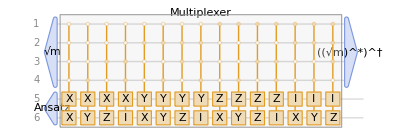

```mathematica
%["Diagram",ImageSize->Full]
```

Request more than one property:

```mathematica
QuantumLinearSolve[m,b,{"Result","Ansatz","GlobalPhase"}]
```

<|Result→{-0.287755-0.110093 ⅈ,-0.0772302-0.274275 ⅈ,0.485296+0.146765 ⅈ,-0.185835+0.195234 ⅈ},Ansatz→QuantumState[…],GlobalPhase→-0.23026347-0.46098513 ⅈ0.00000014|>

Request them all using All as third argument:

```mathematica
QuantumLinearSolve[m,b,All]
```

<|Result→{-0.287755-0.110093 ⅈ,-0.0772302-0.274276 ⅈ,0.485296+0.146764 ⅈ,-0.185835+0.195234 ⅈ},Ansatz→QuantumState[…],CircuitOperator→QuantumCircuitOperator[…],GlobalPhase→-0.1262380751-0.5656420931 ⅈ0.0000000015,OptimizedParameters→{ω$1→-0.30641,ω$2→-1.71692,ω$3→0.256882,ω$4→1.58111,ω$5→2.0862,ω$6→0.924735,ω$7→-3.46036,ω$8→0.950259},Parameters→{ω$1,ω$2,ω$3,ω$4,ω$5,ω$6,ω$7,ω$8}|>

#### Algorithm Components

##### Ansatz

Generate a variational state in 4D:

```mathematica
QuantumState[{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[ω, 4]},"Parameters"->{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[ω, 4]},"Label"->"Ansatz"]
```

QuantumState[…]

Show its formula:

```mathematica
%["Formula"]
```

ω_1 00+ω_2 01+ω_3 10+ω_4 11

Represent it directly in a quantum circuit:

```mathematica
%%["CircuitDiagram",ImageSize->Small]
```

-Graphics-

Request "Ansatz" from QuantumLinearSolve function:

```mathematica
QuantumLinearSolve[
RandomReal[{0,1},{4,4}],
RandomComplex[(1+I) {-.1,.1},4],
"Ansatz"
]
```

QuantumState[…]

```mathematica
%["Formula"]
```

(ω$1+ⅈ ω$5)00+(ω$2+ⅈ ω$6)01+(ω$3+ⅈ ω$7)10+(ω$4+ⅈ ω$8)11

All parameters are real in above equation.

##### Multiplexer

The Multiplexer encodes all the information from m matrix problem into the quantum circuit and simulates the m.x operation in the quantum circuit. First, we need to decompose a 2^n x2^n m–matrix in Pauli matrices such that m=∑_i m_i(⊗^n σ).

```mathematica
m=RandomReal[{-1,1},{4,4}];
m//MatrixForm
```

(-0.0354706 | 0.993407 | -0.017167 | 0.106304
-0.226915 | -0.685786 | 0.136567 | 0.855628
0.756968 | 0.252897 | -0.582114 | -0.233798
-0.205079 | 0.521351 | -0.514888 | 0.353328)

```mathematica
x=RandomComplex[{-1-1*I,+1+1*I},4]
```

{-0.549572-0.184549 ⅈ,-0.716395+0.14797 ⅈ,0.0782603-0.00683114 ⅈ,-0.926382-0.842977 ⅈ}

Use QuantumOperator property to obtain the Pauli decomposition of matrix m:

```mathematica
σ=QuantumOperator[m]["PauliDecompose"]
```

<|XX→0.0726722+0. ⅈ,XY→0.+0.106928 ⅈ,XZ→-0.159295+0. ⅈ,XI→0.529195+0. ⅈ,YX→0.+0.0487632 ⅈ,YY→0.12206+0. ⅈ,YZ→0.-0.277103 ⅈ,YI→0.-0.109964 ⅈ,ZX→0.378795+0. ⅈ,ZY→0.+0.234808 ⅈ,ZZ→0.396439+0. ⅈ,ZI→-0.123118+0. ⅈ,IX→0.00445141+0. ⅈ,IY→0.+0.375353 ⅈ,IZ→-0.0712818+0. ⅈ,II→-0.23751+0. ⅈ|>

It is possible to apply the tensor product of Pauli matrices as controlled operations:

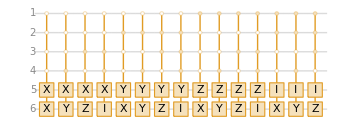

```mathematica
QuantumCircuitOperator["Multiplexer"@@Keys[σ]]["Diagram"]
```

Use the squared-roots constants √m_i to define a quantum state to act on the control qubits and use vector x QuantumState in the taget qubits:

```mathematica
QuantumCircuitOperator[{QuantumState[x,"Label"->"x"]->{5,6},
QuantumState[Sqrt[Values[σ]],"Label"->"√m"],
"Multiplexer"@@Keys[σ],
SuperDagger[QuantumState[Sqrt[Values[σ]],"Label"->"√m"]["Conjugate"]]
}
]
```

QuantumCircuitOperator[…]

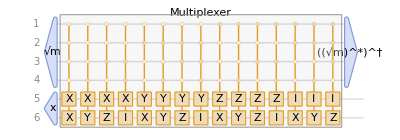

```mathematica
%["Diagram",ImageSize->Full]
```

Visualize the application the multiplexer as the representation of m.x operation:

```mathematica
%%[]["AmplitudesList"]
```

{-0.791999+0.0640462 ⅈ,-0.165952-0.781807 ⅈ,-0.426153+0.098786 ⅈ,-0.6284-0.179339 ⅈ}

```mathematica
m.x
```

{-0.791999+0.0640462 ⅈ,-0.165952-0.781807 ⅈ,-0.426153+0.098786 ⅈ,-0.6284-0.179339 ⅈ}

In contrast with the circuit implemented above, in this variational problem we are given matrix m and vector b, so we do not know the value for x such that A.x=b. In order to look up for it, we need to change x->x(ω). This change will establish our variational circuit, necessitating the design of an ansatz circuit to generate the corresponding state. In this case, we can use Wolfram Quantum Framework tools to generate a variational state x(ω) symbolically.

Request "CircuitOperator" from QuantumLinearSolve function to obtain the variational circuit including the multiplexer and the variational ansatz:

```mathematica
QuantumLinearSolve[
RandomReal[{0,1},{4,4}],
RandomReal[{-0.1,+0.1},4],
"CircuitOperator"
]
```

QuantumCircuitOperator[…]

```mathematica
%["Diagram",ImageSize->Full]
```

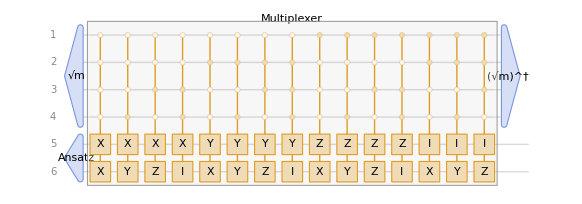

The resultant state ψ(ω) from this variational circuit:

```mathematica
ψ=%%
```

QuantumState[…]

##### Cost Function

We are recovering our results from state’s amplitudes and there are some consideration to take on account. The cost function f(ω) we defined previously depends heavily on the quantum fidelity from b and ψ states:

f(ω)=0↔ℱ=|bψ(ω_opt)|,^2=1

```mathematica
CostFunction[v1_,v2_,v3_,v4_]:=
QuantumDistance[QuantumState[b]["Normalize"],ψ[v1,v2,v3,v4]["Normalize"],"Fidelity"];
```

The cost function minimization ensures that the probability distributions of b and ψ are identical, such that:

ψ(ω_opt)=ⅇ^ⅈϕ b

In other words, this cost function does not ensure that the amplitudes of both states are identical, but rather that they are proportional by a global phase:

ψ=∑α_i i &b=∑β_i i ->α_i=ⅇ^ⅈϕ β_i

In order to correct our result, we need to find the global phase and apply it along with the normalization terms for both b and m once our calculation is done such that:

x_sol=1/ⅇ^ⅈϕ(||b||)/(||m||)x(ω_opt)

#### Algorithm Implementation

##### Initial problem setup

In order to implement this algorithm, we will start coding a simple example using a random vector b and a random A matrix:

```mathematica
matrixA=RandomReal[{0,1},{4,4}];
```

```mathematica
matrixA//MatrixForm
```

(0.909708 | 0.494552 | 0.49149 | 0.862494
0.724248 | 0.484333 | 0.413379 | 0.721778
0.128352 | 0.905764 | 0.193863 | 0.0352042
0.509416 | 0.602268 | 0.0978288 | 0.510178)

```mathematica
vectorb=RandomReal[{-0.1,+0.1},4]
```

{0.0695503,-0.0689988,0.0678855,0.0997898}

We need to save the normalization terms, since we will be working with the normalized matrix and vector:

```mathematica
normA=Norm[matrixA];
normb=Norm[vectorb];
```

In later steps, we will refer to b̂ and Â as the normalized vector b and matrix A, respectively. Then the solution for the Â and b̂ problem would be called x^(^\b)(θ_opt). Applying b and A normalization terms will help us recover the original A.x(θ_opt)=b solution.

##### Multiplexer implementation

First, we need to decompose Â in Pauli matrices such that Â=∑c_i A_i:

```mathematica
pauliDecompose=QuantumOperator[matrixA/normA]["PauliDecompose"];
```

```mathematica
pauliDecompose
```

<|XX→0.312427+0. ⅈ,XY→0.+0.098157 ⅈ,XZ→-0.081757+0. ⅈ,XI→0.225682+0. ⅈ,YX→0.-0.0161733 ⅈ,YY→-0.00612614+0. ⅈ,YZ→0.+0.0282848 ⅈ,YI→0.+0.0560347 ⅈ,ZX→0.126056+0. ⅈ,ZY→0.-0.0193967 ⅈ,ZZ→0.0861091+0. ⅈ,ZI→0.0801079+0. ⅈ,IX→0.156946+0. ⅈ,IY→0.-0.033938 ⅈ,IZ→0.0126617+0. ⅈ,II→0.243584+0. ⅈ|>

Next, implement the multiplexer:

```mathematica
multiplexer=QuantumCircuitOperator["Multiplexer"@@Keys[pauliDecompose]];
```

```mathematica
ancillary=QuantumState[Sqrt@Values[pauliDecompose],"Label"->"√c"];
```

We obtain the first section of the variational circuit for the VQLS:

```mathematica
qlscircuit=QuantumCircuitOperator[{
ancillary,
multiplexer,
SuperDagger[(ancillary["Conjugate"])]
}];
```

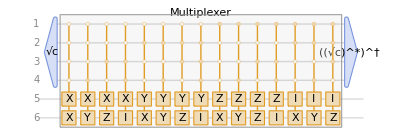

```mathematica
qlscircuit["Diagram",ImageSize->Full]
```

##### General symbolic ansatz

Define a general state ansatz for 4-qubits with real amplitudes. Remember we are working with x̂(ω) instead of x(ω); label it so we do not forget about it:

```mathematica
parameters=GenerateParameters[1,4];
ansatz=QuantumState[parameters,"Label"->"x̂(θ)","Parameters"->parameters];
```

```mathematica
ansatz["Formula"]
```

θ100+θ201+θ310+θ411

Finally, we implement the circuit and the correspondent state:

```mathematica
vqlscircuit=qlscircuit[QuantumOperator[ansatz->{5,6}]];
```

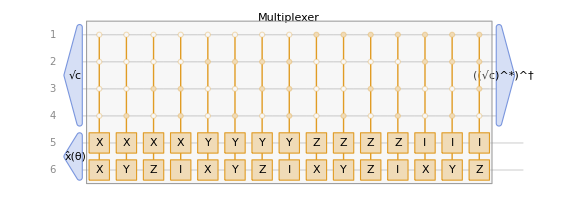

```mathematica
vqlscircuit["Diagram",ImageSize->Large]
```

Wolfram Quantum Framework quantum states (and measurements) keep the parameters defined in previously used circuits, so it would be optimum to work with the resultant state:

```mathematica
ψ=vqlscircuit[]
```

QuantumState[…]

We can perform a first test to obtain ψ(ω_init)=Â.x̂(θ_init):

```mathematica
init=Normalize[0.01*RandomVariate[NormalDistribution[],4]]
```

{0.264994,-0.411396,-0.784879,-0.380126}

```mathematica
ψ[AssociationThread[parameters->init]]["Table"]
```

| 1
00 | -0.313933+0. ⅈ
01 | -0.281493+0. ⅈ
10 | -0.234128+0. ⅈ
11 | -0.178093+0. ⅈ

As we can see, it is not close enough to b̂ in order to call it a good approximation:

```mathematica
QuantumState[vectorb/normb]["Table"]
```

| 1
00 | 0.447414
01 | -0.443866
10 | 0.436705
11 | 0.641944

##### Optimization

Implement the cost functions previously defined, remember to use the normalized vector b:

```mathematica
qb=QuantumState[vectorb/normb]["Normalize"];
```

```mathematica
fidelity[v1_,v2_,v3_,v4_]:=QuantumDistance[qb,ψ[v1,v2,v3,v4]["Normalize"],"Fidelity"];
```

Now, let’s optimize the cost function using FindMinimum, with our initial guess as the starting point:

```mathematica
ip=Thread[{parameters,init}];
optFM=FindMinimum[fidelity[θ1,θ2,θ3,θ4],ip];//Quiet
```

```mathematica
optFM
```

{0.180515,{θ1→-1.31557×10^10,θ2→-2.58751×10^9,θ3→1.14111×10^10,θ4→8.36485×10^9}}

As we can see, FindMinimum is having some difficulty finding the minimal value, so we might switch to NMinimize, which will return a value for the cost function that is very close to zero:

```mathematica
optNM=NMinimize[fidelity[θ1,θ2,θ3,θ4],{θ1,θ2,θ3,θ4}];
```

```mathematica
optNM
```

{1.42109×10^-14,{θ1→2.73792×10^9,θ2→-6.78883×10^7,θ3→-7.73907×10^8,θ4→-2.33952×10^9}}

Let’s compare the probability distribution of ψ(θ) and b probability distributions:

```mathematica
Dataset[<|"ψ"->ψ[<|Last[optNM]|>]["Probabilities"],"b"->QuantumState[vectorb/normb]["Probabilities"]|>]//Transpose
```

As we can notice, the values are quite close! However, as mentioned earlier, while the probability distributions match, the amplitudes do not necessarily align:

```mathematica
Dataset[<|"ψ"->ψ[<|Last[optNM]|>]["Amplitudes"],"b"->QuantumState[vectorb/normb]["Amplitudes"]|>]//Transpose
```

This is basically is saying that we found ψ(θ_opt)=ⅇ^ⅈϕ b̂:

```mathematica
optψ=ψ[<|Last@optNM|>]["AmplitudesList"]
```

{2.73736×10^7+0. ⅈ,-2.71565×10^7+0. ⅈ,2.67183×10^7+0. ⅈ,3.92752×10^7+0. ⅈ}

The following step is to obtain the global phase ⅇ^ⅈϕ. We can check that it is the same for each amplitude:

```mathematica
globalphase=optψ/(vectorb/normb)
```

{6.11817×10^7+0. ⅈ,6.11817×10^7+0. ⅈ,6.11817×10^7+0. ⅈ,6.11817×10^7+0. ⅈ}

We can verify 1/ⅇ^ⅈϕ ψ(ω_opt)=b̂ using the mean value of the global phase:

```mathematica
1/Mean[globalphase]*optψ-qb["AmplitudesList"]//Chop
```

{-1.26408×10^-7,7.94917×10^-8,6.21723×10^-8,2.04941×10^-7}

Calculate x̂(θ_opt):

```mathematica
optX=ansatz[<|Last@optNM|>]["AmplitudesList"]
```

{2.73792×10^9,-6.78883×10^7,-7.73907×10^8,-2.33952×10^9}

Now recover x(ω_opt) by applying the global phase and normalization terms: x(ω_opt)=1/ⅇ^iϕ(||b||)/(||A||)x̂(ω_opt):

```mathematica
1/Mean[globalphase]*normb/normA*optX//Chop
```

{3.23053,-0.0801031,-0.913152,-2.76045}

We can verify our result:

```mathematica
LinearSolve[matrixA,vectorb]
```

{3.23053,-0.0801031,-0.913152,-2.76045}

```mathematica
%%-%//Abs
```

{6.29597×10^-7,7.79645×10^-8,6.58594×10^-9,6.00327×10^-7}

##### Optimization using Quantum Natural Gradient Descent

As explained in a previous example, we can optimize using QuantumNaturalGradientDescent, calculating their correspondent Fubini–Study metric tensor.

A useful question to consider is: “Which state are we using in the Fubini-Study metric tensor function?” In this context, the ansatz does not capture the full geometry of the problem, so the most appropriate choice is the variational state ψ, which is parameterized and encodes the essential information about the system.

```mathematica
fubini=FubiniStudyMetricTensor[ψ];
```

Let’s try with a pair of steps on the optimizer with η->0.6:

```mathematica
opt=GradientDescent[fidelity,init,"LearningRate"->0.6,"MaxIterations"->2];
```

```mathematica
qopt=QuantumNaturalGradientDescent[fidelity,fubini,"InitialPoint"->init,"LearningRate"->0.6,"MaxIterations"->2];
```

The result is quite remarkable: the Quantum Natural Gradient Descent outperforms regular gradient descent and reaches the minimum value in only two steps!

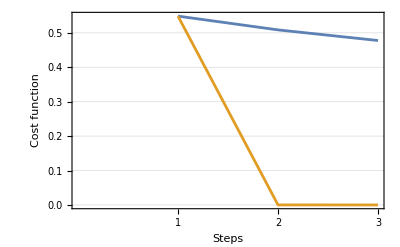

```mathematica
ListLinePlot[{fidelity@@@opt,fidelity@@@qopt},
Frame->True,FrameLabel->{"Steps","Cost function"},
GridLines->Automatic,FrameTicks->{Automatic,{Range[3],None}}]
```

We can verify that the minimization approaches to 0:

```mathematica
fidelity@@@qopt//Last
```

0.0000146428

Checkψ(θ) and b probability distributions:

```mathematica
association=AssociationThread[parameters,Last@qopt];
```

```mathematica
Dataset[<|"ψ"->ψ[association]["Probabilities"],"b"->QuantumState[vectorb/normb]["Probabilities"]|>]//Transpose
```

As you may have noticed, the probabilities match, but with less precision in this case. However, the amplitudes are completely different, and they even have different signs!

```mathematica
Dataset[<|"ψ"->ψ[association]["Amplitudes"],"b"->QuantumState[vectorb/normb]["Amplitudes"]|>]//Transpose
```

This is basically is saying that we found ψ(θ_opt)=ⅇ^ⅈϕ b̂:

```mathematica
optψ=ψ[association]["AmplitudesList"]
```

{-0.516727+0. ⅈ,0.520752+0. ⅈ,-0.505349+0. ⅈ,-0.745124+0. ⅈ}

The following step is to obtain the global phase ⅇ^ⅈϕ:

```mathematica
globalphase=optψ/(vectorb/normb)
```

{-1.15492+0. ⅈ,-1.17322+0. ⅈ,-1.15719+0. ⅈ,-1.16073+0. ⅈ}

Now, during the process of obtaining the global phase, we observe that the values are not exactly the same. In this case, when we use the mean value of the global phase, we can check that the deviation is small enough for the desired precision.

Calculate x(θ_opt):

```mathematica
optX=ansatz[association]["AmplitudesList"]
```

{-52.117+0. ⅈ,1.29782+0. ⅈ,14.7413+0. ⅈ,44.5355+0. ⅈ}

Now recover x(ω_opt) by applying the global phase and normalization terms x(ω_opt)=1/ⅇ^iϕ(||b||)/(||A||)x̂(ω_opt):

```mathematica
1/Mean[globalphase]*normb/normA*optX//Chop
```

{3.23915,-0.0806614,-0.916192,-2.76794}

We can verify our result approximation:

```mathematica
LinearSolve[matrixA,vectorb]
```

{3.23053,-0.0801031,-0.913152,-2.76045}

```mathematica
%%-%//Abs
```

{0.00861713,0.000558259,0.00304054,0.00749401}

After repeating all the same steps from the previous example, we get a final result that is close to the true result but with slightly less precision. What’s remarkable about this solution is that we achieved it in only two steps! Of course, the results depend heavily on the learning rate eta, so it’s important to fine-tune it to ensure that the optimization is done efficiently.

#### Options

"Ansatz" | Automatic | use specified ansatz instead of the one generated by the function
"GlobalPhaseAccuracy" | 10^-5 | expected accuracy for global phase estimation
AccuracyGoalhttps://reference.wolfram.com/language/ref/AccuracyGoal.htmlNonehttps://reference.wolfram.com/language/ref/AccuracyGoal.htmlHyperlinkActionRecycledHyperlinkActive | Automatic | number of digits of final accuracy sought
MaxIterationshttps://reference.wolfram.com/language/ref/MaxIterations.htmlNonehttps://reference.wolfram.com/language/ref/MaxIterations.htmlHyperlinkActionRecycledHyperlinkActive | Automatic | maximum number of iterations to use
Methodhttps://reference.wolfram.com/language/ref/Method.htmlNonehttps://reference.wolfram.com/language/ref/Method.htmlHyperlinkActionRecycledHyperlinkActive | Automatic | method to use
PrecisionGoalhttps://reference.wolfram.com/language/ref/PrecisionGoal.htmlNonehttps://reference.wolfram.com/language/ref/PrecisionGoal.htmlHyperlinkActionRecycledHyperlinkActive | Automatic | number of digits of final precision sought
WorkingPrecisionhttps://reference.wolfram.com/language/ref/WorkingPrecision.htmlNonehttps://reference.wolfram.com/language/ref/WorkingPrecision.htmlHyperlinkActionRecycledHyperlinkActive | MachinePrecisionhttps://reference.wolfram.com/language/ref/MachinePrecision.htmlNonehttps://reference.wolfram.com/language/ref/MachinePrecision.htmlHyperlinkActionRecycledHyperlinkActive | the precision used in internal computations

##### Ansatz

You can specify the ansatz to be used as a QuantumState or QuantumCircuitOperator:

```mathematica
ansatz=QuantumState[{α1,α2,α3,α4},{1,2},"Parameters"->{α1,α2,α3,α4}];
ansatz["Formula"]
```

α100+α201+α310+α411

```mathematica
m=RandomReal[{0,1},{4,4}]
```

{{0.251149,0.632406,0.00760061,0.451067},{0.768939,0.771227,0.223159,0.103032},{0.553352,0.929828,0.0607338,0.399935},{0.778583,0.8705,0.598142,0.676169}}

```mathematica
b=RandomReal[{0,1},4]
```

{0.732115,0.567505,0.576803,0.848305}

```mathematica
QuantumLinearSolve[m,b,"Ansatz"->ansatz]
```

{12.147+0. ⅈ,-9.61246+0. ⅈ,-10.0188+0. ⅈ,8.50546+0. ⅈ}

Compare the result with the classical method:

```mathematica
LinearSolve[m,b]
```

{12.147,-9.61247,-10.0188,8.50547}

```mathematica
%-%%//Abs
```

{2.77119×10^-6,2.35603×10^-6,2.31051×10^-6,1.90121×10^-6}

##### GlobalPhaseAccuracy

The QuantumLinearSolve function does an approximation to recover the result once the variational circuit ψ(ω) is close enough to the vector 𝕓 problem such that ψ≃⟨ⅇ^iϕ⟩𝕓.  "GlobalPhaseAccuracy" option sets the accuracy of the global phase calculated.

```mathematica
m=RandomReal[{0,1},{4,4}]
```

{{0.188887,0.217408,0.637076,0.160528},{0.793405,0.0344118,0.225395,0.42805},{0.131204,0.127641,0.085554,0.0696244},{0.279594,0.687318,0.0304125,0.843402}}

```mathematica
b=RandomReal[{0,1},4]
```

{0.22203,0.245272,0.170767,0.445774}

Let's indicate a high accuracy:

```mathematica
QuantumLinearSolve[m,b,"GlobalPhaseAccuracy"->10^-10]
```

QuantumLinearSolve::error: Global phase deviation exceeds threshold; possible errors.

{0.569606+0. ⅈ,1.08384+0. ⅈ,-0.0537669+0. ⅈ,-0.541605+0. ⅈ}

##### AccuracyGoal & PrecisionGoal

This enforces a convergence criteria || x_k-x^*|| ≤ max(10^-10,10^-9||x_k||) and ∇Fidelity(x_k) ≤ 10^-10 , considering considering AccuracyGoal → 10 and PrecisionGoal → 9 :

```mathematica
m=RandomReal[{0,1},{4,4}]
```

{{0.277508,0.107706,0.0673017,0.518177},{0.251916,0.729963,0.36264,0.439556},{0.931892,0.903769,0.956536,0.55729},{0.88891,0.84275,0.645082,0.599869}}

```mathematica
b=RandomReal[{0,1},4]
```

{0.0307766,0.441775,0.811715,0.442225}

```mathematica
QuantumLinearSolve[m,b,AccuracyGoal->10,PrecisionGoal->9]//AbsoluteTiming
```

{19.2518,{-0.638327+0. ⅈ,0.0474966+0. ⅈ,1.29563+0. ⅈ,0.223097+0. ⅈ}}

We can change them in order to get less precision but faster timing:

```mathematica
QuantumLinearSolve[m, b, AccuracyGoal -> 2, PrecisionGoal -> 1]//AbsoluteTiming
```

{9.25866,{-0.638327+0. ⅈ,0.0474966+0. ⅈ,1.29562+0. ⅈ,0.223097+0. ⅈ}}

Compare both approximate results with the original result:

```mathematica
LinearSolve[m,b]
```

{-0.638327,0.0474963,1.29562,0.223097}

##### Method

Heuristic methods include:

"NelderMead" | use only convex methods
"DifferentialEvolution" | use differential evolution
"SimulatedAnnealing" | use simulated annealing
"RandomSearch" | use the best local minimum found from multiple random starting points
"Couenne" | use the Couenne library for non-convex mixed-integer nonlinear problems

Plot progression is shown when using methods other than Automatic:

```mathematica
m=RandomReal[{0,1},{4,4}]
```

{{0.00393484,0.726178,0.647708,0.486648},{0.425836,0.192925,0.135447,0.156309},{0.0473378,0.134998,0.214507,0.380623},{0.916129,0.637982,0.761709,0.375096}}

```mathematica
b=RandomReal[{0,1},4]
```

{0.383922,0.335146,0.175575,0.653389}

```mathematica
QuantumLinearSolve[m, b, Method -> "DifferentialEvolution"]
```

{0.477453+0. ⅈ,0.67417+0. ⅈ,-0.500057+0. ⅈ,0.444606+0. ⅈ}

Some methods may give suboptimal results for certain problems:

```mathematica
solutions=(#->QuantumLinearSolve[m,b,Method->#])&/@{Automatic,"NelderMead","DifferentialEvolution","SimulatedAnnealing"};
```

QuantumLinearSolve::error: Global phase deviation exceeds threshold; possible errors.

```mathematica
solutions//TableForm
```

Automatic→{0.477453+0. ⅈ,0.67417+0. ⅈ,-0.500057+0. ⅈ,0.444606+0. ⅈ}
NelderMead→{0.477453+0. ⅈ,0.674175+0. ⅈ,-0.500064+0. ⅈ,0.444607+0. ⅈ}
DifferentialEvolution→{0.477453+0. ⅈ,0.67417+0. ⅈ,-0.500057+0. ⅈ,0.444606+0. ⅈ}
SimulatedAnnealing→{0.477453+0. ⅈ,0.674171+0. ⅈ,-0.500058+0. ⅈ,0.444607+0. ⅈ}

##### WorkingPrecision

With the working precision set to 8 , by default AccuracyGoal and PrecisionGoal are set to 8/2:

```mathematica
m=RandomReal[{0,1},{4,4}]
```

{{0.402827,0.0154559,0.292517,0.204138},{0.555155,0.789446,0.902208,0.593985},{0.937422,0.0881708,0.557918,0.98864},{0.579436,0.551508,0.31268,0.189779}}

```mathematica
b=RandomReal[{0,1},4]
```

{0.867037,0.814199,0.844189,0.455178}

```mathematica
QuantumLinearSolve[m,b,WorkingPrecision->8]
```

QuantumLinearSolve::error: Global phase deviation exceeds threshold; possible errors.

{1.34269+0. ⅈ,-1.33993+0. ⅈ,2.30097+0. ⅈ,-1.59823+0. ⅈ}

```mathematica
%-LinearSolve[m,b]//Abs
```

{0.000139781,0.0001732,0.000183908,0.000238209}

## Classiq Integration

#### Register an account with Classiq

In order to authenticate with the Classiq servers, you will need to follow Classiq's registration instructions, and be logged in to https://platform.classiq.io/

This takes less than five minutes. Much of Classiq’s library can be used without registration. However, the circuit synthesis and state vector simulation for a very large circuit will require this registration and authentication step.

from classiq import authenticate
authenticate(overwrite=True)

#### Functionalities

ClassiqSetup[prop,opts] | This support function automates the installation and management of the Classiq platform within a dedicated Python session embedded in Wolfram Mathematica.

You can run the following line to install Classiq and retrieve information about the Python session that will be used for subsequent operations:

```mathematica
classiq=ClassiqSetup[]
```

```mathematica
session=classiq["Session"]
```

ExternalSessionObject[…]

#### Properties

"Evaluators" | retrieve information about the Python Evaluators installed in your computer
"Session" | retrieve the Python Session that will be used along with Classiq
"ClassiqVersion" | retrieve the ClassiqVersion installed

##### Examples

```mathematica
ClassiqSetup["ClassiqVersion"]
```

```mathematica
ClassiqSetup[{"Session","Evaluators"}]
```

You can also retrieve all available properties by using All as the argument.

```mathematica
ClassiqSetup[All]
```

##### Session

The Session object can be especially useful when integrating information from Python into Mathematica, as it provides a persistent context for data exchange and function evaluation:

```mathematica
session = classiq["Session"]
```

ExternalSessionObject[…]

python_variable = 1 + 1

```mathematica
ExternalEvaluate[session, "python_variable"]
```

2

You can also define functions in Python and call them from within Mathematica. For more information, click here.

#### Options

"CheckDependencies" | option to verify if an specific library is already installed. Often used to check dependencies from Classiq but you can use it to check any other package installed in your python session
"InstallPackages" | option to install an specific library by indicating the library name

##### CheckDependencies

When installing Classiq, you can verify if any dependencies are missing by indicating their name:

```mathematica
ClassiqSetup[{"Session","ClassiqVersion"},"CheckDependencies"->{"pyomo","networkx"}]
```

##### InstallPackages

In case there is a library missing, you can install it by indicating their name:

```mathematica
ClassiqSetup[{"Session","ClassiqVersion"},"CheckDependencies"->{"pyomo","plotly","simpy"},"InstallPackages"->{"simpy"}]
```

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

Wolfram/QuantumFramework

Wolfram`QuantumFrameworkLoader`

Wolfram/QuantumFramework/tutorial/QuantumOptimization

### Keywords